```mathematica
deps3=ReadList["D:\\Grofs\\dependencies3.txt",Expression,100000];Length[deps3]
```

100000

```mathematica
Gen2Plus1FiveBis[g_,vertices_,chi_]:=Block[
{result=Table[-1,{i,1,5}],i,iplus1,iplus2, v1,v2,  graph1, graph2, graph3, div, first, second, third, vert1,vert2,vert3},

div=ChromaticPolynomial[g,chi];
For[i=1,i≤5,i++,
(*double*)
v1=vertices[[i]];
vert1={v1<->vertices[[Mod[i+1,5]+1]],v1<->vertices[[Mod[i+2,5]+1]]};
graph1=Graph[EdgeAdd[g,vert1],GraphHighlight->Join[vertices,vert1], VertexLabels->"Name"];
first=(ChromaticPolynomial[graph1,chi]);
(*double 2*)
iplus1=Mod[i,5]+1;
v1=vertices[[iplus1]];
vert2={v1<->vertices[[Mod[iplus1+1,5]+1]],v1<->vertices[[Mod[iplus1+2,5]+1]]};
graph2=Graph[EdgeAdd[g,vert2],GraphHighlight->Join[vertices,vert2], VertexLabels->"Name"];
second=(ChromaticPolynomial[graph2,chi]);
(* single *)
iplus2=Mod[i+1,5]+1;
v1=vertices[[iplus2]];
v2=vertices[[Mod[iplus2+1,5]+1]];
vert3={v1<->v2};
graph3=Graph[EdgeAdd[g,vert3],GraphHighlight->Join[vertices,vert3], VertexLabels->"Name"];
third=(ChromaticPolynomial[graph3,chi]);
result[[i]]={first/div,second/div,third/div,{{vert1,vert2,vert3},{(first-div)/24,(second-div)/24,(third-div)/24},
{Det[AdjacencyMatrix[graph1]],Det[AdjacencyMatrix[graph2]],Det[AdjacencyMatrix[graph3]]}}}
];
result
]
```

## Searching for graphs ready for rule 3. If we remove

```mathematica
TableForm[Sort[
Monitor[

Table[
With[{record=deps3[[k]]},
With[
{g=ReadGrof[record[[1]]],vertices=record[[3,2]],edges=record[[3,3]]},
With[
{h=EdgeDelete[ReadGrof[record[[1]]],edges]},
With[
{res=Gen2Plus1FiveBis[h,vertices,4]},
{Max[Map[Total[Most[#]]&,res]],MatrixForm[res,TableHeadings->{vertices, None}],record}
]
]
]
],
{k,1,100}
],
k]
], TableDepth->1
]
```

{1,(1 | 1/5 | 1/5 | 3/5 | {{{1<->4,1<->6},{5<->6,5<->2},{4<->2}},{-4,-4,-2},{3,3,0}}
5 | 1/5 | 1/5 | 3/5 | {{{5<->6,5<->2},{4<->2,4<->1},{6<->1}},{-4,-4,-2},{3,3,0}}
4 | 1/5 | 1/5 | 3/5 | {{{4<->2,4<->1},{6<->1,6<->5},{2<->5}},{-4,-4,-2},{3,3,0}}
6 | 1/5 | 1/5 | 3/5 | {{{6<->1,6<->5},{2<->5,2<->4},{1<->4}},{-4,-4,-2},{3,3,0}}
2 | 1/5 | 1/5 | 3/5 | {{{2<->5,2<->4},{1<->4,1<->6},{5<->6}},{-4,-4,-2},{3,3,0}}),{3,7,{3,{1,5,4,6,2},{2<->5,5<->6},{{1,2,5},{2,5,6},{4,5,6}}}}}
{1,(1 | 1/5 | 1/5 | 3/5 | {{{1<->7,1<->6},{2<->6,2<->5},{7<->5}},{-4,-4,-2},{-4,6,2}}
2 | 1/5 | 1/5 | 3/5 | {{{2<->6,2<->5},{7<->5,7<->1},{6<->1}},{-4,-4,-2},{6,-4,2}}
7 | 1/5 | 1/5 | 3/5 | {{{7<->5,7<->1},{6<->1,6<->2},{5<->2}},{-4,-4,-2},{-4,2,8}}
6 | 1/5 | 1/5 | 3/5 | {{{6<->1,6<->2},{5<->2,5<->7},{1<->7}},{-4,-4,-2},{2,2,0}}
5 | 1/5 | 1/5 | 3/5 | {{{5<->2,5<->7},{1<->7,1<->6},{2<->6}},{-4,-4,-2},{2,-4,8}}),{9,11,{3,{1,2,7,6,5},{2<->5,2<->6},{{1,2,5},{2,5,6},{2,6,7}}}}}
{1,(2 | 1/5 | 1/5 | 3/5 | {{{2<->4,2<->8},{6<->8,6<->3},{4<->3}},{-4,-4,-2},{-4,4,-12}}
6 | 1/5 | 1/5 | 3/5 | {{{6<->8,6<->3},{4<->3,4<->2},{8<->2}},{-4,-4,-2},{4,-11,-3}}
4 | 1/5 | 1/5 | 3/5 | {{{4<->3,4<->2},{8<->2,8<->6},{3<->6}},{-4,-4,-2},{-11,4,-3}}
8 | 1/5 | 1/5 | 3/5 | {{{8<->2,8<->6},{3<->6,3<->4},{2<->4}},{-4,-4,-2},{4,-4,-12}}
3 | 1/5 | 1/5 | 3/5 | {{{3<->6,3<->4},{2<->4,2<->8},{6<->8}},{-4,-4,-2},{-4,-4,0}}),{10,26,{3,{2,6,4,8,3},{3<->6,6<->8},{{2,3,6},{3,6,8},{4,6,8}}}}}
{1,(4 | 1/5 | 1/5 | 3/5 | {{{4<->2,4<->8},{3<->8,3<->6},{2<->6}},{-4,-4,-2},{4,-4,-12}}
3 | 1/5 | 1/5 | 3/5 | {{{3<->8,3<->6},{2<->6,2<->4},{8<->4}},{-4,-4,-2},{-4,-4,0}}
2 | 1/5 | 1/5 | 3/5 | {{{2<->6,2<->4},{8<->4,8<->3},{6<->3}},{-4,-4,-2},{-4,4,-12}}
8 | 1/5 | 1/5 | 3/5 | {{{8<->4,8<->3},{6<->3,6<->2},{4<->2}},{-4,-4,-2},{4,-11,-3}}
6 | 1/5 | 1/5 | 3/5 | {{{6<->3,6<->2},{4<->2,4<->8},{3<->8}},{-4,-4,-2},{-11,4,-3}}),{13,26,{3,{4,3,2,8,6},{3<->6,3<->8},{{3,4,6},{3,6,8},{2,3,8}}}}}
{1,(6 | 1/5 | 1/5 | 3/5 | {{{6<->1,6<->7},{2<->7,2<->5},{1<->5}},{-4,-4,-2},{-7,-3,-7}}
2 | 1/5 | 1/5 | 3/5 | {{{2<->7,2<->5},{1<->5,1<->6},{7<->6}},{-4,-4,-2},{-3,-8,-4}}
1 | 1/5 | 1/5 | 3/5 | {{{1<->5,1<->6},{7<->6,7<->2},{5<->2}},{-4,-4,-2},{-8,-4,1}}
7 | 1/5 | 1/5 | 3/5 | {{{7<->6,7<->2},{5<->2,5<->1},{6<->1}},{-4,-4,-2},{-4,-4,-7}}
5 | 1/5 | 1/5 | 3/5 | {{{5<->2,5<->1},{6<->1,6<->7},{2<->7}},{-4,-4,-2},{-4,-7,-4}}),{12,39,{3,{6,2,1,7,5},{2<->5,2<->7},{{2,5,6},{2,5,7},{1,2,7}}}}}
{1,(6 | 1/5 | 1/5 | 3/5 | {{{6<->1,6<->7},{2<->7,2<->5},{1<->5}},{-4,-4,-2},{2,-4,8}}
2 | 1/5 | 1/5 | 3/5 | {{{2<->7,2<->5},{1<->5,1<->6},{7<->6}},{-4,-4,-2},{-4,6,2}}
1 | 1/5 | 1/5 | 3/5 | {{{1<->5,1<->6},{7<->6,7<->2},{5<->2}},{-4,-4,-2},{6,-4,2}}
7 | 1/5 | 1/5 | 3/5 | {{{7<->6,7<->2},{5<->2,5<->1},{6<->1}},{-4,-4,-2},{-4,2,8}}
5 | 1/5 | 1/5 | 3/5 | {{{5<->2,5<->1},{6<->1,6<->7},{2<->7}},{-4,-4,-2},{2,2,0}}),{5,11,{3,{6,2,1,7,5},{2<->5,2<->7},{{2,5,6},{2,5,7},{1,2,7}}}}}
{1,(7 | 1/5 | 1/5 | 3/5 | {{{7<->8,7<->6},{5<->6,5<->2},{8<->2}},{-4,-4,-2},{-8,-3,-7}}
5 | 1/5 | 1/5 | 3/5 | {{{5<->6,5<->2},{8<->2,8<->7},{6<->7}},{-4,-4,-2},{-3,-8,-7}}
8 | 1/5 | 1/5 | 3/5 | {{{8<->2,8<->7},{6<->7,6<->5},{2<->5}},{-4,-4,-2},{-8,-4,-4}}
6 | 1/5 | 1/5 | 3/5 | {{{6<->7,6<->5},{2<->5,2<->8},{7<->8}},{-4,-4,-2},{-4,-4,-16}}
2 | 1/5 | 1/5 | 3/5 | {{{2<->5,2<->8},{7<->8,7<->6},{5<->6}},{-4,-4,-2},{-4,-8,-4}}),{12,43,{3,{7,5,8,6,2},{2<->5,5<->6},{{2,5,7},{2,5,6},{5,6,8}}}}}
{13/11,(4 | 3/11 | 1/11 | 9/11 | {{{4<->1,4<->7},{3<->7,3<->5},{1<->5}},{-8,-10,-2},{21,-4,1}}
3 | 1/11 | 5/11 | 7/11 | {{{3<->7,3<->5},{1<->5,1<->4},{7<->4}},{-10,-6,-4},{-4,5,13}}
1 | 5/11 | 5/11 | 3/11 | {{{1<->5,1<->4},{7<->4,7<->3},{5<->3}},{-6,-6,-8},{5,5,0}}
7 | 5/11 | 1/11 | 7/11 | {{{7<->4,7<->3},{5<->3,5<->1},{4<->1}},{-6,-10,-4},{5,-4,13}}
5 | 1/11 | 3/11 | 9/11 | {{{5<->3,5<->1},{4<->1,4<->7},{3<->7}},{-10,-8,-2},{-4,21,1}}),{13,40,{3,{4,3,1,7,5},{3<->5,3<->7},{{3,4,5},{3,5,7},{1,3,7}}}}}
{13/11,(1 | 5/11 | 5/11 | 3/11 | {{{1<->5,1<->8},{7<->8,7<->3},{5<->3}},{-6,-6,-8},{5,5,0}}
7 | 5/11 | 1/11 | 7/11 | {{{7<->8,7<->3},{5<->3,5<->1},{8<->1}},{-6,-10,-4},{5,-4,13}}
5 | 1/11 | 3/11 | 9/11 | {{{5<->3,5<->1},{8<->1,8<->7},{3<->7}},{-10,-8,-2},{-4,21,1}}
8 | 3/11 | 1/11 | 9/11 | {{{8<->1,8<->7},{3<->7,3<->5},{1<->5}},{-8,-10,-2},{21,-4,1}}
3 | 1/11 | 5/11 | 7/11 | {{{3<->7,3<->5},{1<->5,1<->8},{7<->8}},{-10,-6,-4},{-4,5,13}}),{11,40,{3,{1,7,5,8,3},{3<->7,7<->8},{{1,3,7},{3,7,8},{5,7,8}}}}}
{4/3,(5 | 1/18 | 5/18 | 1 | {{{5<->3,5<->1},{7<->1,7<->2},{3<->2}},{-17,-13,0},{-7,5,-3}}
7 | 5/18 | 1/9 | 17/18 | {{{7<->1,7<->2},{3<->2,3<->5},{1<->5}},{-13,-16,-1},{5,-8,0}}
3 | 1/9 | 2/3 | 5/9 | {{{3<->2,3<->5},{1<->5,1<->7},{2<->7}},{-16,-6,-8},{-8,0,5}}
1 | 2/3 | 5/9 | 1/9 | {{{1<->5,1<->7},{2<->7,2<->3},{5<->3}},{-6,-8,-16},{0,1,-4}}
2 | 5/9 | 1/18 | 13/18 | {{{2<->7,2<->3},{5<->3,5<->1},{7<->1}},{-8,-17,-5},{1,-7,1}}),{11,37,{3,{5,7,3,1,2},{2<->7,1<->7},{{2,5,7},{1,2,7},{1,3,7}}}}}
{4/3,(1 | 1/6 | 1/6 | 1 | {{{1<->6,1<->4},{3<->4,3<->5},{6<->5}},{-5,-5,0},{-4,6,8}}
3 | 1/6 | 1/3 | 5/6 | {{{3<->4,3<->5},{6<->5,6<->1},{4<->1}},{-5,-4,-1},{6,2,2}}
6 | 1/3 | 2/3 | 1/3 | {{{6<->5,6<->1},{4<->1,4<->3},{5<->3}},{-4,-2,-4},{2,0,8}}
4 | 2/3 | 1/3 | 1/3 | {{{4<->1,4<->3},{5<->3,5<->6},{1<->6}},{-2,-4,-4},{0,8,2}}
5 | 1/3 | 1/6 | 5/6 | {{{5<->3,5<->6},{1<->6,1<->4},{3<->4}},{-4,-5,-1},{8,-4,2}}),{9,15,{3,{1,3,6,4,5},{3<->5,3<->4},{{1,3,5},{3,4,5},{3,4,6}}}}}
{4/3,(2 | 1/6 | 1/6 | 1 | {{{2<->8,2<->4},{3<->4,3<->6},{8<->6}},{-5,-5,0},{-3,-3,0}}
3 | 1/6 | 1/3 | 5/6 | {{{3<->4,3<->6},{8<->6,8<->2},{4<->2}},{-5,-4,-1},{-3,0,-3}}
8 | 1/3 | 2/3 | 1/3 | {{{8<->6,8<->2},{4<->2,4<->3},{6<->3}},{-4,-2,-4},{0,0,0}}
4 | 2/3 | 1/3 | 1/3 | {{{4<->2,4<->3},{6<->3,6<->8},{2<->8}},{-2,-4,-4},{0,0,0}}
6 | 1/3 | 1/6 | 5/6 | {{{6<->3,6<->8},{2<->8,2<->4},{3<->4}},{-4,-5,-1},{0,-3,-3}}),{12,35,{3,{2,3,8,4,6},{3<->6,3<->4},{{2,3,6},{3,4,6},{3,4,8}}}}}
{4/3,(2 | 1/6 | 1/6 | 1 | {{{2<->8,2<->4},{5<->4,5<->6},{8<->6}},{-5,-5,0},{-4,4,-3}}
5 | 1/6 | 1/3 | 5/6 | {{{5<->4,5<->6},{8<->6,8<->2},{4<->2}},{-5,-4,-1},{4,-3,-4}}
8 | 1/3 | 2/3 | 1/3 | {{{8<->6,8<->2},{4<->2,4<->5},{6<->5}},{-4,-2,-4},{-3,0,0}}
4 | 2/3 | 1/3 | 1/3 | {{{4<->2,4<->5},{6<->5,6<->8},{2<->8}},{-2,-4,-4},{0,0,-3}}
6 | 1/3 | 1/6 | 5/6 | {{{6<->5,6<->8},{2<->8,2<->4},{5<->4}},{-4,-5,-1},{0,-4,-3}}),{10,35,{3,{2,5,8,4,6},{5<->6,4<->5},{{2,5,6},{4,5,6},{4,5,8}}}}}
{4/3,(2 | 1/6 | 1/6 | 1 | {{{2<->8,2<->4},{6<->4,6<->3},{8<->3}},{-5,-5,0},{-8,-3,-16}}
6 | 1/6 | 1/3 | 5/6 | {{{6<->4,6<->3},{8<->3,8<->2},{4<->2}},{-5,-4,-1},{-3,-15,-3}}
8 | 1/3 | 2/3 | 1/3 | {{{8<->3,8<->2},{4<->2,4<->6},{3<->6}},{-4,-2,-4},{-15,0,-8}}
4 | 2/3 | 1/3 | 1/3 | {{{4<->2,4<->6},{3<->6,3<->8},{2<->8}},{-2,-4,-4},{0,-12,-11}}
3 | 1/3 | 1/6 | 5/6 | {{{3<->6,3<->8},{2<->8,2<->4},{6<->4}},{-4,-5,-1},{-12,-8,-3}}),{12,49,{3,{2,6,8,4,3},{3<->6,4<->6},{{2,3,6},{3,4,6},{4,6,8}}}}}
{4/3,(2 | 1/6 | 1/6 | 1 | {{{2<->8,2<->4},{6<->4,6<->5},{8<->5}},{-5,-5,0},{-8,4,-12}}
6 | 1/6 | 1/3 | 5/6 | {{{6<->4,6<->5},{8<->5,8<->2},{4<->2}},{-5,-4,-1},{4,-15,-3}}
8 | 1/3 | 2/3 | 1/3 | {{{8<->5,8<->2},{4<->2,4<->6},{5<->6}},{-4,-2,-4},{-15,0,-3}}
4 | 2/3 | 1/3 | 1/3 | {{{4<->2,4<->6},{5<->6,5<->8},{2<->8}},{-2,-4,-4},{0,-7,-11}}
5 | 1/3 | 1/6 | 5/6 | {{{5<->6,5<->8},{2<->8,2<->4},{6<->4}},{-4,-5,-1},{-7,-8,-3}}),{10,25,{3,{2,6,8,4,5},{5<->6,4<->6},{{2,5,6},{4,5,6},{4,6,8}}}}}
{4/3,(4 | 1/6 | 1/6 | 1 | {{{4<->2,4<->7},{5<->7,5<->3},{2<->3}},{-5,-5,0},{-4,-4,-6}}
5 | 1/6 | 1/3 | 5/6 | {{{5<->7,5<->3},{2<->3,2<->4},{7<->4}},{-5,-4,-1},{-4,-12,2}}
2 | 1/3 | 2/3 | 1/3 | {{{2<->3,2<->4},{7<->4,7<->5},{3<->5}},{-4,-2,-4},{-12,0,-6}}
7 | 2/3 | 1/3 | 1/3 | {{{7<->4,7<->5},{3<->5,3<->2},{4<->2}},{-2,-4,-4},{0,-12,-6}}
3 | 1/3 | 1/6 | 5/6 | {{{3<->5,3<->2},{4<->2,4<->7},{5<->7}},{-4,-5,-1},{-12,-4,2}}),{5,14,{3,{4,5,2,7,3},{3<->5,5<->7},{{3,4,5},{3,5,7},{2,5,7}}}}}
{4/3,(4 | 1/6 | 1/6 | 1 | {{{4<->5,4<->2},{6<->2,6<->3},{5<->3}},{-5,-5,0},{4,-3,0}}
6 | 1/6 | 1/3 | 5/6 | {{{6<->2,6<->3},{5<->3,5<->4},{2<->4}},{-5,-4,-1},{-3,9,-3}}
5 | 1/3 | 2/3 | 1/3 | {{{5<->3,5<->4},{2<->4,2<->6},{3<->6}},{-4,-2,-4},{9,0,-4}}
2 | 2/3 | 1/3 | 1/3 | {{{2<->4,2<->6},{3<->6,3<->5},{4<->5}},{-2,-4,-4},{0,0,5}}
3 | 1/3 | 1/6 | 5/6 | {{{3<->6,3<->5},{4<->5,4<->2},{6<->2}},{-4,-5,-1},{0,4,-3}}),{12,30,{3,{4,6,5,2,3},{3<->6,2<->6},{{3,4,6},{2,3,6},{2,5,6}}}}}
{4/3,(2 | 1/3 | 1/6 | 5/6 | {{{2<->4,2<->3},{5<->3,5<->1},{4<->1}},{-4,-5,-1},{4,6,2}}
5 | 1/6 | 1/6 | 1 | {{{5<->3,5<->1},{4<->1,4<->2},{3<->2}},{-5,-5,0},{6,6,2}}
4 | 1/6 | 1/3 | 5/6 | {{{4<->1,4<->2},{3<->2,3<->5},{1<->5}},{-5,-4,-1},{6,4,2}}
3 | 1/3 | 2/3 | 1/3 | {{{3<->2,3<->5},{1<->5,1<->4},{2<->4}},{-4,-2,-4},{4,0,2}}
1 | 2/3 | 1/3 | 1/3 | {{{1<->5,1<->4},{2<->4,2<->3},{5<->3}},{-2,-4,-4},{0,4,2}}),{9,20,{3,{2,5,4,3,1},{1<->5,3<->5},{{1,2,5},{1,3,5},{3,4,5}}}}}
{4/3,(2 | 1/3 | 1/6 | 5/6 | {{{2<->4,2<->3},{5<->3,5<->1},{4<->1}},{-4,-5,-1},{7,3,0}}
5 | 1/6 | 1/6 | 1 | {{{5<->3,5<->1},{4<->1,4<->2},{3<->2}},{-5,-5,0},{3,3,4}}
4 | 1/6 | 1/3 | 5/6 | {{{4<->1,4<->2},{3<->2,3<->5},{1<->5}},{-5,-4,-1},{3,7,0}}
3 | 1/3 | 2/3 | 1/3 | {{{3<->2,3<->5},{1<->5,1<->4},{2<->4}},{-4,-2,-4},{7,0,3}}
1 | 2/3 | 1/3 | 1/3 | {{{1<->5,1<->4},{2<->4,2<->3},{5<->3}},{-2,-4,-4},{0,7,3}}),{3,6,{3,{2,5,4,3,1},{1<->5,3<->5},{{1,2,5},{1,3,5},{3,4,5}}}}}
{4/3,(3 | 1/3 | 1/6 | 5/6 | {{{3<->4,3<->5},{6<->5,6<->2},{4<->2}},{-4,-5,-1},{0,4,-3}}
6 | 1/6 | 1/6 | 1 | {{{6<->5,6<->2},{4<->2,4<->3},{5<->3}},{-5,-5,0},{4,-3,0}}
4 | 1/6 | 1/3 | 5/6 | {{{4<->2,4<->3},{5<->3,5<->6},{2<->6}},{-5,-4,-1},{-3,9,-3}}
5 | 1/3 | 2/3 | 1/3 | {{{5<->3,5<->6},{2<->6,2<->4},{3<->4}},{-4,-2,-4},{9,0,-4}}
2 | 2/3 | 1/3 | 1/3 | {{{2<->6,2<->4},{3<->4,3<->5},{6<->5}},{-2,-4,-4},{0,0,5}}),{10,30,{3,{3,6,4,5,2},{2<->6,5<->6},{{2,3,6},{2,5,6},{4,5,6}}}}}
{4/3,(6 | 1/3 | 1/6 | 5/6 | {{{6<->7,6<->3},{5<->3,5<->4},{7<->4}},{-4,-5,-1},{8,-4,2}}
5 | 1/6 | 1/6 | 1 | {{{5<->3,5<->4},{7<->4,7<->6},{3<->6}},{-5,-5,0},{-4,6,8}}
7 | 1/6 | 1/3 | 5/6 | {{{7<->4,7<->6},{3<->6,3<->5},{4<->5}},{-5,-4,-1},{6,2,2}}
3 | 1/3 | 2/3 | 1/3 | {{{3<->6,3<->5},{4<->5,4<->7},{6<->7}},{-4,-2,-4},{2,0,8}}
4 | 2/3 | 1/3 | 1/3 | {{{4<->5,4<->7},{6<->7,6<->3},{5<->3}},{-2,-4,-4},{0,8,2}}),{5,15,{3,{6,5,7,3,4},{4<->5,3<->5},{{4,5,6},{3,4,5},{3,5,7}}}}}
{4/3,(6 | 1/3 | 1/6 | 5/6 | {{{6<->7,6<->5},{3<->5,3<->4},{7<->4}},{-4,-5,-1},{-10,-4,2}}
3 | 1/6 | 1/6 | 1 | {{{3<->5,3<->4},{7<->4,7<->6},{5<->6}},{-5,-5,0},{-4,-4,-6}}
7 | 1/6 | 1/3 | 5/6 | {{{7<->4,7<->6},{5<->6,5<->3},{4<->3}},{-5,-4,-1},{-4,-10,2}}
5 | 1/3 | 2/3 | 1/3 | {{{5<->6,5<->3},{4<->3,4<->7},{6<->7}},{-4,-2,-4},{-10,0,-4}}
4 | 2/3 | 1/3 | 1/3 | {{{4<->3,4<->7},{6<->7,6<->5},{3<->5}},{-2,-4,-4},{0,-10,-4}}),{5,19,{3,{6,3,7,5,4},{3<->4,3<->5},{{3,4,6},{3,4,5},{3,5,7}}}}}
{4/3,(1 | 1/3 | 2/3 | 1/3 | {{{1<->2,1<->6},{7<->6,7<->5},{2<->5}},{-4,-2,-4},{-10,0,-4}}
7 | 2/3 | 1/3 | 1/3 | {{{7<->6,7<->5},{2<->5,2<->1},{6<->1}},{-2,-4,-4},{0,-10,-4}}
2 | 1/3 | 1/6 | 5/6 | {{{2<->5,2<->1},{6<->1,6<->7},{5<->7}},{-4,-5,-1},{-10,-4,2}}
6 | 1/6 | 1/6 | 1 | {{{6<->1,6<->7},{5<->7,5<->2},{1<->2}},{-5,-5,0},{-4,-4,-6}}
5 | 1/6 | 1/3 | 5/6 | {{{5<->7,5<->2},{1<->2,1<->6},{7<->6}},{-5,-4,-1},{-4,-10,2}}),{6,19,{3,{1,7,2,6,5},{5<->7,6<->7},{{1,5,7},{5,6,7},{2,6,7}}}}}
{4/3,(2 | 1/3 | 2/3 | 1/3 | {{{2<->3,2<->4},{8<->4,8<->6},{3<->6}},{-4,-2,-4},{-7,0,-3}}
8 | 2/3 | 1/3 | 1/3 | {{{8<->4,8<->6},{3<->6,3<->2},{4<->2}},{-2,-4,-4},{0,-7,-3}}
3 | 1/3 | 1/6 | 5/6 | {{{3<->6,3<->2},{4<->2,4<->8},{6<->8}},{-4,-5,-1},{-7,-8,-3}}
4 | 1/6 | 1/6 | 1 | {{{4<->2,4<->8},{6<->8,6<->3},{2<->3}},{-5,-5,0},{-8,-8,-4}}
6 | 1/6 | 1/3 | 5/6 | {{{6<->8,6<->3},{2<->3,2<->4},{8<->4}},{-5,-4,-1},{-8,-7,-3}}),{14,64,{3,{2,8,3,4,6},{6<->8,4<->8},{{2,6,8},{4,6,8},{3,4,8}}}}}
{4/3,(3 | 1/3 | 2/3 | 1/3 | {{{3<->1,3<->6},{2<->6,2<->4},{1<->4}},{-4,-2,-4},{7,0,3}}
2 | 2/3 | 1/3 | 1/3 | {{{2<->6,2<->4},{1<->4,1<->3},{6<->3}},{-2,-4,-4},{0,7,3}}
1 | 1/3 | 1/6 | 5/6 | {{{1<->4,1<->3},{6<->3,6<->2},{4<->2}},{-4,-5,-1},{7,3,0}}
6 | 1/6 | 1/6 | 1 | {{{6<->3,6<->2},{4<->2,4<->1},{3<->1}},{-5,-5,0},{3,3,4}}
4 | 1/6 | 1/3 | 5/6 | {{{4<->2,4<->1},{3<->1,3<->6},{2<->6}},{-5,-4,-1},{3,7,0}}),{4,6,{3,{3,2,1,6,4},{2<->4,2<->6},{{2,3,4},{2,4,6},{1,2,6}}}}}
{4/3,(3 | 1/3 | 2/3 | 1/3 | {{{3<->2,3<->6},{5<->6,5<->4},{2<->4}},{-4,-2,-4},{0,0,0}}
5 | 2/3 | 1/3 | 1/3 | {{{5<->6,5<->4},{2<->4,2<->3},{6<->3}},{-2,-4,-4},{0,0,0}}
2 | 1/3 | 1/6 | 5/6 | {{{2<->4,2<->3},{6<->3,6<->5},{4<->5}},{-4,-5,-1},{0,-4,-4}}
6 | 1/6 | 1/6 | 1 | {{{6<->3,6<->5},{4<->5,4<->2},{3<->2}},{-5,-5,0},{-4,-4,0}}
4 | 1/6 | 1/3 | 5/6 | {{{4<->5,4<->2},{3<->2,3<->6},{5<->6}},{-5,-4,-1},{-4,0,-4}}),{14,56,{3,{3,5,2,6,4},{4<->5,5<->6},{{3,4,5},{4,5,6},{2,5,6}}}}}
{4/3,(3 | 1/3 | 2/3 | 1/3 | {{{3<->2,3<->7},{1<->7,1<->5},{2<->5}},{-4,-2,-4},{2,0,8}}
1 | 2/3 | 1/3 | 1/3 | {{{1<->7,1<->5},{2<->5,2<->3},{7<->3}},{-2,-4,-4},{0,8,2}}
2 | 1/3 | 1/6 | 5/6 | {{{2<->5,2<->3},{7<->3,7<->1},{5<->1}},{-4,-5,-1},{8,-4,2}}
7 | 1/6 | 1/6 | 1 | {{{7<->3,7<->1},{5<->1,5<->2},{3<->2}},{-5,-5,0},{-4,6,8}}
5 | 1/6 | 1/3 | 5/6 | {{{5<->1,5<->2},{3<->2,3<->7},{1<->7}},{-5,-4,-1},{6,2,2}}),{6,15,{3,{3,1,2,7,5},{1<->5,1<->7},{{1,3,5},{1,5,7},{1,2,7}}}}}
{4/3,(3 | 1/3 | 2/3 | 1/3 | {{{3<->6,3<->7},{5<->7,5<->1},{6<->1}},{-4,-2,-4},{-12,0,-6}}
5 | 2/3 | 1/3 | 1/3 | {{{5<->7,5<->1},{6<->1,6<->3},{7<->3}},{-2,-4,-4},{0,-12,-6}}
6 | 1/3 | 1/6 | 5/6 | {{{6<->1,6<->3},{7<->3,7<->5},{1<->5}},{-4,-5,-1},{-12,-4,2}}
7 | 1/6 | 1/6 | 1 | {{{7<->3,7<->5},{1<->5,1<->6},{3<->6}},{-5,-5,0},{-4,-4,-6}}
1 | 1/6 | 1/3 | 5/6 | {{{1<->5,1<->6},{3<->6,3<->7},{5<->7}},{-5,-4,-1},{-4,-12,2}}),{6,14,{3,{3,5,6,7,1},{1<->5,5<->7},{{1,3,5},{1,5,7},{5,6,7}}}}}
{4/3,(3 | 1/3 | 2/3 | 1/3 | {{{3<->7,3<->8},{2<->8,2<->6},{7<->6}},{-4,-2,-4},{-7,0,-19}}
2 | 2/3 | 1/3 | 1/3 | {{{2<->8,2<->6},{7<->6,7<->3},{8<->3}},{-2,-4,-4},{0,-15,-7}}
7 | 1/3 | 1/6 | 5/6 | {{{7<->6,7<->3},{8<->3,8<->2},{6<->2}},{-4,-5,-1},{-15,-3,-4}}
8 | 1/6 | 1/6 | 1 | {{{8<->3,8<->2},{6<->2,6<->7},{3<->7}},{-5,-5,0},{-3,-11,-12}}
6 | 1/6 | 1/3 | 5/6 | {{{6<->2,6<->7},{3<->7,3<->8},{2<->8}},{-5,-4,-1},{-11,-7,-12}}),{15,49,{3,{3,2,7,8,6},{2<->6,2<->8},{{2,3,6},{2,6,8},{2,7,8}}}}}
{4/3,(3 | 1/3 | 2/3 | 1/3 | {{{3<->8,3<->6},{4<->6,4<->5},{8<->5}},{-4,-2,-4},{-8,0,-11}}
4 | 2/3 | 1/3 | 1/3 | {{{4<->6,4<->5},{8<->5,8<->3},{6<->3}},{-2,-4,-4},{0,-15,-4}}
8 | 1/3 | 1/6 | 5/6 | {{{8<->5,8<->3},{6<->3,6<->4},{5<->4}},{-4,-5,-1},{-15,-4,4}}
6 | 1/6 | 1/6 | 1 | {{{6<->3,6<->4},{5<->4,5<->8},{3<->8}},{-5,-5,0},{-4,-11,-8}}
5 | 1/6 | 1/3 | 5/6 | {{{5<->4,5<->8},{3<->8,3<->6},{4<->6}},{-5,-4,-1},{-11,-8,-4}}),{14,49,{3,{3,4,8,6,5},{4<->5,4<->6},{{3,4,5},{4,5,6},{4,6,8}}}}}
{4/3,(4 | 1/3 | 2/3 | 1/3 | {{{4<->8,4<->2},{6<->2,6<->5},{8<->5}},{-4,-2,-4},{-3,0,0}}
6 | 2/3 | 1/3 | 1/3 | {{{6<->2,6<->5},{8<->5,8<->4},{2<->4}},{-2,-4,-4},{0,0,-3}}
8 | 1/3 | 1/6 | 5/6 | {{{8<->5,8<->4},{2<->4,2<->6},{5<->6}},{-4,-5,-1},{0,-4,-3}}
2 | 1/6 | 1/6 | 1 | {{{2<->4,2<->6},{5<->6,5<->8},{4<->8}},{-5,-5,0},{-4,4,-3}}
5 | 1/6 | 1/3 | 5/6 | {{{5<->6,5<->8},{4<->8,4<->2},{6<->2}},{-5,-4,-1},{4,-3,-4}}),{14,35,{3,{4,6,8,2,5},{5<->6,2<->6},{{4,5,6},{2,5,6},{2,6,8}}}}}
{4/3,(5 | 1/3 | 2/3 | 1/3 | {{{5<->2,5<->8},{3<->8,3<->4},{2<->4}},{-4,-2,-4},{9,0,-4}}
3 | 2/3 | 1/3 | 1/3 | {{{3<->8,3<->4},{2<->4,2<->5},{8<->5}},{-2,-4,-4},{0,0,5}}
2 | 1/3 | 1/6 | 5/6 | {{{2<->4,2<->5},{8<->5,8<->3},{4<->3}},{-4,-5,-1},{0,4,-3}}
8 | 1/6 | 1/6 | 1 | {{{8<->5,8<->3},{4<->3,4<->2},{5<->2}},{-5,-5,0},{4,-3,0}}
4 | 1/6 | 1/3 | 5/6 | {{{4<->3,4<->2},{5<->2,5<->8},{3<->8}},{-5,-4,-1},{-3,9,-3}}),{14,30,{3,{5,3,2,8,4},{3<->4,3<->8},{{3,4,5},{3,4,8},{2,3,8}}}}}
{4/3,(5 | 1/3 | 2/3 | 1/3 | {{{5<->2,5<->8},{6<->8,6<->4},{2<->4}},{-4,-2,-4},{-16,0,-4}}
6 | 2/3 | 1/3 | 1/3 | {{{6<->8,6<->4},{2<->4,2<->5},{8<->5}},{-2,-4,-4},{0,-12,-8}}
2 | 1/3 | 1/6 | 5/6 | {{{2<->4,2<->5},{8<->5,8<->6},{4<->6}},{-4,-5,-1},{-12,-11,-3}}
8 | 1/6 | 1/6 | 1 | {{{8<->5,8<->6},{4<->6,4<->2},{5<->2}},{-5,-5,0},{-11,-8,-7}}
4 | 1/6 | 1/3 | 5/6 | {{{4<->6,4<->2},{5<->2,5<->8},{6<->8}},{-5,-4,-1},{-8,-16,4}}),{14,57,{3,{5,6,2,8,4},{4<->6,6<->8},{{4,5,6},{4,6,8},{2,6,8}}}}}
{4/3,(5 | 1/3 | 2/3 | 1/3 | {{{5<->6,5<->2},{7<->2,7<->1},{6<->1}},{-4,-2,-4},{4,0,2}}
7 | 2/3 | 1/3 | 1/3 | {{{7<->2,7<->1},{6<->1,6<->5},{2<->5}},{-2,-4,-4},{0,4,2}}
6 | 1/3 | 1/6 | 5/6 | {{{6<->1,6<->5},{2<->5,2<->7},{1<->7}},{-4,-5,-1},{4,6,2}}
2 | 1/6 | 1/6 | 1 | {{{2<->5,2<->7},{1<->7,1<->6},{5<->6}},{-5,-5,0},{6,6,2}}
1 | 1/6 | 1/3 | 5/6 | {{{1<->7,1<->6},{5<->6,5<->2},{7<->2}},{-5,-4,-1},{6,4,2}}),{6,20,{3,{5,7,6,2,1},{1<->7,2<->7},{{1,5,7},{1,2,7},{2,6,7}}}}}
{4/3,(5 | 1/3 | 2/3 | 1/3 | {{{5<->6,5<->8},{4<->8,4<->3},{6<->3}},{-4,-2,-4},{-7,0,-11}}
4 | 2/3 | 1/3 | 1/3 | {{{4<->8,4<->3},{6<->3,6<->5},{8<->5}},{-2,-4,-4},{0,-15,-3}}
6 | 1/3 | 1/6 | 5/6 | {{{6<->3,6<->5},{8<->5,8<->4},{3<->4}},{-4,-5,-1},{-15,4,-3}}
8 | 1/6 | 1/6 | 1 | {{{8<->5,8<->4},{3<->4,3<->6},{5<->6}},{-5,-5,0},{4,-8,-12}}
3 | 1/6 | 1/3 | 5/6 | {{{3<->4,3<->6},{5<->6,5<->8},{4<->8}},{-5,-4,-1},{-8,-7,-3}}),{14,25,{3,{5,4,6,8,3},{3<->4,4<->8},{{3,4,5},{3,4,8},{4,6,8}}}}}
{3/2,(1 | 1/10 | 2/5 | 1 | {{{1<->6,1<->4},{3<->4,3<->5},{6<->5}},{-9,-6,0},{2,0,2}}
3 | 2/5 | 1/5 | 9/10 | {{{3<->4,3<->5},{6<->5,6<->1},{4<->1}},{-6,-8,-1},{0,2,0}}
6 | 1/5 | 1/2 | 4/5 | {{{6<->5,6<->1},{4<->1,4<->3},{5<->3}},{-8,-5,-2},{2,0,0}}
4 | 1/2 | 4/5 | 1/5 | {{{4<->1,4<->3},{5<->3,5<->6},{1<->6}},{-5,-2,-8},{0,0,2}}
5 | 4/5 | 1/10 | 3/5 | {{{5<->3,5<->6},{1<->6,1<->4},{3<->4}},{-2,-9,-4},{0,2,2}}),{6,11,{3,{1,3,6,4,5},{3<->5,3<->4},{{1,3,5},{3,4,5},{3,4,6}}}}}
{3/2,(4 | 1/10 | 2/5 | 1 | {{{4<->2,4<->7},{5<->7,5<->3},{2<->3}},{-9,-6,0},{-4,0,-4}}
5 | 2/5 | 1/5 | 9/10 | {{{5<->7,5<->3},{2<->3,2<->4},{7<->4}},{-6,-8,-1},{0,-7,1}}
2 | 1/5 | 1/2 | 4/5 | {{{2<->3,2<->4},{7<->4,7<->5},{3<->5}},{-8,-5,-2},{-7,5,0}}
7 | 1/2 | 4/5 | 1/5 | {{{7<->4,7<->5},{3<->5,3<->2},{4<->2}},{-5,-2,-8},{5,0,-7}}
3 | 4/5 | 1/10 | 3/5 | {{{3<->5,3<->2},{4<->2,4<->7},{5<->7}},{-2,-9,-4},{0,-4,-4}}),{14,39,{3,{4,5,2,7,3},{3<->5,5<->7},{{3,4,5},{3,5,7},{2,5,7}}}}}
{3/2,(3 | 1/5 | 2/5 | 9/10 | {{{3<->8,3<->6},{5<->6,5<->4},{8<->4}},{-8,-6,-1},{-3,0,1}}
5 | 2/5 | 1/10 | 1 | {{{5<->6,5<->4},{8<->4,8<->3},{6<->3}},{-6,-9,0},{0,-8,4}}
8 | 1/10 | 4/5 | 3/5 | {{{8<->4,8<->3},{6<->3,6<->5},{4<->5}},{-9,-2,-4},{-8,-4,16}}
6 | 4/5 | 1/2 | 1/5 | {{{6<->3,6<->5},{4<->5,4<->8},{3<->8}},{-2,-5,-8},{-4,5,1}}
4 | 1/2 | 1/5 | 4/5 | {{{4<->5,4<->8},{3<->8,3<->6},{5<->6}},{-5,-8,-2},{5,-3,0}}),{15,43,{3,{3,5,8,6,4},{4<->5,5<->6},{{3,4,5},{4,5,6},{5,6,8}}}}}
{3/2,(5 | 1/5 | 2/5 | 9/10 | {{{5<->2,5<->6},{3<->6,3<->4},{2<->4}},{-8,-6,-1},{-7,0,1}}
3 | 2/5 | 1/10 | 1 | {{{3<->6,3<->4},{2<->4,2<->5},{6<->5}},{-6,-9,0},{0,-4,-4}}
2 | 1/10 | 4/5 | 3/5 | {{{2<->4,2<->5},{6<->5,6<->3},{4<->3}},{-9,-2,-4},{-4,-4,0}}
6 | 4/5 | 1/2 | 1/5 | {{{6<->5,6<->3},{4<->3,4<->2},{5<->2}},{-2,-5,-8},{-4,5,-3}}
4 | 1/2 | 1/5 | 4/5 | {{{4<->3,4<->2},{5<->2,5<->6},{3<->6}},{-5,-8,-2},{5,-7,0}}),{15,31,{3,{5,3,2,6,4},{3<->4,3<->6},{{3,4,5},{3,4,6},{2,3,6}}}}}
{3/2,(3 | 1/5 | 1/2 | 4/5 | {{{3<->2,3<->5},{6<->5,6<->4},{2<->4}},{-8,-5,-2},{-8,5,0}}
6 | 1/2 | 4/5 | 1/5 | {{{6<->5,6<->4},{2<->4,2<->3},{5<->3}},{-5,-2,-8},{5,-4,-4}}
2 | 4/5 | 1/10 | 3/5 | {{{2<->4,2<->3},{5<->3,5<->6},{4<->6}},{-2,-9,-4},{-4,-8,1}}
5 | 1/10 | 2/5 | 1 | {{{5<->3,5<->6},{4<->6,4<->2},{3<->2}},{-9,-6,0},{-8,0,-3}}
4 | 2/5 | 1/5 | 9/10 | {{{4<->6,4<->2},{3<->2,3<->5},{6<->5}},{-6,-8,-1},{0,-8,1}}),{11,42,{3,{3,6,2,5,4},{4<->6,5<->6},{{3,4,6},{4,5,6},{2,5,6}}}}}
{3/2,(3 | 1/5 | 1/2 | 4/5 | {{{3<->4,3<->5},{6<->5,6<->2},{4<->2}},{-8,-5,-2},{-12,5,0}}
6 | 1/2 | 4/5 | 1/5 | {{{6<->5,6<->2},{4<->2,4<->3},{5<->3}},{-5,-2,-8},{5,-4,-8}}
4 | 4/5 | 1/10 | 3/5 | {{{4<->2,4<->3},{5<->3,5<->6},{2<->6}},{-2,-9,-4},{-4,-4,1}}
5 | 1/10 | 2/5 | 1 | {{{5<->3,5<->6},{2<->6,2<->4},{3<->4}},{-9,-6,0},{-4,0,-11}}
2 | 2/5 | 1/5 | 9/10 | {{{2<->6,2<->4},{3<->4,3<->5},{6<->5}},{-6,-8,-1},{0,-12,1}}),{11,43,{3,{3,6,4,5,2},{2<->6,5<->6},{{2,3,6},{2,5,6},{4,5,6}}}}}
{3/2,(3 | 1/5 | 1/2 | 4/5 | {{{3<->7,3<->5},{2<->5,2<->6},{7<->6}},{-8,-5,-2},{-7,5,0}}
2 | 1/2 | 4/5 | 1/5 | {{{2<->5,2<->6},{7<->6,7<->3},{5<->3}},{-5,-2,-8},{5,0,-7}}
7 | 4/5 | 1/10 | 3/5 | {{{7<->6,7<->3},{5<->3,5<->2},{6<->2}},{-2,-9,-4},{0,-4,-4}}
5 | 1/10 | 2/5 | 1 | {{{5<->3,5<->2},{6<->2,6<->7},{3<->7}},{-9,-6,0},{-4,0,-4}}
6 | 2/5 | 1/5 | 9/10 | {{{6<->2,6<->7},{3<->7,3<->5},{2<->5}},{-6,-8,-1},{0,-7,1}}),{11,39,{3,{3,2,7,5,6},{2<->6,2<->5},{{2,3,6},{2,5,6},{2,5,7}}}}}
{3/2,(4 | 2/5 | 1/10 | 1 | {{{4<->2,4<->7},{5<->7,5<->3},{2<->3}},{-6,-9,0},{0,-4,-4}}
5 | 1/10 | 4/5 | 3/5 | {{{5<->7,5<->3},{2<->3,2<->4},{7<->4}},{-9,-2,-4},{-4,0,-4}}
2 | 4/5 | 1/2 | 1/5 | {{{2<->3,2<->4},{7<->4,7<->5},{3<->5}},{-2,-5,-8},{0,5,-7}}
7 | 1/2 | 1/5 | 4/5 | {{{7<->4,7<->5},{3<->5,3<->2},{4<->2}},{-5,-8,-2},{5,-7,0}}
3 | 1/5 | 2/5 | 9/10 | {{{3<->5,3<->2},{4<->2,4<->7},{5<->7}},{-8,-6,-1},{-7,0,1}}),{13,39,{3,{4,5,2,7,3},{3<->5,5<->7},{{3,4,5},{3,5,7},{2,5,7}}}}}
{3/2,(2 | 4/5 | 1/10 | 3/5 | {{{2<->4,2<->3},{5<->3,5<->1},{4<->1}},{-2,-9,-4},{0,2,2}}
5 | 1/10 | 2/5 | 1 | {{{5<->3,5<->1},{4<->1,4<->2},{3<->2}},{-9,-6,0},{2,0,2}}
4 | 2/5 | 1/5 | 9/10 | {{{4<->1,4<->2},{3<->2,3<->5},{1<->5}},{-6,-8,-1},{0,2,0}}
3 | 1/5 | 1/2 | 4/5 | {{{3<->2,3<->5},{1<->5,1<->4},{2<->4}},{-8,-5,-2},{2,0,0}}
1 | 1/2 | 4/5 | 1/5 | {{{1<->5,1<->4},{2<->4,2<->3},{5<->3}},{-5,-2,-8},{0,0,2}}),{8,11,{3,{2,5,4,3,1},{1<->5,3<->5},{{1,2,5},{1,3,5},{3,4,5}}}}}
{3/2,(6 | 4/5 | 1/10 | 3/5 | {{{6<->7,6<->3},{5<->3,5<->4},{7<->4}},{-2,-9,-4},{-4,-4,1}}
5 | 1/10 | 2/5 | 1 | {{{5<->3,5<->4},{7<->4,7<->6},{3<->6}},{-9,-6,0},{-4,0,-11}}
7 | 2/5 | 1/5 | 9/10 | {{{7<->4,7<->6},{3<->6,3<->5},{4<->5}},{-6,-8,-1},{0,-12,1}}
3 | 1/5 | 1/2 | 4/5 | {{{3<->6,3<->5},{4<->5,4<->7},{6<->7}},{-8,-5,-2},{-12,5,0}}
4 | 1/2 | 4/5 | 1/5 | {{{4<->5,4<->7},{6<->7,6<->3},{5<->3}},{-5,-2,-8},{5,-4,-8}}),{13,43,{3,{6,5,7,3,4},{4<->5,3<->5},{{4,5,6},{3,4,5},{3,5,7}}}}}
{3/2,(6 | 4/5 | 1/10 | 3/5 | {{{6<->7,6<->5},{3<->5,3<->4},{7<->4}},{-2,-9,-4},{-4,-4,0}}
3 | 1/10 | 2/5 | 1 | {{{3<->5,3<->4},{7<->4,7<->6},{5<->6}},{-9,-6,0},{-4,0,-4}}
7 | 2/5 | 1/5 | 9/10 | {{{7<->4,7<->6},{5<->6,5<->3},{4<->3}},{-6,-8,-1},{0,-7,1}}
5 | 1/5 | 1/2 | 4/5 | {{{5<->6,5<->3},{4<->3,4<->7},{6<->7}},{-8,-5,-2},{-7,5,0}}
4 | 1/2 | 4/5 | 1/5 | {{{4<->3,4<->7},{6<->7,6<->5},{3<->5}},{-5,-2,-8},{5,-4,-3}}),{13,31,{3,{6,3,7,5,4},{3<->4,3<->5},{{3,4,6},{3,4,5},{3,5,7}}}}}
{3/2,(2 | 4/5 | 1/2 | 1/5 | {{{2<->3,2<->7},{1<->7,1<->5},{3<->5}},{-2,-5,-8},{0,0,2}}
1 | 1/2 | 1/5 | 4/5 | {{{1<->7,1<->5},{3<->5,3<->2},{7<->2}},{-5,-8,-2},{0,2,0}}
3 | 1/5 | 2/5 | 9/10 | {{{3<->5,3<->2},{7<->2,7<->1},{5<->1}},{-8,-6,-1},{2,0,0}}
7 | 2/5 | 1/10 | 1 | {{{7<->2,7<->1},{5<->1,5<->3},{2<->3}},{-6,-9,0},{0,2,2}}
5 | 1/10 | 4/5 | 3/5 | {{{5<->1,5<->3},{2<->3,2<->7},{1<->7}},{-9,-2,-4},{2,0,2}}),{7,11,{3,{2,1,3,7,5},{1<->5,1<->7},{{1,2,5},{1,5,7},{1,3,7}}}}}
{3/2,(2 | 4/5 | 1/2 | 1/5 | {{{2<->5,2<->4},{6<->4,6<->3},{5<->3}},{-2,-5,-8},{-4,5,-11}}
6 | 1/2 | 1/5 | 4/5 | {{{6<->4,6<->3},{5<->3,5<->2},{4<->2}},{-5,-8,-2},{5,-15,0}}
5 | 1/5 | 2/5 | 9/10 | {{{5<->3,5<->2},{4<->2,4<->6},{3<->6}},{-8,-6,-1},{-15,0,1}}
4 | 2/5 | 1/10 | 1 | {{{4<->2,4<->6},{3<->6,3<->5},{2<->5}},{-6,-9,0},{0,-8,-12}}
3 | 1/10 | 4/5 | 3/5 | {{{3<->6,3<->5},{2<->5,2<->4},{6<->4}},{-9,-2,-4},{-8,-4,0}}),{11,44,{3,{2,6,5,4,3},{3<->6,4<->6},{{2,3,6},{3,4,6},{4,5,6}}}}}
{3/2,(4 | 4/5 | 1/2 | 1/5 | {{{4<->5,4<->2},{6<->2,6<->3},{5<->3}},{-2,-5,-8},{-4,5,-3}}
6 | 1/2 | 1/5 | 4/5 | {{{6<->2,6<->3},{5<->3,5<->4},{2<->4}},{-5,-8,-2},{5,-7,0}}
5 | 1/5 | 2/5 | 9/10 | {{{5<->3,5<->4},{2<->4,2<->6},{3<->6}},{-8,-6,-1},{-7,0,1}}
2 | 2/5 | 1/10 | 1 | {{{2<->4,2<->6},{3<->6,3<->5},{4<->5}},{-6,-9,0},{0,-4,-4}}
3 | 1/10 | 4/5 | 3/5 | {{{3<->6,3<->5},{4<->5,4<->2},{6<->2}},{-9,-2,-4},{-4,-4,0}}),{11,31,{3,{4,6,5,2,3},{3<->6,2<->6},{{3,4,6},{2,3,6},{2,5,6}}}}}
{11/7,(4 | 1/7 | 4/7 | 6/7 | {{{4<->7,4<->2},{5<->2,5<->6},{7<->6}},{-6,-3,-1},{-11,0,1}}
5 | 4/7 | 4/7 | 3/7 | {{{5<->2,5<->6},{7<->6,7<->4},{2<->4}},{-3,-3,-4},{0,0,-12}}
7 | 4/7 | 1/7 | 6/7 | {{{7<->6,7<->4},{2<->4,2<->5},{6<->5}},{-3,-6,-1},{0,-4,-4}}
2 | 1/7 | 5/7 | 5/7 | {{{2<->4,2<->5},{6<->5,6<->7},{4<->7}},{-6,-2,-2},{-4,5,-15}}
6 | 5/7 | 1/7 | 5/7 | {{{6<->5,6<->7},{4<->7,4<->2},{5<->2}},{-2,-6,-2},{5,-11,-4}}),{14,38,{3,{4,5,7,2,6},{5<->6,2<->5},{{4,5,6},{2,5,6},{2,5,7}}}}}
{11/7,(2 | 1/7 | 5/7 | 5/7 | {{{2<->4,2<->7},{5<->7,5<->1},{4<->1}},{-6,-2,-2},{-4,0,2}}
5 | 5/7 | 1/7 | 5/7 | {{{5<->7,5<->1},{4<->1,4<->2},{7<->2}},{-2,-6,-2},{0,-4,2}}
4 | 1/7 | 4/7 | 6/7 | {{{4<->1,4<->2},{7<->2,7<->5},{1<->5}},{-6,-3,-1},{-4,0,2}}
7 | 4/7 | 4/7 | 3/7 | {{{7<->2,7<->5},{1<->5,1<->4},{2<->4}},{-3,-3,-4},{0,0,0}}
1 | 4/7 | 1/7 | 6/7 | {{{1<->5,1<->4},{2<->4,2<->7},{5<->7}},{-3,-6,-1},{0,-4,2}}),{7,18,{3,{2,5,4,7,1},{1<->5,5<->7},{{1,2,5},{1,5,7},{4,5,7}}}}}
{11/7,(2 | 1/7 | 5/7 | 5/7 | {{{2<->8,2<->4},{3<->4,3<->6},{8<->6}},{-6,-2,-2},{-3,5,-3}}
3 | 5/7 | 1/7 | 5/7 | {{{3<->4,3<->6},{8<->6,8<->2},{4<->2}},{-2,-6,-2},{5,4,-12}}
8 | 1/7 | 4/7 | 6/7 | {{{8<->6,8<->2},{4<->2,4<->3},{6<->3}},{-6,-3,-1},{4,0,-3}}
4 | 4/7 | 4/7 | 3/7 | {{{4<->2,4<->3},{6<->3,6<->8},{2<->8}},{-3,-3,-4},{0,0,-3}}
6 | 4/7 | 1/7 | 6/7 | {{{6<->3,6<->8},{2<->8,2<->4},{3<->4}},{-3,-6,-1},{0,-3,0}}),{11,36,{3,{2,3,8,4,6},{3<->6,3<->4},{{2,3,6},{3,4,6},{3,4,8}}}}}
{11/7,(2 | 1/7 | 5/7 | 5/7 | {{{2<->8,2<->4},{5<->4,5<->6},{8<->6}},{-6,-2,-2},{-8,5,-4}}
5 | 5/7 | 1/7 | 5/7 | {{{5<->4,5<->6},{8<->6,8<->2},{4<->2}},{-2,-6,-2},{5,-11,1}}
8 | 1/7 | 4/7 | 6/7 | {{{8<->6,8<->2},{4<->2,4<->5},{6<->5}},{-6,-3,-1},{-11,0,16}}
4 | 4/7 | 4/7 | 3/7 | {{{4<->2,4<->5},{6<->5,6<->8},{2<->8}},{-3,-3,-4},{0,0,-3}}
6 | 4/7 | 1/7 | 6/7 | {{{6<->5,6<->8},{2<->8,2<->4},{5<->4}},{-3,-6,-1},{0,-8,1}}),{11,38,{3,{2,5,8,4,6},{5<->6,4<->5},{{2,5,6},{4,5,6},{4,5,8}}}}}
{11/7,(6 | 2/7 | 5/14 | 13/14 | {{{6<->1,6<->7},{2<->7,2<->5},{1<->5}},{-10,-9,-1},{0,5,1}}
2 | 5/14 | 5/14 | 6/7 | {{{2<->7,2<->5},{1<->5,1<->6},{7<->6}},{-9,-9,-2},{5,5,0}}
1 | 5/14 | 2/7 | 13/14 | {{{1<->5,1<->6},{7<->6,7<->2},{5<->2}},{-9,-10,-1},{5,0,1}}
7 | 2/7 | 6/7 | 3/7 | {{{7<->6,7<->2},{5<->2,5<->1},{6<->1}},{-10,-2,-8},{0,0,-4}}
5 | 6/7 | 2/7 | 3/7 | {{{5<->2,5<->1},{6<->1,6<->7},{2<->7}},{-2,-10,-8},{0,0,-4}}),{11,41,{3,{6,2,1,7,5},{2<->5,2<->7},{{2,5,6},{2,5,7},{1,2,7}}}}}
{11/7,(1 | 4/7 | 1/7 | 6/7 | {{{1<->8,1<->5},{3<->5,3<->7},{8<->7}},{-3,-6,-1},{0,-3,0}}
3 | 1/7 | 5/7 | 5/7 | {{{3<->5,3<->7},{8<->7,8<->1},{5<->1}},{-6,-2,-2},{-3,5,-3}}
8 | 5/7 | 1/7 | 5/7 | {{{8<->7,8<->1},{5<->1,5<->3},{7<->3}},{-2,-6,-2},{5,4,-12}}
5 | 1/7 | 4/7 | 6/7 | {{{5<->1,5<->3},{7<->3,7<->8},{1<->8}},{-6,-3,-1},{4,0,-3}}
7 | 4/7 | 4/7 | 3/7 | {{{7<->3,7<->8},{1<->8,1<->5},{3<->5}},{-3,-3,-4},{0,0,-3}}),{12,36,{3,{1,3,8,5,7},{3<->7,3<->5},{{1,3,7},{3,5,7},{3,5,8}}}}}
{11/7,(4 | 4/7 | 4/7 | 3/7 | {{{4<->7,4<->1},{5<->1,5<->3},{7<->3}},{-3,-3,-4},{0,0,0}}
5 | 4/7 | 1/7 | 6/7 | {{{5<->1,5<->3},{7<->3,7<->4},{1<->4}},{-3,-6,-1},{0,-4,2}}
7 | 1/7 | 5/7 | 5/7 | {{{7<->3,7<->4},{1<->4,1<->5},{3<->5}},{-6,-2,-2},{-4,0,2}}
1 | 5/7 | 1/7 | 5/7 | {{{1<->4,1<->5},{3<->5,3<->7},{4<->7}},{-2,-6,-2},{0,-4,2}}
3 | 1/7 | 4/7 | 6/7 | {{{3<->5,3<->7},{4<->7,4<->1},{5<->1}},{-6,-3,-1},{-4,0,2}}),{6,18,{3,{4,5,7,1,3},{3<->5,1<->5},{{3,4,5},{1,3,5},{1,5,7}}}}}
{11/7,(4 | 4/7 | 4/7 | 3/7 | {{{4<->8,4<->7},{5<->7,5<->3},{8<->3}},{-3,-3,-4},{0,0,-3}}
5 | 4/7 | 1/7 | 6/7 | {{{5<->7,5<->3},{8<->3,8<->4},{7<->4}},{-3,-6,-1},{0,4,-3}}
8 | 1/7 | 5/7 | 5/7 | {{{8<->3,8<->4},{7<->4,7<->5},{3<->5}},{-6,-2,-2},{4,5,-12}}
7 | 5/7 | 1/7 | 5/7 | {{{7<->4,7<->5},{3<->5,3<->8},{4<->8}},{-2,-6,-2},{5,-3,-3}}
3 | 1/7 | 4/7 | 6/7 | {{{3<->5,3<->8},{4<->8,4<->7},{5<->7}},{-6,-3,-1},{-3,0,0}}),{15,36,{3,{4,5,8,7,3},{3<->5,5<->7},{{3,4,5},{3,5,7},{5,7,8}}}}}
{11/7,(7 | 4/7 | 4/7 | 3/7 | {{{7<->8,7<->6},{2<->6,2<->5},{8<->5}},{-3,-3,-4},{0,0,0}}
2 | 4/7 | 1/7 | 6/7 | {{{2<->6,2<->5},{8<->5,8<->7},{6<->7}},{-3,-6,-1},{0,4,-4}}
8 | 1/7 | 5/7 | 5/7 | {{{8<->5,8<->7},{6<->7,6<->2},{5<->2}},{-6,-2,-2},{4,5,-3}}
6 | 5/7 | 1/7 | 5/7 | {{{6<->7,6<->2},{5<->2,5<->8},{7<->8}},{-2,-6,-2},{5,4,-3}}
5 | 1/7 | 4/7 | 6/7 | {{{5<->2,5<->8},{7<->8,7<->6},{2<->6}},{-6,-3,-1},{4,0,-4}}),{14,36,{3,{7,2,8,6,5},{2<->5,2<->6},{{2,5,7},{2,5,6},{2,6,8}}}}}
{11/7,(4 | 5/7 | 1/7 | 5/7 | {{{4<->1,4<->7},{3<->7,3<->5},{1<->5}},{-2,-6,-2},{0,-4,2}}
3 | 1/7 | 4/7 | 6/7 | {{{3<->7,3<->5},{1<->5,1<->4},{7<->4}},{-6,-3,-1},{-4,0,2}}
1 | 4/7 | 4/7 | 3/7 | {{{1<->5,1<->4},{7<->4,7<->3},{5<->3}},{-3,-3,-4},{0,0,0}}
7 | 4/7 | 1/7 | 6/7 | {{{7<->4,7<->3},{5<->3,5<->1},{4<->1}},{-3,-6,-1},{0,-4,2}}
5 | 1/7 | 5/7 | 5/7 | {{{5<->3,5<->1},{4<->1,4<->7},{3<->7}},{-6,-2,-2},{-4,0,2}}),{5,18,{3,{4,3,1,7,5},{3<->5,3<->7},{{3,4,5},{3,5,7},{1,3,7}}}}}
{11/7,(4 | 5/7 | 1/7 | 5/7 | {{{4<->7,4<->2},{5<->2,5<->6},{7<->6}},{-2,-6,-2},{5,4,-3}}
5 | 1/7 | 4/7 | 6/7 | {{{5<->2,5<->6},{7<->6,7<->4},{2<->4}},{-6,-3,-1},{4,0,-4}}
7 | 4/7 | 4/7 | 3/7 | {{{7<->6,7<->4},{2<->4,2<->5},{6<->5}},{-3,-3,-4},{0,0,0}}
2 | 4/7 | 1/7 | 6/7 | {{{2<->4,2<->5},{6<->5,6<->7},{4<->7}},{-3,-6,-1},{0,4,-4}}
6 | 1/7 | 5/7 | 5/7 | {{{6<->5,6<->7},{4<->7,4<->2},{5<->2}},{-6,-2,-2},{4,5,-3}}),{10,36,{3,{4,5,7,2,6},{5<->6,2<->5},{{4,5,6},{2,5,6},{2,5,7}}}}}
{11/7,(4 | 6/7 | 2/7 | 3/7 | {{{4<->1,4<->7},{3<->7,3<->5},{1<->5}},{-2,-10,-8},{0,0,-4}}
3 | 2/7 | 5/14 | 13/14 | {{{3<->7,3<->5},{1<->5,1<->4},{7<->4}},{-10,-9,-1},{0,5,1}}
1 | 5/14 | 5/14 | 6/7 | {{{1<->5,1<->4},{7<->4,7<->3},{5<->3}},{-9,-9,-2},{5,5,0}}
7 | 5/14 | 2/7 | 13/14 | {{{7<->4,7<->3},{5<->3,5<->1},{4<->1}},{-9,-10,-1},{5,0,1}}
5 | 2/7 | 6/7 | 3/7 | {{{5<->3,5<->1},{4<->1,4<->7},{3<->7}},{-10,-2,-8},{0,0,-4}}),{14,41,{3,{4,3,1,7,5},{3<->5,3<->7},{{3,4,5},{3,5,7},{1,3,7}}}}}
{7/4,(4 | 3/8 | 1/2 | 7/8 | {{{4<->1,4<->7},{3<->7,3<->5},{1<->5}},{-5,-4,-1},{21,0,13}}
3 | 1/2 | 3/8 | 7/8 | {{{3<->7,3<->5},{1<->5,1<->4},{7<->4}},{-4,-5,-1},{0,21,13}}
1 | 3/8 | 5/8 | 3/4 | {{{1<->5,1<->4},{7<->4,7<->3},{5<->3}},{-5,-3,-2},{21,5,0}}
7 | 5/8 | 5/8 | 1/2 | {{{7<->4,7<->3},{5<->3,5<->1},{4<->1}},{-3,-3,-4},{5,5,16}}
5 | 5/8 | 3/8 | 3/4 | {{{5<->3,5<->1},{4<->1,4<->7},{3<->7}},{-3,-5,-2},{5,21,0}}),{15,46,{3,{4,3,1,7,5},{3<->5,3<->7},{{3,4,5},{3,5,7},{1,3,7}}}}}
{7/4,(1 | 3/8 | 5/8 | 3/4 | {{{1<->4,1<->8},{3<->8,3<->7},{4<->7}},{-5,-3,-2},{21,5,0}}
3 | 5/8 | 5/8 | 1/2 | {{{3<->8,3<->7},{4<->7,4<->1},{8<->1}},{-3,-3,-4},{5,5,16}}
4 | 5/8 | 3/8 | 3/4 | {{{4<->7,4<->1},{8<->1,8<->3},{7<->3}},{-3,-5,-2},{5,21,0}}
8 | 3/8 | 1/2 | 7/8 | {{{8<->1,8<->3},{7<->3,7<->4},{1<->4}},{-5,-4,-1},{21,0,13}}
7 | 1/2 | 3/8 | 7/8 | {{{7<->3,7<->4},{1<->4,1<->8},{3<->8}},{-4,-5,-1},{0,21,13}}),{11,46,{3,{1,3,4,8,7},{3<->7,3<->8},{{1,3,7},{3,7,8},{3,4,8}}}}}
{7/4,(1 | 1/2 | 1/4 | 1 | {{{1<->3,1<->5},{7<->5,7<->2},{3<->2}},{-2,-3,0},{-8,-4,-7}}
7 | 1/4 | 1 | 1/2 | {{{7<->5,7<->2},{3<->2,3<->1},{5<->1}},{-3,0,-2},{-4,-11,-4}}
3 | 1 | 1/4 | 1/2 | {{{3<->2,3<->1},{5<->1,5<->7},{2<->7}},{0,-3,-2},{-11,-7,-7}}
5 | 1/4 | 1/2 | 1 | {{{5<->1,5<->7},{2<->7,2<->3},{1<->3}},{-3,-2,0},{-7,-7,-11}}
2 | 1/2 | 1/2 | 3/4 | {{{2<->7,2<->3},{1<->3,1<->5},{7<->5}},{-2,-2,-1},{-7,-8,-4}}),{13,50,{3,{1,7,3,5,2},{2<->7,5<->7},{{1,2,7},{2,5,7},{3,5,7}}}}}
{7/4,(1 | 1/2 | 1/4 | 1 | {{{1<->3,1<->6},{2<->6,2<->5},{3<->5}},{-2,-3,0},{7,3,7}}
2 | 1/4 | 1 | 1/2 | {{{2<->6,2<->5},{3<->5,3<->1},{6<->1}},{-3,0,-2},{3,11,3}}
3 | 1 | 1/4 | 1/2 | {{{3<->5,3<->1},{6<->1,6<->2},{5<->2}},{0,-3,-2},{11,3,7}}
6 | 1/4 | 1/2 | 1 | {{{6<->1,6<->2},{5<->2,5<->3},{1<->3}},{-3,-2,0},{3,12,8}}
5 | 1/2 | 1/2 | 3/4 | {{{5<->2,5<->3},{1<->3,1<->6},{2<->6}},{-2,-2,-1},{12,7,0}}),{3,5,{3,{1,2,3,6,5},{2<->5,2<->6},{{1,2,5},{2,5,6},{2,3,6}}}}}
{7/4,(1 | 1/2 | 1/4 | 1 | {{{1<->3,1<->7},{2<->7,2<->5},{3<->5}},{-2,-3,0},{2,2,0}}
2 | 1/4 | 1 | 1/2 | {{{2<->7,2<->5},{3<->5,3<->1},{7<->1}},{-3,0,-2},{2,0,2}}
3 | 1 | 1/4 | 1/2 | {{{3<->5,3<->1},{7<->1,7<->2},{5<->2}},{0,-3,-2},{0,-4,0}}
7 | 1/4 | 1/2 | 1 | {{{7<->1,7<->2},{5<->2,5<->3},{1<->3}},{-3,-2,0},{-4,0,0}}
5 | 1/2 | 1/2 | 3/4 | {{{5<->2,5<->3},{1<->3,1<->7},{2<->7}},{-2,-2,-1},{0,2,2}}),{8,13,{3,{1,2,3,7,5},{2<->5,2<->7},{{1,2,5},{2,5,7},{2,3,7}}}}}
{7/4,(2 | 1/2 | 1/4 | 1 | {{{2<->5,2<->4},{6<->4,6<->3},{5<->3}},{-2,-3,0},{0,3,-1}}
6 | 1/4 | 1 | 1/2 | {{{6<->4,6<->3},{5<->3,5<->2},{4<->2}},{-3,0,-2},{3,-1,0}}
5 | 1 | 1/4 | 1/2 | {{{5<->3,5<->2},{4<->2,4<->6},{3<->6}},{0,-3,-2},{-1,3,0}}
4 | 1/4 | 1/2 | 1 | {{{4<->2,4<->6},{3<->6,3<->5},{2<->5}},{-3,-2,0},{3,0,-1}}
3 | 1/2 | 1/2 | 3/4 | {{{3<->6,3<->5},{2<->5,2<->4},{6<->4}},{-2,-2,-1},{0,0,0}}),{3,9,{3,{2,6,5,4,3},{3<->6,4<->6},{{2,3,6},{3,4,6},{4,5,6}}}}}
{7/4,(2 | 1/2 | 1/4 | 1 | {{{2<->5,2<->4},{6<->4,6<->3},{5<->3}},{-2,-3,0},{4,-4,8}}
6 | 1/4 | 1 | 1/2 | {{{6<->4,6<->3},{5<->3,5<->2},{4<->2}},{-3,0,-2},{-4,10,2}}
5 | 1 | 1/4 | 1/2 | {{{5<->3,5<->2},{4<->2,4<->6},{3<->6}},{0,-3,-2},{10,-4,2}}
4 | 1/4 | 1/2 | 1 | {{{4<->2,4<->6},{3<->6,3<->5},{2<->5}},{-3,-2,0},{-4,4,8}}
3 | 1/2 | 1/2 | 3/4 | {{{3<->6,3<->5},{2<->5,2<->4},{6<->4}},{-2,-2,-1},{4,4,0}}),{5,17,{3,{2,6,5,4,3},{3<->6,4<->6},{{2,3,6},{3,4,6},{4,5,6}}}}}
{7/4,(2 | 1/2 | 1/4 | 1 | {{{2<->5,2<->6},{8<->6,8<->3},{5<->3}},{-2,-3,0},{-16,-4,-16}}
8 | 1/4 | 1 | 1/2 | {{{8<->6,8<->3},{5<->3,5<->2},{6<->2}},{-3,0,-2},{-4,-24,-8}}
5 | 1 | 1/4 | 1/2 | {{{5<->3,5<->2},{6<->2,6<->8},{3<->8}},{0,-3,-2},{-24,-11,-7}}
6 | 1/4 | 1/2 | 1 | {{{6<->2,6<->8},{3<->8,3<->5},{2<->5}},{-3,-2,0},{-11,-12,-23}}
3 | 1/2 | 1/2 | 3/4 | {{{3<->8,3<->5},{2<->5,2<->6},{8<->6}},{-2,-2,-1},{-12,-16,-12}}),{13,61,{3,{2,8,5,6,3},{3<->8,6<->8},{{2,3,8},{3,6,8},{5,6,8}}}}}
{7/4,(4 | 1/2 | 1/4 | 1 | {{{4<->3,4<->8},{6<->8,6<->5},{3<->5}},{-2,-3,0},{-12,-4,-7}}
6 | 1/4 | 1 | 1/2 | {{{6<->8,6<->5},{3<->5,3<->4},{8<->4}},{-3,0,-2},{-4,-11,-8}}
3 | 1 | 1/4 | 1/2 | {{{3<->5,3<->4},{8<->4,8<->6},{5<->6}},{0,-3,-2},{-11,-3,-7}}
8 | 1/4 | 1/2 | 1 | {{{8<->4,8<->6},{5<->6,5<->3},{4<->3}},{-3,-2,0},{-3,-12,-8}}
5 | 1/2 | 1/2 | 3/4 | {{{5<->6,5<->3},{4<->3,4<->8},{6<->8}},{-2,-2,-1},{-12,-12,1}}),{13,47,{3,{4,6,3,8,5},{5<->6,6<->8},{{4,5,6},{5,6,8},{3,6,8}}}}}
{7/4,(4 | 1/2 | 1/4 | 1 | {{{4<->5,4<->8},{6<->8,6<->3},{5<->3}},{-2,-3,0},{-7,-4,-7}}
6 | 1/4 | 1 | 1/2 | {{{6<->8,6<->3},{5<->3,5<->4},{8<->4}},{-3,0,-2},{-4,-11,-3}}
5 | 1 | 1/4 | 1/2 | {{{5<->3,5<->4},{8<->4,8<->6},{3<->6}},{0,-3,-2},{-11,4,-7}}
8 | 1/4 | 1/2 | 1 | {{{8<->4,8<->6},{3<->6,3<->5},{4<->5}},{-3,-2,0},{4,-12,-8}}
3 | 1/2 | 1/2 | 3/4 | {{{3<->6,3<->5},{4<->5,4<->8},{6<->8}},{-2,-2,-1},{-12,-7,-3}}),{13,24,{3,{4,6,5,8,3},{3<->6,6<->8},{{3,4,6},{3,6,8},{5,6,8}}}}}
{7/4,(5 | 1/2 | 1/4 | 1 | {{{5<->3,5<->1},{7<->1,7<->2},{3<->2}},{-2,-3,0},{-7,-3,-4}}
7 | 1/4 | 1 | 1/2 | {{{7<->1,7<->2},{3<->2,3<->5},{1<->5}},{-3,0,-2},{-3,-8,-3}}
3 | 1 | 1/4 | 1/2 | {{{3<->2,3<->5},{1<->5,1<->7},{2<->7}},{0,-3,-2},{-8,-4,-4}}
1 | 1/4 | 1/2 | 1 | {{{1<->5,1<->7},{2<->7,2<->3},{5<->3}},{-3,-2,0},{-4,-8,-4}}
2 | 1/2 | 1/2 | 3/4 | {{{2<->7,2<->3},{5<->3,5<->1},{7<->1}},{-2,-2,-1},{-8,-7,1}}),{12,53,{3,{5,7,3,1,2},{2<->7,1<->7},{{2,5,7},{1,2,7},{1,3,7}}}}}
{7/4,(5 | 1/2 | 1/4 | 1 | {{{5<->3,5<->1},{7<->1,7<->2},{3<->2}},{-2,-3,0},{-7,4,-8}}
7 | 1/4 | 1 | 1/2 | {{{7<->1,7<->2},{3<->2,3<->5},{1<->5}},{-3,0,-2},{4,-12,-3}}
3 | 1 | 1/4 | 1/2 | {{{3<->2,3<->5},{1<->5,1<->7},{2<->7}},{0,-3,-2},{-12,-4,-3}}
1 | 1/4 | 1/2 | 1 | {{{1<->5,1<->7},{2<->7,2<->3},{5<->3}},{-3,-2,0},{-4,-7,-8}}
2 | 1/2 | 1/2 | 3/4 | {{{2<->7,2<->3},{5<->3,5<->1},{7<->1}},{-2,-2,-1},{-7,-7,-3}}),{10,34,{3,{5,7,3,1,2},{2<->7,1<->7},{{2,5,7},{1,2,7},{1,3,7}}}}}
{7/4,(5 | 1/2 | 1/4 | 1 | {{{5<->3,5<->1},{7<->1,7<->2},{3<->2}},{-2,-3,0},{0,-4,1}}
7 | 1/4 | 1 | 1/2 | {{{7<->1,7<->2},{3<->2,3<->5},{1<->5}},{-3,0,-2},{-4,1,0}}
3 | 1 | 1/4 | 1/2 | {{{3<->2,3<->5},{1<->5,1<->7},{2<->7}},{0,-3,-2},{1,-7,1}}
1 | 1/4 | 1/2 | 1 | {{{1<->5,1<->7},{2<->7,2<->3},{5<->3}},{-3,-2,0},{-7,1,1}}
2 | 1/2 | 1/2 | 3/4 | {{{2<->7,2<->3},{5<->3,5<->1},{7<->1}},{-2,-2,-1},{1,0,-4}}),{13,59,{3,{5,7,3,1,2},{2<->7,1<->7},{{2,5,7},{1,2,7},{1,3,7}}}}}
{7/4,(6 | 1/2 | 1/4 | 1 | {{{6<->3,6<->7},{5<->7,5<->2},{3<->2}},{-2,-3,0},{0,-3,0}}
5 | 1/4 | 1 | 1/2 | {{{5<->7,5<->2},{3<->2,3<->6},{7<->6}},{-3,0,-2},{-3,0,0}}
3 | 1 | 1/4 | 1/2 | {{{3<->2,3<->6},{7<->6,7<->5},{2<->5}},{0,-3,-2},{0,-4,-7}}
7 | 1/4 | 1/2 | 1 | {{{7<->6,7<->5},{2<->5,2<->3},{6<->3}},{-3,-2,0},{-4,-7,0}}
2 | 1/2 | 1/2 | 3/4 | {{{2<->5,2<->3},{6<->3,6<->7},{5<->7}},{-2,-2,-1},{-7,0,-4}}),{12,50,{3,{6,5,3,7,2},{2<->5,5<->7},{{2,5,6},{2,5,7},{3,5,7}}}}}
{7/4,(2 | 1 | 1/4 | 1/2 | {{{2<->1,2<->3},{7<->3,7<->5},{1<->5}},{0,-3,-2},{-3,-4,-3}}
7 | 1/4 | 1/2 | 1 | {{{7<->3,7<->5},{1<->5,1<->2},{3<->2}},{-3,-2,0},{-4,-3,-3}}
1 | 1/2 | 1/2 | 3/4 | {{{1<->5,1<->2},{3<->2,3<->7},{5<->7}},{-2,-2,-1},{-3,-7,0}}
3 | 1/2 | 1/4 | 1 | {{{3<->2,3<->7},{5<->7,5<->1},{2<->1}},{-2,-3,0},{-7,-4,-3}}
5 | 1/4 | 1 | 1/2 | {{{5<->7,5<->1},{2<->1,2<->3},{7<->3}},{-3,0,-2},{-4,-3,-7}}),{13,29,{3,{2,7,1,3,5},{5<->7,3<->7},{{2,5,7},{3,5,7},{1,3,7}}}}}
{7/4,(2 | 1 | 1/4 | 1/2 | {{{2<->1,2<->3},{7<->3,7<->5},{1<->5}},{0,-3,-2},{-3,-3,0}}
7 | 1/4 | 1/2 | 1 | {{{7<->3,7<->5},{1<->5,1<->2},{3<->2}},{-3,-2,0},{-3,0,-3}}
1 | 1/2 | 1/2 | 3/4 | {{{1<->5,1<->2},{3<->2,3<->7},{5<->7}},{-2,-2,-1},{0,-7,-3}}
3 | 1/2 | 1/4 | 1 | {{{3<->2,3<->7},{5<->7,5<->1},{2<->1}},{-2,-3,0},{-7,4,-3}}
5 | 1/4 | 1 | 1/2 | {{{5<->7,5<->1},{2<->1,2<->3},{7<->3}},{-3,0,-2},{4,-3,-7}}),{12,28,{3,{2,7,1,3,5},{5<->7,3<->7},{{2,5,7},{3,5,7},{1,3,7}}}}}
{7/4,(2 | 1 | 1/4 | 1/2 | {{{2<->1,2<->3},{7<->3,7<->5},{1<->5}},{0,-3,-2},{-3,4,0}}
7 | 1/4 | 1/2 | 1 | {{{7<->3,7<->5},{1<->5,1<->2},{3<->2}},{-3,-2,0},{4,0,-3}}
1 | 1/2 | 1/2 | 3/4 | {{{1<->5,1<->2},{3<->2,3<->7},{5<->7}},{-2,-2,-1},{0,8,-3}}
3 | 1/2 | 1/4 | 1 | {{{3<->2,3<->7},{5<->7,5<->1},{2<->1}},{-2,-3,0},{8,-3,0}}
5 | 1/4 | 1 | 1/2 | {{{5<->7,5<->1},{2<->1,2<->3},{7<->3}},{-3,0,-2},{-3,-3,5}}),{10,27,{3,{2,7,1,3,5},{5<->7,3<->7},{{2,5,7},{3,5,7},{1,3,7}}}}}
{7/4,(2 | 1 | 1/4 | 1/2 | {{{2<->5,2<->3},{7<->3,7<->1},{5<->1}},{0,-12,-8},{-8,0,0}}
7 | 1/4 | 1/2 | 1 | {{{7<->3,7<->1},{5<->1,5<->2},{3<->2}},{-12,-8,0},{0,-4,-4}}
5 | 1/2 | 1/2 | 3/4 | {{{5<->1,5<->2},{3<->2,3<->7},{1<->7}},{-8,-8,-4},{-4,-4,0}}
3 | 1/2 | 1/4 | 1 | {{{3<->2,3<->7},{1<->7,1<->5},{2<->5}},{-8,-12,0},{-4,0,-4}}
1 | 1/4 | 1 | 1/2 | {{{1<->7,1<->5},{2<->5,2<->3},{7<->3}},{-12,0,-8},{0,-8,0}}),{14,63,{3,{2,7,5,3,1},{1<->7,3<->7},{{1,2,7},{1,3,7},{3,5,7}}}}}
{7/4,(2 | 1 | 1/4 | 1/2 | {{{2<->5,2<->3},{7<->3,7<->1},{5<->1}},{0,-3,-2},{-16,-3,-3}}
7 | 1/4 | 1/2 | 1 | {{{7<->3,7<->1},{5<->1,5<->2},{3<->2}},{-3,-2,0},{-3,-7,-12}}
5 | 1/2 | 1/2 | 3/4 | {{{5<->1,5<->2},{3<->2,3<->7},{1<->7}},{-2,-2,-1},{-7,-8,-3}}
3 | 1/2 | 1/4 | 1 | {{{3<->2,3<->7},{1<->7,1<->5},{2<->5}},{-2,-3,0},{-8,4,-12}}
1 | 1/4 | 1 | 1/2 | {{{1<->7,1<->5},{2<->5,2<->3},{7<->3}},{-3,0,-2},{4,-16,-4}}),{12,33,{3,{2,7,5,3,1},{1<->7,3<->7},{{1,2,7},{1,3,7},{3,5,7}}}}}
{7/4,(2 | 1 | 1/4 | 1/2 | {{{2<->5,2<->3},{7<->3,7<->1},{5<->1}},{0,-3,-2},{-16,4,-4}}
7 | 1/4 | 1/2 | 1 | {{{7<->3,7<->1},{5<->1,5<->2},{3<->2}},{-3,-2,0},{4,-8,-12}}
5 | 1/2 | 1/2 | 3/4 | {{{5<->1,5<->2},{3<->2,3<->7},{1<->7}},{-2,-2,-1},{-8,-7,-3}}
3 | 1/2 | 1/4 | 1 | {{{3<->2,3<->7},{1<->7,1<->5},{2<->5}},{-2,-3,0},{-7,-3,-12}}
1 | 1/4 | 1 | 1/2 | {{{1<->7,1<->5},{2<->5,2<->3},{7<->3}},{-3,0,-2},{-3,-16,-3}}),{10,33,{3,{2,7,5,3,1},{1<->7,3<->7},{{1,2,7},{1,3,7},{3,5,7}}}}}
{7/4,(2 | 1 | 1/4 | 1/2 | {{{2<->5,2<->3},{7<->3,7<->1},{5<->1}},{0,-3,-2},{1,-4,1}}
7 | 1/4 | 1/2 | 1 | {{{7<->3,7<->1},{5<->1,5<->2},{3<->2}},{-3,-2,0},{-4,1,1}}
5 | 1/2 | 1/2 | 3/4 | {{{5<->1,5<->2},{3<->2,3<->7},{1<->7}},{-2,-2,-1},{1,1,0}}
3 | 1/2 | 1/4 | 1 | {{{3<->2,3<->7},{1<->7,1<->5},{2<->5}},{-2,-3,0},{1,-4,1}}
1 | 1/4 | 1 | 1/2 | {{{1<->7,1<->5},{2<->5,2<->3},{7<->3}},{-3,0,-2},{-4,1,1}}),{13,58,{3,{2,7,5,3,1},{1<->7,3<->7},{{1,2,7},{1,3,7},{3,5,7}}}}}
{7/4,(3 | 1 | 1/4 | 1/2 | {{{3<->1,3<->5},{2<->5,2<->4},{1<->4}},{0,-3,-2},{-6,0,-2}}
2 | 1/4 | 1/2 | 1 | {{{2<->5,2<->4},{1<->4,1<->3},{5<->3}},{-3,-2,0},{0,-4,-4}}
1 | 1/2 | 1/2 | 3/4 | {{{1<->4,1<->3},{5<->3,5<->2},{4<->2}},{-2,-2,-1},{-4,-4,0}}
5 | 1/2 | 1/4 | 1 | {{{5<->3,5<->2},{4<->2,4<->1},{3<->1}},{-2,-3,0},{-4,0,-4}}
4 | 1/4 | 1 | 1/2 | {{{4<->2,4<->1},{3<->1,3<->5},{2<->5}},{-3,0,-2},{0,-6,-2}}),{2,3,{3,{3,2,1,5,4},{2<->4,2<->5},{{2,3,4},{2,4,5},{1,2,5}}}}}
{7/4,(3 | 1 | 1/4 | 1/2 | {{{3<->2,3<->5},{6<->5,6<->4},{2<->4}},{0,-3,-2},{6,-4,2}}
6 | 1/4 | 1/2 | 1 | {{{6<->5,6<->4},{2<->4,2<->3},{5<->3}},{-3,-2,0},{-4,4,4}}
2 | 1/2 | 1/2 | 3/4 | {{{2<->4,2<->3},{5<->3,5<->6},{4<->6}},{-2,-2,-1},{4,4,2}}
5 | 1/2 | 1/4 | 1 | {{{5<->3,5<->6},{4<->6,4<->2},{3<->2}},{-2,-3,0},{4,2,4}}
4 | 1/4 | 1 | 1/2 | {{{4<->6,4<->2},{3<->2,3<->5},{6<->5}},{-3,0,-2},{2,6,2}}),{5,16,{3,{3,6,2,5,4},{4<->6,5<->6},{{3,4,6},{4,5,6},{2,5,6}}}}}
{7/4,(3 | 1 | 1/4 | 1/2 | {{{3<->2,3<->5},{8<->5,8<->6},{2<->6}},{0,-3,-2},{-11,-4,-3}}
8 | 1/4 | 1/2 | 1 | {{{8<->5,8<->6},{2<->6,2<->3},{5<->3}},{-3,-2,0},{-4,-7,-7}}
2 | 1/2 | 1/2 | 3/4 | {{{2<->6,2<->3},{5<->3,5<->8},{6<->8}},{-2,-2,-1},{-7,-12,-7}}
5 | 1/2 | 1/4 | 1 | {{{5<->3,5<->8},{6<->8,6<->2},{3<->2}},{-2,-3,0},{-12,-8,-8}}
6 | 1/4 | 1 | 1/2 | {{{6<->8,6<->2},{3<->2,3<->5},{8<->5}},{-3,0,-2},{-8,-11,-7}}),{13,60,{3,{3,8,2,5,6},{6<->8,5<->8},{{3,6,8},{5,6,8},{2,5,8}}}}}
{7/4,(3 | 1 | 1/4 | 1/2 | {{{3<->2,3<->6},{5<->6,5<->4},{2<->4}},{0,-3,-2},{0,-4,0}}
5 | 1/4 | 1/2 | 1 | {{{5<->6,5<->4},{2<->4,2<->3},{6<->3}},{-3,-2,0},{-4,0,0}}
2 | 1/2 | 1/2 | 3/4 | {{{2<->4,2<->3},{6<->3,6<->5},{4<->5}},{-2,-2,-1},{0,2,2}}
6 | 1/2 | 1/4 | 1 | {{{6<->3,6<->5},{4<->5,4<->2},{3<->2}},{-2,-3,0},{2,2,0}}
4 | 1/4 | 1 | 1/2 | {{{4<->5,4<->2},{3<->2,3<->6},{5<->6}},{-3,0,-2},{2,0,2}}),{5,13,{3,{3,5,2,6,4},{4<->5,5<->6},{{3,4,5},{4,5,6},{2,5,6}}}}}
{7/4,(3 | 1 | 1/4 | 1/2 | {{{3<->5,3<->8},{6<->8,6<->4},{5<->4}},{0,-3,-2},{-11,-3,-7}}
6 | 1/4 | 1/2 | 1 | {{{6<->8,6<->4},{5<->4,5<->3},{8<->3}},{-3,-2,0},{-3,-12,-8}}
5 | 1/2 | 1/2 | 3/4 | {{{5<->4,5<->3},{8<->3,8<->6},{4<->6}},{-2,-2,-1},{-12,-12,1}}
8 | 1/2 | 1/4 | 1 | {{{8<->3,8<->6},{4<->6,4<->5},{3<->5}},{-2,-3,0},{-12,-4,-7}}
4 | 1/4 | 1 | 1/2 | {{{4<->6,4<->5},{3<->5,3<->8},{6<->8}},{-3,0,-2},{-4,-11,-8}}),{12,47,{3,{3,6,5,8,4},{4<->6,6<->8},{{3,4,6},{4,6,8},{5,6,8}}}}}
{7/4,(3 | 1 | 1/4 | 1/2 | {{{3<->6,3<->2},{5<->2,5<->1},{6<->1}},{0,-3,-2},{6,6,0}}
5 | 1/4 | 1/2 | 1 | {{{5<->2,5<->1},{6<->1,6<->3},{2<->3}},{-3,-2,0},{6,0,6}}
6 | 1/2 | 1/2 | 3/4 | {{{6<->1,6<->3},{2<->3,2<->5},{1<->5}},{-2,-2,-1},{0,4,8}}
2 | 1/2 | 1/4 | 1 | {{{2<->3,2<->5},{1<->5,1<->6},{3<->6}},{-2,-3,0},{4,2,4}}
1 | 1/4 | 1 | 1/2 | {{{1<->5,1<->6},{3<->6,3<->2},{5<->2}},{-3,0,-2},{2,6,2}}),{9,16,{3,{3,5,6,2,1},{1<->5,2<->5},{{1,3,5},{1,2,5},{2,5,6}}}}}
{7/4,(3 | 1 | 1/4 | 1/2 | {{{3<->7,3<->2},{5<->2,5<->1},{7<->1}},{0,-3,-2},{0,2,-6}}
5 | 1/4 | 1/2 | 1 | {{{5<->2,5<->1},{7<->1,7<->3},{2<->3}},{-3,-2,0},{2,-12,2}}
7 | 1/2 | 1/2 | 3/4 | {{{7<->1,7<->3},{2<->3,2<->5},{1<->5}},{-2,-2,-1},{-12,2,2}}
2 | 1/2 | 1/4 | 1 | {{{2<->3,2<->5},{1<->5,1<->7},{3<->7}},{-2,-3,0},{2,-4,0}}
1 | 1/4 | 1 | 1/2 | {{{1<->5,1<->7},{3<->7,3<->2},{5<->2}},{-3,0,-2},{-4,0,2}}),{8,12,{3,{3,5,7,2,1},{1<->5,2<->5},{{1,3,5},{1,2,5},{2,5,7}}}}}
{7/4,(3 | 1 | 1/4 | 1/2 | {{{3<->7,3<->5},{2<->5,2<->6},{7<->6}},{0,-3,-2},{-12,-4,-6}}
2 | 1/4 | 1/2 | 1 | {{{2<->5,2<->6},{7<->6,7<->3},{5<->3}},{-3,-2,0},{-4,-12,-10}}
7 | 1/2 | 1/2 | 3/4 | {{{7<->6,7<->3},{5<->3,5<->2},{6<->2}},{-2,-2,-1},{-12,-12,0}}
5 | 1/2 | 1/4 | 1 | {{{5<->3,5<->2},{6<->2,6<->7},{3<->7}},{-2,-3,0},{-12,-4,-10}}
6 | 1/4 | 1 | 1/2 | {{{6<->2,6<->7},{3<->7,3<->5},{2<->5}},{-3,0,-2},{-4,-12,-6}}),{5,12,{3,{3,2,7,5,6},{2<->6,2<->5},{{2,3,6},{2,5,6},{2,5,7}}}}}
{7/4,(3 | 1 | 1/4 | 1/2 | {{{3<->7,3<->5},{2<->5,2<->6},{7<->6}},{0,-3,-2},{-11,-3,-7}}
2 | 1/4 | 1/2 | 1 | {{{2<->5,2<->6},{7<->6,7<->3},{5<->3}},{-3,-2,0},{-3,-7,-7}}
7 | 1/2 | 1/2 | 3/4 | {{{7<->6,7<->3},{5<->3,5<->2},{6<->2}},{-2,-2,-1},{-7,0,-4}}
5 | 1/2 | 1/4 | 1 | {{{5<->3,5<->2},{6<->2,6<->7},{3<->7}},{-2,-3,0},{0,-4,-7}}
6 | 1/4 | 1 | 1/2 | {{{6<->2,6<->7},{3<->7,3<->5},{2<->5}},{-3,0,-2},{-4,-11,-4}}),{12,48,{3,{3,2,7,5,6},{2<->6,2<->5},{{2,3,6},{2,5,6},{2,5,7}}}}}
{7/4,(3 | 1 | 1/4 | 1/2 | {{{3<->7,3<->5},{2<->5,2<->6},{7<->6}},{0,-3,-2},{4,4,5}}
2 | 1/4 | 1/2 | 1 | {{{2<->5,2<->6},{7<->6,7<->3},{5<->3}},{-3,-2,0},{4,8,5}}
7 | 1/2 | 1/2 | 3/4 | {{{7<->6,7<->3},{5<->3,5<->2},{6<->2}},{-2,-2,-1},{8,9,0}}
5 | 1/2 | 1/4 | 1 | {{{5<->3,5<->2},{6<->2,6<->7},{3<->7}},{-2,-3,0},{9,4,8}}
6 | 1/4 | 1 | 1/2 | {{{6<->2,6<->7},{3<->7,3<->5},{2<->5}},{-3,0,-2},{4,4,5}}),{10,28,{3,{3,2,7,5,6},{2<->6,2<->5},{{2,3,6},{2,5,6},{2,5,7}}}}}
{7/4,(3 | 1 | 1/4 | 1/2 | {{{3<->7,3<->5},{6<->5,6<->4},{7<->4}},{0,-3,-2},{6,2,2}}
6 | 1/4 | 1/2 | 1 | {{{6<->5,6<->4},{7<->4,7<->3},{5<->3}},{-3,-2,0},{2,4,4}}
7 | 1/2 | 1/2 | 3/4 | {{{7<->4,7<->3},{5<->3,5<->6},{4<->6}},{-2,-2,-1},{4,4,2}}
5 | 1/2 | 1/4 | 1 | {{{5<->3,5<->6},{4<->6,4<->7},{3<->7}},{-2,-3,0},{4,-4,4}}
4 | 1/4 | 1 | 1/2 | {{{4<->6,4<->7},{3<->7,3<->5},{6<->5}},{-3,0,-2},{-4,6,2}}),{8,16,{3,{3,6,7,5,4},{4<->6,5<->6},{{3,4,6},{4,5,6},{5,6,7}}}}}
{7/4,(3 | 1 | 1/4 | 1/2 | {{{3<->8,3<->5},{6<->5,6<->4},{8<->4}},{0,-3,-2},{-8,-4,-4}}
6 | 1/4 | 1/2 | 1 | {{{6<->5,6<->4},{8<->4,8<->3},{5<->3}},{-3,-2,0},{-4,-8,-4}}
8 | 1/2 | 1/2 | 3/4 | {{{8<->4,8<->3},{5<->3,5<->6},{4<->6}},{-2,-2,-1},{-8,-7,1}}
5 | 1/2 | 1/4 | 1 | {{{5<->3,5<->6},{4<->6,4<->8},{3<->8}},{-2,-3,0},{-7,-3,-4}}
4 | 1/4 | 1 | 1/2 | {{{4<->6,4<->8},{3<->8,3<->5},{6<->5}},{-3,0,-2},{-3,-8,-3}}),{13,53,{3,{3,6,8,5,4},{4<->6,5<->6},{{3,4,6},{4,5,6},{5,6,8}}}}}
{7/4,(3 | 1 | 1/4 | 1/2 | {{{3<->8,3<->6},{5<->6,5<->4},{8<->4}},{0,-3,-2},{-11,-4,-7}}
5 | 1/4 | 1/2 | 1 | {{{5<->6,5<->4},{8<->4,8<->3},{6<->3}},{-3,-2,0},{-4,-7,-11}}
8 | 1/2 | 1/2 | 3/4 | {{{8<->4,8<->3},{6<->3,6<->5},{4<->5}},{-2,-2,-1},{-7,-12,1}}
6 | 1/2 | 1/4 | 1 | {{{6<->3,6<->5},{4<->5,4<->8},{3<->8}},{-2,-3,0},{-12,-3,-7}}
4 | 1/4 | 1 | 1/2 | {{{4<->5,4<->8},{3<->8,3<->6},{5<->6}},{-3,0,-2},{-3,-11,-8}}),{13,48,{3,{3,5,8,6,4},{4<->5,5<->6},{{3,4,5},{4,5,6},{5,6,8}}}}}
{7/4,(5 | 1 | 1/4 | 1/2 | {{{5<->2,5<->6},{3<->6,3<->4},{2<->4}},{0,-3,-2},{-12,-4,-6}}
3 | 1/4 | 1/2 | 1 | {{{3<->6,3<->4},{2<->4,2<->5},{6<->5}},{-3,-2,0},{-4,-12,-10}}
2 | 1/2 | 1/2 | 3/4 | {{{2<->4,2<->5},{6<->5,6<->3},{4<->3}},{-2,-2,-1},{-12,-10,0}}
6 | 1/2 | 1/4 | 1 | {{{6<->5,6<->3},{4<->3,4<->2},{5<->2}},{-2,-3,0},{-10,-4,-6}}
4 | 1/4 | 1 | 1/2 | {{{4<->3,4<->2},{5<->2,5<->6},{3<->6}},{-3,0,-2},{-4,-12,-4}}),{5,10,{3,{5,3,2,6,4},{3<->4,3<->6},{{3,4,5},{3,4,6},{2,3,6}}}}}
{7/4,(5 | 1 | 1/4 | 1/2 | {{{5<->3,5<->8},{6<->8,6<->4},{3<->4}},{0,-3,-2},{-11,4,-7}}
6 | 1/4 | 1/2 | 1 | {{{6<->8,6<->4},{3<->4,3<->5},{8<->5}},{-3,-2,0},{4,-12,-8}}
3 | 1/2 | 1/2 | 3/4 | {{{3<->4,3<->5},{8<->5,8<->6},{4<->6}},{-2,-2,-1},{-12,-7,-3}}
8 | 1/2 | 1/4 | 1 | {{{8<->5,8<->6},{4<->6,4<->3},{5<->3}},{-2,-3,0},{-7,-4,-7}}
4 | 1/4 | 1 | 1/2 | {{{4<->6,4<->3},{5<->3,5<->8},{6<->8}},{-3,0,-2},{-4,-11,-3}}),{10,24,{3,{5,6,3,8,4},{4<->6,6<->8},{{4,5,6},{4,6,8},{3,6,8}}}}}
{7/4,(5 | 1 | 1/4 | 1/2 | {{{5<->8,5<->3},{6<->3,6<->4},{8<->4}},{0,-3,-2},{-12,-4,-3}}
6 | 1/4 | 1/2 | 1 | {{{6<->3,6<->4},{8<->4,8<->5},{3<->5}},{-3,-2,0},{-4,-7,-8}}
8 | 1/2 | 1/2 | 3/4 | {{{8<->4,8<->5},{3<->5,3<->6},{4<->6}},{-2,-2,-1},{-7,-7,-3}}
3 | 1/2 | 1/4 | 1 | {{{3<->5,3<->6},{4<->6,4<->8},{5<->8}},{-2,-3,0},{-7,4,-8}}
4 | 1/4 | 1 | 1/2 | {{{4<->6,4<->8},{5<->8,5<->3},{6<->3}},{-3,0,-2},{4,-12,-3}}),{13,34,{3,{5,6,8,3,4},{4<->6,3<->6},{{4,5,6},{3,4,6},{3,6,8}}}}}
{7/4,(5 | 1 | 1/4 | 1/2 | {{{5<->8,5<->6},{3<->6,3<->4},{8<->4}},{0,-3,-2},{-11,-4,5}}
3 | 1/4 | 1/2 | 1 | {{{3<->6,3<->4},{8<->4,8<->5},{6<->5}},{-3,-2,0},{-4,8,-8}}
8 | 1/2 | 1/2 | 3/4 | {{{8<->4,8<->5},{6<->5,6<->3},{4<->3}},{-2,-2,-1},{8,-7,-3}}
6 | 1/2 | 1/4 | 1 | {{{6<->5,6<->3},{4<->3,4<->8},{5<->8}},{-2,-3,0},{-7,4,-7}}
4 | 1/4 | 1 | 1/2 | {{{4<->3,4<->8},{5<->8,5<->6},{3<->6}},{-3,0,-2},{4,-11,-3}}),{13,28,{3,{5,3,8,6,4},{3<->4,3<->6},{{3,4,5},{3,4,6},{3,6,8}}}}}
{7/4,(6 | 1 | 1/4 | 1/2 | {{{6<->5,6<->8},{3<->8,3<->4},{5<->4}},{0,-3,-2},{-3,-3,5}}
3 | 1/4 | 1/2 | 1 | {{{3<->8,3<->4},{5<->4,5<->6},{8<->6}},{-3,-2,0},{-3,8,0}}
5 | 1/2 | 1/2 | 3/4 | {{{5<->4,5<->6},{8<->6,8<->3},{4<->3}},{-2,-2,-1},{8,0,-3}}
8 | 1/2 | 1/4 | 1 | {{{8<->6,8<->3},{4<->3,4<->5},{6<->5}},{-2,-3,0},{0,4,-3}}
4 | 1/4 | 1 | 1/2 | {{{4<->3,4<->5},{6<->5,6<->8},{3<->8}},{-3,0,-2},{4,-3,0}}),{12,27,{3,{6,3,5,8,4},{3<->4,3<->8},{{3,4,6},{3,4,8},{3,5,8}}}}}

```mathematica
TableForm[Sort[
Monitor[

Table[
With[{record=deps3[[k]]},
With[
{g=ReadGrof[record[[1]]],vertices=record[[3,2]],edges=record[[3,3]]},
With[
{h=EdgeDelete[ReadGrof[record[[1]]],edges]},
With[
{res=Gen2Plus1FiveBis[h,vertices,4]},
{Max[Map[Total[Most[#]]&,res]],MatrixForm[res,TableHeadings->{vertices, None}],record}
]
]
]
],
{k,90000,90010}
],
k]
], TableDepth->1
]
```

{9/8,(1 | 3/16 | 1/4 | 11/16 | {{{1<->8,1<->5},{3<->5,3<->7},{8<->7}},{-13,-12,-5},{33,73,44}}
3 | 1/4 | 3/8 | 1/2 | {{{3<->5,3<->7},{8<->7,8<->1},{5<->1}},{-12,-10,-8},{73,72,33}}
8 | 3/8 | 1/4 | 1/2 | {{{8<->7,8<->1},{5<->1,5<->3},{7<->3}},{-10,-12,-8},{72,33,89}}
5 | 1/4 | 3/16 | 11/16 | {{{5<->1,5<->3},{7<->3,7<->8},{1<->8}},{-12,-13,-5},{33,97,28}}
7 | 3/16 | 3/16 | 3/4 | {{{7<->3,7<->8},{1<->8,1<->5},{3<->5}},{-13,-13,-4},{97,33,28}}),{2709,26567,{3,{1,3,8,5,7},{3<->7,3<->5},{{1,3,7},{3,5,7},{3,5,8}}}}}
{9/8,(1 | 3/16 | 1/4 | 11/16 | {{{1<->12,1<->5},{2<->5,2<->7},{12<->7}},{-13,-12,-5},{-19,73,-48}}
2 | 1/4 | 3/8 | 1/2 | {{{2<->5,2<->7},{12<->7,12<->1},{5<->1}},{-12,-10,-8},{73,-52,-15}}
12 | 3/8 | 1/4 | 1/2 | {{{12<->7,12<->1},{5<->1,5<->2},{7<->2}},{-10,-12,-8},{-52,32,24}}
5 | 1/4 | 3/16 | 11/16 | {{{5<->1,5<->2},{7<->2,7<->12},{1<->12}},{-12,-13,-5},{32,29,-35}}
7 | 3/16 | 3/16 | 3/4 | {{{7<->2,7<->12},{1<->12,1<->5},{2<->5}},{-13,-13,-4},{29,-19,12}}),{2709,23255,{3,{1,2,12,5,7},{2<->7,2<->5},{{1,2,7},{2,5,7},{2,5,12}}}}}
{37/24,(7 | 13/24 | 1/6 | 5/6 | {{{7<->4,7<->8},{5<->8,5<->3},{4<->3}},{-11,-20,-4},{117,73,20}}
5 | 1/6 | 7/12 | 19/24 | {{{5<->8,5<->3},{4<->3,4<->7},{8<->7}},{-20,-10,-5},{73,68,73}}
4 | 7/12 | 1/8 | 5/6 | {{{4<->3,4<->7},{8<->7,8<->5},{3<->5}},{-10,-21,-4},{68,97,41}}
8 | 1/8 | 2/3 | 3/4 | {{{8<->7,8<->5},{3<->5,3<->4},{7<->4}},{-21,-8,-6},{97,28,73}}
3 | 2/3 | 13/24 | 1/3 | {{{3<->5,3<->4},{7<->4,7<->8},{5<->8}},{-8,-11,-16},{28,117,89}}),{2709,26569,{3,{7,5,4,8,3},{3<->5,5<->8},{{3,5,7},{3,5,8},{4,5,8}}}}}
{7/4,(7 | 5/12 | 1/3 | 1 | {{{7<->6,7<->8},{3<->8,3<->5},{6<->5}},{-7,-8,0},{5,73,40}}
3 | 1/3 | 5/6 | 7/12 | {{{3<->8,3<->5},{6<->5,6<->7},{8<->7}},{-8,-2,-5},{73,-39,80}}
6 | 5/6 | 1/4 | 2/3 | {{{6<->5,6<->7},{8<->7,8<->3},{5<->3}},{-2,-9,-4},{-39,97,72}}
8 | 1/4 | 2/3 | 5/6 | {{{8<->7,8<->3},{5<->3,5<->6},{7<->6}},{-9,-4,-2},{97,32,13}}
5 | 2/3 | 5/12 | 2/3 | {{{5<->3,5<->6},{7<->6,7<->8},{3<->8}},{-4,-7,-4},{32,5,89}}),{2709,26568,{3,{7,3,6,8,5},{3<->5,3<->8},{{3,5,7},{3,5,8},{3,6,8}}}}}
{7/4,(7 | 5/12 | 1/3 | 1 | {{{7<->9,7<->12},{2<->12,2<->5},{9<->5}},{-7,-8,0},{13,73,17}}
2 | 1/3 | 5/6 | 7/12 | {{{2<->12,2<->5},{9<->5,9<->7},{12<->7}},{-8,-2,-5},{73,20,0}}
9 | 5/6 | 1/4 | 2/3 | {{{9<->5,9<->7},{12<->7,12<->2},{5<->2}},{-2,-9,-4},{20,29,24}}
12 | 1/4 | 2/3 | 5/6 | {{{12<->7,12<->2},{5<->2,5<->9},{7<->9}},{-9,-4,-2},{29,36,8}}
5 | 2/3 | 5/12 | 2/3 | {{{5<->2,5<->9},{7<->9,7<->12},{2<->12}},{-4,-7,-4},{36,13,24}}),{2709,23718,{3,{7,2,9,12,5},{2<->5,2<->12},{{2,5,7},{2,5,12},{2,9,12}}}}}
{7/4,(7 | 5/12 | 1/3 | 1 | {{{7<->9,7<->12},{5<->12,5<->2},{9<->2}},{-7,-8,0},{12,73,32}}
5 | 1/3 | 5/6 | 7/12 | {{{5<->12,5<->2},{9<->2,9<->7},{12<->7}},{-8,-2,-5},{73,5,21}}
9 | 5/6 | 1/4 | 2/3 | {{{9<->2,9<->7},{12<->7,12<->5},{2<->5}},{-2,-9,-4},{5,29,33}}
12 | 1/4 | 2/3 | 5/6 | {{{12<->7,12<->5},{2<->5,2<->9},{7<->9}},{-9,-4,-2},{29,53,-15}}
2 | 2/3 | 5/12 | 2/3 | {{{2<->5,2<->9},{7<->9,7<->12},{5<->12}},{-4,-7,-4},{53,12,24}}),{2709,23717,{3,{7,5,9,12,2},{2<->5,5<->12},{{2,5,7},{2,5,12},{5,9,12}}}}}
{7/4,(1 | 1/2 | 1/4 | 1 | {{{1<->3,1<->5},{7<->5,7<->2},{3<->2}},{-8,-12,0},{69,73,20}}
7 | 1/4 | 1 | 1/2 | {{{7<->5,7<->2},{3<->2,3<->1},{5<->1}},{-12,0,-8},{73,48,41}}
3 | 1 | 1/4 | 1/2 | {{{3<->2,3<->1},{5<->1,5<->7},{2<->7}},{0,-12,-8},{48,32,76}}
5 | 1/4 | 1/2 | 1 | {{{5<->1,5<->7},{2<->7,2<->3},{1<->3}},{-12,-8,0},{32,85,61}}
2 | 1/2 | 1/2 | 3/4 | {{{2<->7,2<->3},{1<->3,1<->5},{7<->5}},{-8,-8,-4},{85,69,12}}),{2709,26512,{3,{1,7,3,5,2},{2<->7,5<->7},{{1,2,7},{2,5,7},{3,5,7}}}}}
{7/4,(5 | 1/2 | 1/4 | 1 | {{{5<->3,5<->1},{7<->1,7<->2},{3<->2}},{-8,-12,0},{-28,73,-48}}
7 | 1/4 | 1 | 1/2 | {{{7<->1,7<->2},{3<->2,3<->5},{1<->5}},{-12,0,-8},{73,-52,-24}}
3 | 1 | 1/4 | 1/2 | {{{3<->2,3<->5},{1<->5,1<->7},{2<->7}},{0,-12,-8},{-52,32,-15}}
1 | 1/4 | 1/2 | 1 | {{{1<->5,1<->7},{2<->7,2<->3},{5<->3}},{-12,-8,0},{32,-19,-48}}
2 | 1/2 | 1/2 | 3/4 | {{{2<->7,2<->3},{5<->3,5<->1},{7<->1}},{-8,-8,-4},{-19,-28,12}}),{2709,26521,{3,{5,7,3,1,2},{2<->7,1<->7},{{2,5,7},{1,2,7},{1,3,7}}}}}
{7/4,(2 | 5/6 | 1/3 | 7/12 | {{{2<->8,2<->3},{5<->3,5<->7},{8<->7}},{-2,-8,-5},{73,73,108}}
5 | 1/3 | 5/12 | 1 | {{{5<->3,5<->7},{8<->7,8<->2},{3<->2}},{-8,-7,0},{73,112,109}}
8 | 5/12 | 2/3 | 2/3 | {{{8<->7,8<->2},{3<->2,3<->5},{7<->5}},{-7,-4,-4},{112,85,89}}
3 | 2/3 | 1/4 | 5/6 | {{{3<->2,3<->5},{7<->5,7<->8},{2<->8}},{-4,-9,-2},{85,97,80}}
7 | 1/4 | 5/6 | 2/3 | {{{7<->5,7<->8},{2<->8,2<->3},{5<->3}},{-9,-2,-4},{97,73,76}}),{2709,26566,{3,{2,5,8,3,7},{5<->7,3<->5},{{2,5,7},{3,5,7},{3,5,8}}}}}
{7/4,(3 | 5/6 | 1/3 | 7/12 | {{{3<->12,3<->2},{5<->2,5<->7},{12<->7}},{-2,-8,-5},{32,73,44}}
5 | 1/3 | 5/12 | 1 | {{{5<->2,5<->7},{12<->7,12<->3},{2<->3}},{-8,-7,0},{73,8,60}}
12 | 5/12 | 2/3 | 2/3 | {{{12<->7,12<->3},{2<->3,2<->5},{7<->5}},{-7,-4,-4},{8,85,24}}
2 | 2/3 | 1/4 | 5/6 | {{{2<->3,2<->5},{7<->5,7<->12},{3<->12}},{-4,-9,-2},{85,29,5}}
7 | 1/4 | 5/6 | 2/3 | {{{7<->5,7<->12},{3<->12,3<->2},{5<->2}},{-9,-2,-4},{29,32,76}}),{2709,22460,{3,{3,5,12,2,7},{5<->7,2<->5},{{3,5,7},{2,5,7},{2,5,12}}}}}
{7/4,(2 | 1 | 1/4 | 1/2 | {{{2<->1,2<->3},{7<->3,7<->5},{1<->5}},{0,-12,-8},{8,73,8}}
7 | 1/4 | 1/2 | 1 | {{{7<->3,7<->5},{1<->5,1<->2},{3<->2}},{-12,-8,0},{73,16,0}}
1 | 1/2 | 1/2 | 3/4 | {{{1<->5,1<->2},{3<->2,3<->7},{5<->7}},{-8,-8,-4},{16,85,28}}
3 | 1/2 | 1/4 | 1 | {{{3<->2,3<->7},{5<->7,5<->1},{2<->1}},{-8,-12,0},{85,33,21}}
5 | 1/4 | 1 | 1/2 | {{{5<->7,5<->1},{2<->1,2<->3},{7<->3}},{-12,0,-8},{33,8,76}}),{2709,17054,{3,{2,7,1,3,5},{5<->7,3<->7},{{2,5,7},{3,5,7},{1,3,7}}}}}

```mathematica
TableForm[Sort[
Monitor[

Table[
With[{record=deps3[[k]]},
With[
{g=ReadGrof[record[[1]]],vertices=record[[3,2]],edges=record[[3,3]]},
With[
{h=EdgeDelete[ReadGrof[record[[1]]],edges]},
With[
{res=Gen2Plus1FiveBis[h,vertices,4]},
{Max[Map[Total[Most[#]]&,res]],MatrixForm[res,TableHeadings->{vertices, None}],record}
]
]
]
],
{k,Length[deps3]-100,Length[deps3]}
],
k]
], TableDepth->1
]
```

{1,(4 | 1/5 | 1/5 | 3/5 | {{{4<->11,4<->6},{8<->6,8<->10},{11<->10}},{-20,-20,-10}}
8 | 1/5 | 1/5 | 3/5 | {{{8<->6,8<->10},{11<->10,11<->4},{6<->4}},{-20,-20,-10}}
11 | 1/5 | 1/5 | 3/5 | {{{11<->10,11<->4},{6<->4,6<->8},{10<->8}},{-20,-20,-10}}
6 | 1/5 | 1/5 | 3/5 | {{{6<->4,6<->8},{10<->8,10<->11},{4<->11}},{-20,-20,-10}}
10 | 1/5 | 1/5 | 3/5 | {{{10<->8,10<->11},{4<->11,4<->6},{8<->6}},{-20,-20,-10}}),{2965,10449,{3,{4,8,11,6,10},{8<->10,6<->8},{{4,8,10},{6,8,10},{6,8,11}}}}}
{1,(4 | 1/5 | 1/5 | 3/5 | {{{4<->11,4<->6},{8<->6,8<->10},{11<->10}},{-12,-12,-6}}
8 | 1/5 | 1/5 | 3/5 | {{{8<->6,8<->10},{11<->10,11<->4},{6<->4}},{-12,-12,-6}}
11 | 1/5 | 1/5 | 3/5 | {{{11<->10,11<->4},{6<->4,6<->8},{10<->8}},{-12,-12,-6}}
6 | 1/5 | 1/5 | 3/5 | {{{6<->4,6<->8},{10<->8,10<->11},{4<->11}},{-12,-12,-6}}
10 | 1/5 | 1/5 | 3/5 | {{{10<->8,10<->11},{4<->11,4<->6},{8<->6}},{-12,-12,-6}}),{2964,13784,{3,{4,8,11,6,10},{8<->10,6<->8},{{4,8,10},{6,8,10},{6,8,11}}}}}
{1,(10 | 1/5 | 1/5 | 3/5 | {{{10<->12,10<->11},{6<->11,6<->8},{12<->8}},{-20,-20,-10}}
6 | 1/5 | 1/5 | 3/5 | {{{6<->11,6<->8},{12<->8,12<->10},{11<->10}},{-20,-20,-10}}
12 | 1/5 | 1/5 | 3/5 | {{{12<->8,12<->10},{11<->10,11<->6},{8<->6}},{-20,-20,-10}}
11 | 1/5 | 1/5 | 3/5 | {{{11<->10,11<->6},{8<->6,8<->12},{10<->12}},{-20,-20,-10}}
8 | 1/5 | 1/5 | 3/5 | {{{8<->6,8<->12},{10<->12,10<->11},{6<->11}},{-20,-20,-10}}),{2965,21582,{3,{10,6,12,11,8},{6<->8,6<->11},{{6,8,10},{6,8,11},{6,11,12}}}}}
{9/8,(8 | 3/16 | 3/16 | 3/4 | {{{8<->9,8<->12},{5<->12,5<->11},{9<->11}},{-13,-13,-4}}
5 | 3/16 | 1/4 | 11/16 | {{{5<->12,5<->11},{9<->11,9<->8},{12<->8}},{-13,-12,-5}}
9 | 1/4 | 3/8 | 1/2 | {{{9<->11,9<->8},{12<->8,12<->5},{11<->5}},{-12,-10,-8}}
12 | 3/8 | 1/4 | 1/2 | {{{12<->8,12<->5},{11<->5,11<->9},{8<->9}},{-10,-12,-8}}
11 | 1/4 | 3/16 | 11/16 | {{{11<->5,11<->9},{8<->9,8<->12},{5<->12}},{-12,-13,-5}}),{2964,21716,{3,{8,5,9,12,11},{5<->11,5<->12},{{5,8,11},{5,11,12},{5,9,12}}}}}
{13/11,(11 | 1/11 | 3/11 | 9/11 | {{{11<->9,11<->2},{12<->2,12<->7},{9<->7}},{-10,-8,-2}}
12 | 3/11 | 1/11 | 9/11 | {{{12<->2,12<->7},{9<->7,9<->11},{2<->11}},{-8,-10,-2}}
9 | 1/11 | 5/11 | 7/11 | {{{9<->7,9<->11},{2<->11,2<->12},{7<->12}},{-10,-6,-4}}
2 | 5/11 | 5/11 | 3/11 | {{{2<->11,2<->12},{7<->12,7<->9},{11<->9}},{-6,-6,-8}}
7 | 5/11 | 1/11 | 7/11 | {{{7<->12,7<->9},{11<->9,11<->2},{12<->2}},{-6,-10,-4}}),{2964,16283,{3,{11,12,9,2,7},{7<->12,2<->12},{{7,11,12},{2,7,12},{2,9,12}}}}}
{13/11,(3 | 1/11 | 5/11 | 7/11 | {{{3<->6,3<->5},{12<->5,12<->9},{6<->9}},{-10,-6,-4}}
12 | 5/11 | 5/11 | 3/11 | {{{12<->5,12<->9},{6<->9,6<->3},{5<->3}},{-6,-6,-8}}
6 | 5/11 | 1/11 | 7/11 | {{{6<->9,6<->3},{5<->3,5<->12},{9<->12}},{-6,-10,-4}}
5 | 1/11 | 3/11 | 9/11 | {{{5<->3,5<->12},{9<->12,9<->6},{3<->6}},{-10,-8,-2}}
9 | 3/11 | 1/11 | 9/11 | {{{9<->12,9<->6},{3<->6,3<->5},{12<->5}},{-8,-10,-2}}),{2965,26397,{3,{3,12,6,5,9},{9<->12,5<->12},{{3,9,12},{5,9,12},{5,6,12}}}}}
{13/11,(1 | 5/11 | 5/11 | 3/11 | {{{1<->5,1<->11},{7<->11,7<->3},{5<->3}},{-6,-6,-8}}
7 | 5/11 | 1/11 | 7/11 | {{{7<->11,7<->3},{5<->3,5<->1},{11<->1}},{-6,-10,-4}}
5 | 1/11 | 3/11 | 9/11 | {{{5<->3,5<->1},{11<->1,11<->7},{3<->7}},{-10,-8,-2}}
11 | 3/11 | 1/11 | 9/11 | {{{11<->1,11<->7},{3<->7,3<->5},{1<->5}},{-8,-10,-2}}
3 | 1/11 | 5/11 | 7/11 | {{{3<->7,3<->5},{1<->5,1<->11},{7<->11}},{-10,-6,-4}}),{2965,23517,{3,{1,7,5,11,3},{3<->7,7<->11},{{1,3,7},{3,7,11},{5,7,11}}}}}
{5/4,(8 | 3/40 | 11/40 | 9/10 | {{{8<->5,8<->9},{6<->9,6<->3},{5<->3}},{-37,-29,-4}}
6 | 11/40 | 1/10 | 7/8 | {{{6<->9,6<->3},{5<->3,5<->8},{9<->8}},{-29,-36,-5}}
5 | 1/10 | 11/20 | 3/5 | {{{5<->3,5<->8},{9<->8,9<->6},{3<->6}},{-36,-18,-16}}
9 | 11/20 | 1/2 | 1/5 | {{{9<->8,9<->6},{3<->6,3<->5},{8<->5}},{-18,-20,-32}}
3 | 1/2 | 3/40 | 27/40 | {{{3<->6,3<->5},{8<->5,8<->9},{6<->9}},{-20,-37,-13}}),{2966,22997,{3,{8,6,5,9,3},{3<->6,6<->9},{{3,6,8},{3,6,9},{5,6,9}}}}}
{37/29,(6 | 3/29 | 11/29 | 23/29 | {{{6<->11,6<->4},{5<->4,5<->10},{11<->10}},{-26,-18,-6}}
5 | 11/29 | 3/29 | 23/29 | {{{5<->4,5<->10},{11<->10,11<->6},{4<->6}},{-18,-26,-6}}
11 | 3/29 | 14/29 | 20/29 | {{{11<->10,11<->6},{4<->6,4<->5},{10<->5}},{-26,-15,-9}}
4 | 14/29 | 14/29 | 9/29 | {{{4<->6,4<->5},{10<->5,10<->11},{6<->11}},{-15,-15,-20}}
10 | 14/29 | 3/29 | 20/29 | {{{10<->5,10<->11},{6<->11,6<->4},{5<->4}},{-15,-26,-9}}),{2966,11655,{3,{6,5,11,4,10},{5<->10,4<->5},{{5,6,10},{4,5,10},{4,5,11}}}}}
{37/29,(6 | 3/29 | 11/29 | 23/29 | {{{6<->11,6<->4},{8<->4,8<->10},{11<->10}},{-26,-18,-6}}
8 | 11/29 | 3/29 | 23/29 | {{{8<->4,8<->10},{11<->10,11<->6},{4<->6}},{-18,-26,-6}}
11 | 3/29 | 14/29 | 20/29 | {{{11<->10,11<->6},{4<->6,4<->8},{10<->8}},{-26,-15,-9}}
4 | 14/29 | 14/29 | 9/29 | {{{4<->6,4<->8},{10<->8,10<->11},{6<->11}},{-15,-15,-20}}
10 | 14/29 | 3/29 | 20/29 | {{{10<->8,10<->11},{6<->11,6<->4},{8<->4}},{-15,-26,-9}}),{2966,21728,{3,{6,8,11,4,10},{8<->10,4<->8},{{6,8,10},{4,8,10},{4,8,11}}}}}
{37/29,(9 | 13/29 | 11/29 | 13/29 | {{{9<->8,9<->10},{6<->10,6<->5},{8<->5}},{-16,-18,-16}}
6 | 11/29 | 3/29 | 23/29 | {{{6<->10,6<->5},{8<->5,8<->9},{10<->9}},{-18,-26,-6}}
8 | 3/29 | 9/29 | 25/29 | {{{8<->5,8<->9},{10<->9,10<->6},{5<->6}},{-26,-20,-4}}
10 | 9/29 | 9/29 | 19/29 | {{{10<->9,10<->6},{5<->6,5<->8},{9<->8}},{-20,-20,-10}}
5 | 9/29 | 13/29 | 15/29 | {{{5<->6,5<->8},{9<->8,9<->10},{6<->10}},{-20,-16,-14}}),{2966,25900,{3,{9,6,8,10,5},{5<->6,6<->10},{{5,6,9},{5,6,10},{6,8,10}}}}}
{9/7,(2 | 1/7 | 11/35 | 29/35 | {{{2<->10,2<->6},{5<->6,5<->9},{10<->9}},{-30,-24,-6}}
5 | 11/35 | 17/35 | 17/35 | {{{5<->6,5<->9},{10<->9,10<->2},{6<->2}},{-24,-18,-18}}
10 | 17/35 | 13/35 | 3/7 | {{{10<->9,10<->2},{6<->2,6<->5},{9<->5}},{-18,-22,-20}}
6 | 13/35 | 9/35 | 23/35 | {{{6<->2,6<->5},{9<->5,9<->10},{2<->10}},{-22,-26,-12}}
9 | 9/35 | 1/7 | 31/35 | {{{9<->5,9<->10},{2<->10,2<->6},{5<->6}},{-26,-30,-4}}),{2966,24569,{3,{2,5,10,6,9},{5<->9,5<->6},{{2,5,9},{5,6,9},{5,6,10}}}}}
{4/3,(3 | 1/18 | 5/18 | 1 | {{{3<->5,3<->6},{12<->6,12<->11},{5<->11}},{-17,-13,0}}
12 | 5/18 | 1/9 | 17/18 | {{{12<->6,12<->11},{5<->11,5<->3},{6<->3}},{-13,-16,-1}}
5 | 1/9 | 2/3 | 5/9 | {{{5<->11,5<->3},{6<->3,6<->12},{11<->12}},{-16,-6,-8}}
6 | 2/3 | 5/9 | 1/9 | {{{6<->3,6<->12},{11<->12,11<->5},{3<->5}},{-6,-8,-16}}
11 | 5/9 | 1/18 | 13/18 | {{{11<->12,11<->5},{3<->5,3<->6},{12<->6}},{-8,-17,-5}}),{2965,26406,{3,{3,12,5,6,11},{11<->12,6<->12},{{3,11,12},{6,11,12},{5,6,12}}}}}
{4/3,(5 | 1/18 | 5/18 | 1 | {{{5<->3,5<->1},{7<->1,7<->2},{3<->2}},{-17,-13,0}}
7 | 5/18 | 1/9 | 17/18 | {{{7<->1,7<->2},{3<->2,3<->5},{1<->5}},{-13,-16,-1}}
3 | 1/9 | 2/3 | 5/9 | {{{3<->2,3<->5},{1<->5,1<->7},{2<->7}},{-16,-6,-8}}
1 | 2/3 | 5/9 | 1/9 | {{{1<->5,1<->7},{2<->7,2<->3},{5<->3}},{-6,-8,-16}}
2 | 5/9 | 1/18 | 13/18 | {{{2<->7,2<->3},{5<->3,5<->1},{7<->1}},{-8,-17,-5}}),{2965,24017,{3,{5,7,3,1,2},{2<->7,1<->7},{{2,5,7},{1,2,7},{1,3,7}}}}}
{4/3,(4 | 1/6 | 1/6 | 1 | {{{4<->6,4<->11},{8<->11,8<->5},{6<->5}},{-25,-25,0}}
8 | 1/6 | 1/3 | 5/6 | {{{8<->11,8<->5},{6<->5,6<->4},{11<->4}},{-25,-20,-5}}
6 | 1/3 | 2/3 | 1/3 | {{{6<->5,6<->4},{11<->4,11<->8},{5<->8}},{-20,-10,-20}}
11 | 2/3 | 1/3 | 1/3 | {{{11<->4,11<->8},{5<->8,5<->6},{4<->6}},{-10,-20,-20}}
5 | 1/3 | 1/6 | 5/6 | {{{5<->8,5<->6},{4<->6,4<->11},{8<->11}},{-20,-25,-5}}),{2965,18405,{3,{4,8,6,11,5},{5<->8,8<->11},{{4,5,8},{5,8,11},{6,8,11}}}}}
{4/3,(10 | 1/6 | 1/6 | 1 | {{{10<->11,10<->12},{6<->12,6<->5},{11<->5}},{-25,-25,0}}
6 | 1/6 | 1/3 | 5/6 | {{{6<->12,6<->5},{11<->5,11<->10},{12<->10}},{-25,-20,-5}}
11 | 1/3 | 2/3 | 1/3 | {{{11<->5,11<->10},{12<->10,12<->6},{5<->6}},{-20,-10,-20}}
12 | 2/3 | 1/3 | 1/3 | {{{12<->10,12<->6},{5<->6,5<->11},{10<->11}},{-10,-20,-20}}
5 | 1/3 | 1/6 | 5/6 | {{{5<->6,5<->11},{10<->11,10<->12},{6<->12}},{-20,-25,-5}}),{2965,10816,{3,{10,6,11,12,5},{5<->6,6<->12},{{5,6,10},{5,6,12},{6,11,12}}}}}
{4/3,(8 | 1/6 | 1/4 | 11/12 | {{{8<->7,8<->3},{11<->3,11<->6},{7<->6}},{-10,-9,-1}}
11 | 1/4 | 1/2 | 7/12 | {{{11<->3,11<->6},{7<->6,7<->8},{3<->8}},{-9,-6,-5}}
7 | 1/2 | 1/2 | 1/3 | {{{7<->6,7<->8},{3<->8,3<->11},{6<->11}},{-6,-6,-8}}
3 | 1/2 | 1/4 | 7/12 | {{{3<->8,3<->11},{6<->11,6<->7},{8<->7}},{-6,-9,-5}}
6 | 1/4 | 1/6 | 11/12 | {{{6<->11,6<->7},{8<->7,8<->3},{11<->3}},{-9,-10,-1}}),{2964,12752,{3,{8,11,7,3,6},{6<->11,3<->11},{{6,8,11},{3,6,11},{3,7,11}}}}}
{4/3,(2 | 1/5 | 8/15 | 3/5 | {{{2<->11,2<->12},{7<->12,7<->1},{11<->1}},{-24,-14,-12}}
7 | 8/15 | 1/5 | 3/5 | {{{7<->12,7<->1},{11<->1,11<->2},{12<->2}},{-14,-24,-12}}
11 | 1/5 | 11/30 | 23/30 | {{{11<->1,11<->2},{12<->2,12<->7},{1<->7}},{-24,-19,-7}}
12 | 11/30 | 11/30 | 3/5 | {{{12<->2,12<->7},{1<->7,1<->11},{2<->11}},{-19,-19,-12}}
1 | 11/30 | 1/5 | 23/30 | {{{1<->7,1<->11},{2<->11,2<->12},{7<->12}},{-19,-24,-7}}),{2967,21736,{3,{2,7,11,12,1},{1<->7,7<->12},{{1,2,7},{1,7,12},{7,11,12}}}}}
{4/3,(8 | 1/3 | 1/6 | 5/6 | {{{8<->12,8<->5},{6<->5,6<->10},{12<->10}},{-20,-25,-5}}
6 | 1/6 | 1/6 | 1 | {{{6<->5,6<->10},{12<->10,12<->8},{5<->8}},{-25,-25,0}}
12 | 1/6 | 1/3 | 5/6 | {{{12<->10,12<->8},{5<->8,5<->6},{10<->6}},{-25,-20,-5}}
5 | 1/3 | 2/3 | 1/3 | {{{5<->8,5<->6},{10<->6,10<->12},{8<->12}},{-20,-10,-20}}
10 | 2/3 | 1/3 | 1/3 | {{{10<->6,10<->12},{8<->12,8<->5},{6<->5}},{-10,-20,-20}}),{2965,27093,{3,{8,6,12,5,10},{6<->10,5<->6},{{6,8,10},{5,6,10},{5,6,12}}}}}
{4/3,(10 | 1/3 | 1/6 | 5/6 | {{{10<->11,10<->8},{5<->8,5<->4},{11<->4}},{-20,-25,-5}}
5 | 1/6 | 1/6 | 1 | {{{5<->8,5<->4},{11<->4,11<->10},{8<->10}},{-25,-25,0}}
11 | 1/6 | 1/3 | 5/6 | {{{11<->4,11<->10},{8<->10,8<->5},{4<->5}},{-25,-20,-5}}
8 | 1/3 | 2/3 | 1/3 | {{{8<->10,8<->5},{4<->5,4<->11},{10<->11}},{-20,-10,-20}}
4 | 2/3 | 1/3 | 1/3 | {{{4<->5,4<->11},{10<->11,10<->8},{5<->8}},{-10,-20,-20}}),{2965,10814,{3,{10,5,11,8,4},{4<->5,5<->8},{{4,5,10},{4,5,8},{5,8,11}}}}}
{4/3,(1 | 11/30 | 11/30 | 3/5 | {{{1<->11,1<->12},{7<->12,7<->2},{11<->2}},{-19,-19,-12}}
7 | 11/30 | 1/5 | 23/30 | {{{7<->12,7<->2},{11<->2,11<->1},{12<->1}},{-19,-24,-7}}
11 | 1/5 | 8/15 | 3/5 | {{{11<->2,11<->1},{12<->1,12<->7},{2<->7}},{-24,-14,-12}}
12 | 8/15 | 1/5 | 3/5 | {{{12<->1,12<->7},{2<->7,2<->11},{1<->11}},{-14,-24,-12}}
2 | 1/5 | 11/30 | 23/30 | {{{2<->7,2<->11},{1<->11,1<->12},{7<->12}},{-24,-19,-7}}),{2966,21736,{3,{1,7,11,12,2},{2<->7,7<->12},{{1,2,7},{2,7,12},{7,11,12}}}}}
{4/3,(6 | 4/9 | 1/3 | 5/9 | {{{6<->12,6<->7},{11<->7,11<->3},{12<->3}},{-5,-6,-4}}
11 | 1/3 | 1/9 | 8/9 | {{{11<->7,11<->3},{12<->3,12<->6},{7<->6}},{-6,-8,-1}}
12 | 1/9 | 1/3 | 8/9 | {{{12<->3,12<->6},{7<->6,7<->11},{3<->11}},{-8,-6,-1}}
7 | 1/3 | 4/9 | 5/9 | {{{7<->6,7<->11},{3<->11,3<->12},{6<->12}},{-6,-5,-4}}
3 | 4/9 | 4/9 | 4/9 | {{{3<->11,3<->12},{6<->12,6<->7},{11<->7}},{-5,-5,-5}}),{2964,13229,{3,{6,11,12,7,3},{3<->11,7<->11},{{3,6,11},{3,7,11},{7,11,12}}}}}
{4/3,(7 | 4/9 | 1/3 | 5/9 | {{{7<->9,7<->5},{12<->5,12<->11},{9<->11}},{-5,-6,-4}}
12 | 1/3 | 1/9 | 8/9 | {{{12<->5,12<->11},{9<->11,9<->7},{5<->7}},{-6,-8,-1}}
9 | 1/9 | 1/3 | 8/9 | {{{9<->11,9<->7},{5<->7,5<->12},{11<->12}},{-8,-6,-1}}
5 | 1/3 | 4/9 | 5/9 | {{{5<->7,5<->12},{11<->12,11<->9},{7<->9}},{-6,-5,-4}}
11 | 4/9 | 4/9 | 4/9 | {{{11<->12,11<->9},{7<->9,7<->5},{12<->5}},{-5,-5,-5}}),{2964,21553,{3,{7,12,9,5,11},{11<->12,5<->12},{{7,11,12},{5,11,12},{5,9,12}}}}}
{43/31,(1 | 11/31 | 11/31 | 21/31 | {{{1<->12,1<->11},{7<->11,7<->3},{12<->3}},{-20,-20,-10}}
7 | 11/31 | 7/31 | 25/31 | {{{7<->11,7<->3},{12<->3,12<->1},{11<->1}},{-20,-24,-6}}
12 | 7/31 | 19/31 | 17/31 | {{{12<->3,12<->1},{11<->1,11<->7},{3<->7}},{-24,-12,-14}}
11 | 19/31 | 7/31 | 17/31 | {{{11<->1,11<->7},{3<->7,3<->12},{1<->12}},{-12,-24,-14}}
3 | 7/31 | 11/31 | 25/31 | {{{3<->7,3<->12},{1<->12,1<->11},{7<->11}},{-24,-20,-6}}),{2966,11228,{3,{1,7,12,11,3},{3<->7,7<->11},{{1,3,7},{3,7,11},{7,11,12}}}}}
{39/28,(5 | 1/7 | 11/28 | 6/7 | {{{5<->3,5<->8},{11<->8,11<->4},{3<->4}},{-24,-17,-4}}
11 | 11/28 | 4/7 | 3/7 | {{{11<->8,11<->4},{3<->4,3<->5},{8<->5}},{-17,-12,-16}}
3 | 4/7 | 9/28 | 1/2 | {{{3<->4,3<->5},{8<->5,8<->11},{4<->11}},{-12,-19,-14}}
8 | 9/28 | 5/14 | 5/7 | {{{8<->5,8<->11},{4<->11,4<->3},{5<->3}},{-19,-18,-8}}
4 | 5/14 | 1/7 | 25/28 | {{{4<->11,4<->3},{5<->3,5<->8},{11<->8}},{-18,-24,-3}}),{2966,22509,{3,{5,11,3,8,4},{4<->11,8<->11},{{4,5,11},{4,8,11},{3,8,11}}}}}
{39/28,(3 | 4/7 | 11/28 | 3/7 | {{{3<->5,3<->10},{6<->10,6<->8},{5<->8}},{-12,-17,-16}}
6 | 11/28 | 1/7 | 6/7 | {{{6<->10,6<->8},{5<->8,5<->3},{10<->3}},{-17,-24,-4}}
5 | 1/7 | 5/14 | 25/28 | {{{5<->8,5<->3},{10<->3,10<->6},{8<->6}},{-24,-18,-3}}
10 | 5/14 | 9/28 | 5/7 | {{{10<->3,10<->6},{8<->6,8<->5},{3<->5}},{-18,-19,-8}}
8 | 9/28 | 4/7 | 1/2 | {{{8<->6,8<->5},{3<->5,3<->10},{6<->10}},{-19,-12,-14}}),{2966,26407,{3,{3,6,5,10,8},{6<->8,6<->10},{{3,6,8},{6,8,10},{5,6,10}}}}}
{7/5,(6 | 3/25 | 11/25 | 21/25 | {{{6<->4,6<->11},{8<->11,8<->3},{4<->3}},{-22,-14,-4}}
8 | 11/25 | 9/25 | 3/5 | {{{8<->11,8<->3},{4<->3,4<->6},{11<->6}},{-14,-16,-10}}
4 | 9/25 | 12/25 | 14/25 | {{{4<->3,4<->6},{11<->6,11<->8},{3<->8}},{-16,-13,-11}}
11 | 12/25 | 2/5 | 13/25 | {{{11<->6,11<->8},{3<->8,3<->4},{6<->4}},{-13,-15,-12}}
3 | 2/5 | 3/25 | 22/25 | {{{3<->8,3<->4},{6<->4,6<->11},{8<->11}},{-15,-22,-3}}),{2966,10338,{3,{6,8,4,11,3},{3<->8,8<->11},{{3,6,8},{3,8,11},{4,8,11}}}}}
{7/5,(10 | 9/25 | 11/25 | 3/5 | {{{10<->11,10<->3},{8<->3,8<->6},{11<->6}},{-16,-14,-10}}
8 | 11/25 | 3/25 | 21/25 | {{{8<->3,8<->6},{11<->6,11<->10},{3<->10}},{-14,-22,-4}}
11 | 3/25 | 2/5 | 22/25 | {{{11<->6,11<->10},{3<->10,3<->8},{6<->8}},{-22,-15,-3}}
3 | 2/5 | 12/25 | 13/25 | {{{3<->10,3<->8},{6<->8,6<->11},{10<->11}},{-15,-13,-12}}
6 | 12/25 | 9/25 | 14/25 | {{{6<->8,6<->11},{10<->11,10<->3},{8<->3}},{-13,-16,-11}}),{2966,28974,{3,{10,8,11,3,6},{6<->8,3<->8},{{6,8,10},{3,6,8},{3,8,11}}}}}
{27/19,(4 | 9/19 | 11/19 | 7/19 | {{{4<->2,4<->12},{5<->12,5<->11},{2<->11}},{-10,-8,-12}}
5 | 11/19 | 2/19 | 14/19 | {{{5<->12,5<->11},{2<->11,2<->4},{12<->4}},{-8,-17,-5}}
2 | 2/19 | 7/19 | 18/19 | {{{2<->11,2<->4},{12<->4,12<->5},{11<->5}},{-17,-12,-1}}
12 | 7/19 | 6/19 | 14/19 | {{{12<->4,12<->5},{11<->5,11<->2},{4<->2}},{-12,-13,-5}}
11 | 6/19 | 9/19 | 12/19 | {{{11<->5,11<->2},{4<->2,4<->12},{5<->12}},{-13,-10,-7}}),{2966,24544,{3,{4,5,2,12,11},{5<->11,5<->12},{{4,5,11},{5,11,12},{2,5,12}}}}}
{42/29,(3 | 5/29 | 11/29 | 26/29 | {{{3<->12,3<->5},{2<->5,2<->9},{12<->9}},{-24,-18,-3}}
2 | 11/29 | 6/29 | 25/29 | {{{2<->5,2<->9},{12<->9,12<->3},{5<->3}},{-18,-23,-4}}
12 | 6/29 | 20/29 | 16/29 | {{{12<->9,12<->3},{5<->3,5<->2},{9<->2}},{-23,-9,-13}}
5 | 20/29 | 13/29 | 9/29 | {{{5<->3,5<->2},{9<->2,9<->12},{3<->12}},{-9,-16,-20}}
9 | 13/29 | 5/29 | 24/29 | {{{9<->2,9<->12},{3<->12,3<->5},{2<->5}},{-16,-24,-5}}),{2966,14520,{3,{3,2,12,5,9},{2<->9,2<->5},{{2,3,9},{2,5,9},{2,5,12}}}}}
{42/29,(4 | 11/29 | 5/29 | 26/29 | {{{4<->7,4<->11},{5<->11,5<->8},{7<->8}},{-18,-24,-3}}
5 | 5/29 | 13/29 | 24/29 | {{{5<->11,5<->8},{7<->8,7<->4},{11<->4}},{-24,-16,-5}}
7 | 13/29 | 20/29 | 9/29 | {{{7<->8,7<->4},{11<->4,11<->5},{8<->5}},{-16,-9,-20}}
11 | 20/29 | 6/29 | 16/29 | {{{11<->4,11<->5},{8<->5,8<->7},{4<->7}},{-9,-23,-13}}
8 | 6/29 | 11/29 | 25/29 | {{{8<->5,8<->7},{4<->7,4<->11},{5<->11}},{-23,-18,-4}}),{2965,10821,{3,{4,5,7,11,8},{5<->8,5<->11},{{4,5,8},{5,8,11},{5,7,11}}}}}
{42/29,(1 | 13/29 | 11/29 | 18/29 | {{{1<->8,1<->11},{3<->11,3<->7},{8<->7}},{-16,-18,-11}}
3 | 11/29 | 8/29 | 23/29 | {{{3<->11,3<->7},{8<->7,8<->1},{11<->1}},{-18,-21,-6}}
8 | 8/29 | 19/29 | 15/29 | {{{8<->7,8<->1},{11<->1,11<->3},{7<->3}},{-21,-10,-14}}
11 | 19/29 | 4/29 | 19/29 | {{{11<->1,11<->3},{7<->3,7<->8},{1<->8}},{-10,-25,-10}}
7 | 4/29 | 13/29 | 25/29 | {{{7<->3,7<->8},{1<->8,1<->11},{3<->11}},{-25,-16,-4}}),{2966,28819,{3,{1,3,8,11,7},{3<->7,3<->11},{{1,3,7},{3,7,11},{3,8,11}}}}}
{19/13,(8 | 3/13 | 11/26 | 21/26 | {{{8<->12,8<->5},{11<->5,11<->4},{12<->4}},{-20,-15,-5}}
11 | 11/26 | 17/26 | 5/13 | {{{11<->5,11<->4},{12<->4,12<->8},{5<->8}},{-15,-9,-16}}
12 | 17/26 | 9/26 | 6/13 | {{{12<->4,12<->8},{5<->8,5<->11},{4<->11}},{-9,-17,-14}}
5 | 9/26 | 7/26 | 11/13 | {{{5<->8,5<->11},{4<->11,4<->12},{8<->12}},{-17,-19,-4}}
4 | 7/26 | 3/13 | 25/26 | {{{4<->11,4<->12},{8<->12,8<->5},{11<->5}},{-19,-20,-1}}),{2966,22995,{3,{8,11,12,5,4},{4<->11,5<->11},{{4,8,11},{4,5,11},{5,11,12}}}}}
{19/13,(6 | 6/13 | 11/26 | 15/26 | {{{6<->7,6<->11},{3<->11,3<->8},{7<->8}},{-14,-15,-11}}
3 | 11/26 | 11/26 | 8/13 | {{{3<->11,3<->8},{7<->8,7<->6},{11<->6}},{-15,-15,-10}}
7 | 11/26 | 6/13 | 15/26 | {{{7<->8,7<->6},{11<->6,11<->3},{8<->3}},{-15,-14,-11}}
11 | 6/13 | 2/13 | 11/13 | {{{11<->6,11<->3},{8<->3,8<->7},{6<->7}},{-14,-22,-4}}
8 | 2/13 | 6/13 | 11/13 | {{{8<->3,8<->7},{6<->7,6<->11},{3<->11}},{-22,-14,-4}}),{2966,28973,{3,{6,3,7,11,8},{3<->8,3<->11},{{3,6,8},{3,8,11},{3,7,11}}}}}
{53/36,(1 | 7/36 | 4/9 | 5/6 | {{{1<->11,1<->5},{7<->5,7<->2},{11<->2}},{-29,-20,-6}}
7 | 4/9 | 1/6 | 31/36 | {{{7<->5,7<->2},{11<->2,11<->1},{5<->1}},{-20,-30,-5}}
11 | 1/6 | 17/36 | 5/6 | {{{11<->2,11<->1},{5<->1,5<->7},{2<->7}},{-30,-19,-6}}
5 | 17/36 | 2/3 | 1/3 | {{{5<->1,5<->7},{2<->7,2<->11},{1<->11}},{-19,-12,-24}}
2 | 2/3 | 7/36 | 11/18 | {{{2<->7,2<->11},{1<->11,1<->5},{7<->5}},{-12,-29,-14}}),{2967,28991,{3,{1,7,11,5,2},{2<->7,5<->7},{{1,2,7},{2,5,7},{5,7,11}}}}}
{53/36,(2 | 1/3 | 11/36 | 5/6 | {{{2<->11,2<->3},{7<->3,7<->1},{11<->1}},{-24,-25,-6}}
7 | 11/36 | 1/6 | 1 | {{{7<->3,7<->1},{11<->1,11<->2},{3<->2}},{-25,-30,0}}
11 | 1/6 | 11/18 | 25/36 | {{{11<->1,11<->2},{3<->2,3<->7},{1<->7}},{-30,-14,-11}}
3 | 11/18 | 19/36 | 1/3 | {{{3<->2,3<->7},{1<->7,1<->11},{2<->11}},{-14,-17,-24}}
1 | 19/36 | 1/3 | 11/18 | {{{1<->7,1<->11},{2<->11,2<->3},{7<->3}},{-17,-24,-14}}),{2966,28983,{3,{2,7,11,3,1},{1<->7,3<->7},{{1,2,7},{1,3,7},{3,7,11}}}}}
{34/23,(9 | 12/23 | 11/23 | 11/23 | {{{9<->11,9<->12},{5<->12,5<->2},{11<->2}},{-11,-12,-12}}
5 | 11/23 | 3/23 | 20/23 | {{{5<->12,5<->2},{11<->2,11<->9},{12<->9}},{-12,-20,-3}}
11 | 3/23 | 13/23 | 18/23 | {{{11<->2,11<->9},{12<->9,12<->5},{2<->5}},{-20,-10,-5}}
12 | 13/23 | 6/23 | 15/23 | {{{12<->9,12<->5},{2<->5,2<->11},{9<->11}},{-10,-17,-8}}
2 | 6/23 | 12/23 | 16/23 | {{{2<->5,2<->11},{9<->11,9<->12},{5<->12}},{-17,-11,-7}}),{2966,11507,{3,{9,5,11,12,2},{2<->5,5<->12},{{2,5,9},{2,5,12},{5,11,12}}}}}
{3/2,(3 | 1/5 | 1/2 | 4/5 | {{{3<->12,3<->5},{9<->5,9<->2},{12<->2}},{-8,-5,-2}}
9 | 1/2 | 4/5 | 1/5 | {{{9<->5,9<->2},{12<->2,12<->3},{5<->3}},{-5,-2,-8}}
12 | 4/5 | 1/10 | 3/5 | {{{12<->2,12<->3},{5<->3,5<->9},{2<->9}},{-2,-9,-4}}
5 | 1/10 | 2/5 | 1 | {{{5<->3,5<->9},{2<->9,2<->12},{3<->12}},{-9,-6,0}}
2 | 2/5 | 1/5 | 9/10 | {{{2<->9,2<->12},{3<->12,3<->5},{9<->5}},{-6,-8,-1}}),{2965,28132,{3,{3,9,12,5,2},{2<->9,5<->9},{{2,3,9},{2,5,9},{5,9,12}}}}}
{3/2,(5 | 1/5 | 1/2 | 4/5 | {{{5<->12,5<->3},{9<->3,9<->2},{12<->2}},{-8,-5,-2}}
9 | 1/2 | 4/5 | 1/5 | {{{9<->3,9<->2},{12<->2,12<->5},{3<->5}},{-5,-2,-8}}
12 | 4/5 | 1/10 | 3/5 | {{{12<->2,12<->5},{3<->5,3<->9},{2<->9}},{-2,-9,-4}}
3 | 1/10 | 2/5 | 1 | {{{3<->5,3<->9},{2<->9,2<->12},{5<->12}},{-9,-6,0}}
2 | 2/5 | 1/5 | 9/10 | {{{2<->9,2<->12},{5<->12,5<->3},{9<->3}},{-6,-8,-1}}),{2965,28400,{3,{5,9,12,3,2},{2<->9,3<->9},{{2,5,9},{2,3,9},{3,9,12}}}}}
{3/2,(2 | 3/10 | 1/2 | 7/10 | {{{2<->8,2<->11},{5<->11,5<->7},{8<->7}},{-7,-5,-3}}
5 | 1/2 | 1/5 | 4/5 | {{{5<->11,5<->7},{8<->7,8<->2},{11<->2}},{-5,-8,-2}}
8 | 1/5 | 2/5 | 9/10 | {{{8<->7,8<->2},{11<->2,11<->5},{7<->5}},{-8,-6,-1}}
11 | 2/5 | 3/5 | 1/2 | {{{11<->2,11<->5},{7<->5,7<->8},{2<->8}},{-6,-4,-5}}
7 | 3/5 | 3/10 | 3/5 | {{{7<->5,7<->8},{2<->8,2<->11},{5<->11}},{-4,-7,-4}}),{2965,14278,{3,{2,5,8,11,7},{5<->7,5<->11},{{2,5,7},{5,7,11},{5,8,11}}}}}
{3/2,(2 | 4/5 | 1/2 | 1/5 | {{{2<->3,2<->11},{7<->11,7<->5},{3<->5}},{-2,-5,-8}}
7 | 1/2 | 1/5 | 4/5 | {{{7<->11,7<->5},{3<->5,3<->2},{11<->2}},{-5,-8,-2}}
3 | 1/5 | 2/5 | 9/10 | {{{3<->5,3<->2},{11<->2,11<->7},{5<->7}},{-8,-6,-1}}
11 | 2/5 | 1/10 | 1 | {{{11<->2,11<->7},{5<->7,5<->3},{2<->3}},{-6,-9,0}}
5 | 1/10 | 4/5 | 3/5 | {{{5<->7,5<->3},{2<->3,2<->11},{7<->11}},{-9,-2,-4}}),{2965,14280,{3,{2,7,3,11,5},{5<->7,7<->11},{{2,5,7},{5,7,11},{3,7,11}}}}}
{3/2,(2 | 4/5 | 1/2 | 1/5 | {{{2<->3,2<->12},{9<->12,9<->5},{3<->5}},{-2,-5,-8}}
9 | 1/2 | 1/5 | 4/5 | {{{9<->12,9<->5},{3<->5,3<->2},{12<->2}},{-5,-8,-2}}
3 | 1/5 | 2/5 | 9/10 | {{{3<->5,3<->2},{12<->2,12<->9},{5<->9}},{-8,-6,-1}}
12 | 2/5 | 1/10 | 1 | {{{12<->2,12<->9},{5<->9,5<->3},{2<->3}},{-6,-9,0}}
5 | 1/10 | 4/5 | 3/5 | {{{5<->9,5<->3},{2<->3,2<->12},{9<->12}},{-9,-2,-4}}),{2965,25420,{3,{2,9,3,12,5},{5<->9,9<->12},{{2,5,9},{5,9,12},{3,9,12}}}}}
{3/2,(2 | 4/5 | 1/2 | 1/5 | {{{2<->5,2<->12},{9<->12,9<->3},{5<->3}},{-2,-5,-8}}
9 | 1/2 | 1/5 | 4/5 | {{{9<->12,9<->3},{5<->3,5<->2},{12<->2}},{-5,-8,-2}}
5 | 1/5 | 2/5 | 9/10 | {{{5<->3,5<->2},{12<->2,12<->9},{3<->9}},{-8,-6,-1}}
12 | 2/5 | 1/10 | 1 | {{{12<->2,12<->9},{3<->9,3<->5},{2<->5}},{-6,-9,0}}
3 | 1/10 | 4/5 | 3/5 | {{{3<->9,3<->5},{2<->5,2<->12},{9<->12}},{-9,-2,-4}}),{2965,28247,{3,{2,9,5,12,3},{3<->9,9<->12},{{2,3,9},{3,9,12},{5,9,12}}}}}
{3/2,(7 | 4/5 | 1/2 | 1/5 | {{{7<->3,7<->9},{2<->9,2<->5},{3<->5}},{-2,-5,-8}}
2 | 1/2 | 1/5 | 4/5 | {{{2<->9,2<->5},{3<->5,3<->7},{9<->7}},{-5,-8,-2}}
3 | 1/5 | 2/5 | 9/10 | {{{3<->5,3<->7},{9<->7,9<->2},{5<->2}},{-8,-6,-1}}
9 | 2/5 | 1/10 | 1 | {{{9<->7,9<->2},{5<->2,5<->3},{7<->3}},{-6,-9,0}}
5 | 1/10 | 4/5 | 3/5 | {{{5<->2,5<->3},{7<->3,7<->9},{2<->9}},{-9,-2,-4}}),{2965,27372,{3,{7,2,3,9,5},{2<->5,2<->9},{{2,5,7},{2,5,9},{2,3,9}}}}}
{41/27,(10 | 13/27 | 5/27 | 23/27 | {{{10<->9,10<->12},{5<->12,5<->6},{9<->6}},{-14,-22,-4}}
5 | 5/27 | 14/27 | 22/27 | {{{5<->12,5<->6},{9<->6,9<->10},{12<->10}},{-22,-13,-5}}
9 | 14/27 | 20/27 | 7/27 | {{{9<->6,9<->10},{12<->10,12<->5},{6<->5}},{-13,-7,-20}}
12 | 20/27 | 1/9 | 2/3 | {{{12<->10,12<->5},{6<->5,6<->9},{10<->9}},{-7,-24,-9}}
6 | 1/9 | 13/27 | 25/27 | {{{6<->5,6<->9},{10<->9,10<->12},{5<->12}},{-24,-14,-2}}),{2965,12278,{3,{10,5,9,12,6},{5<->6,5<->12},{{5,6,10},{5,6,12},{5,9,12}}}}}
{26/17,(3 | 7/17 | 11/34 | 27/34 | {{{3<->12,3<->2},{7<->2,7<->1},{12<->1}},{-20,-23,-7}}
7 | 11/34 | 7/34 | 1 | {{{7<->2,7<->1},{12<->1,12<->3},{2<->3}},{-23,-27,0}}
12 | 7/34 | 11/17 | 23/34 | {{{12<->1,12<->3},{2<->3,2<->7},{1<->7}},{-27,-12,-11}}
2 | 11/17 | 8/17 | 7/17 | {{{2<->3,2<->7},{1<->7,1<->12},{3<->12}},{-12,-18,-20}}
1 | 8/17 | 7/17 | 11/17 | {{{1<->7,1<->12},{3<->12,3<->2},{7<->2}},{-18,-20,-12}}),{2966,22986,{3,{3,7,12,2,1},{1<->7,2<->7},{{1,3,7},{1,2,7},{2,7,12}}}}}
{26/17,(2 | 11/17 | 8/17 | 7/17 | {{{2<->3,2<->12},{1<->12,1<->7},{3<->7}},{-12,-18,-20}}
1 | 8/17 | 7/17 | 11/17 | {{{1<->12,1<->7},{3<->7,3<->2},{12<->2}},{-18,-20,-12}}
3 | 7/17 | 11/34 | 27/34 | {{{3<->7,3<->2},{12<->2,12<->1},{7<->1}},{-20,-23,-7}}
12 | 11/34 | 7/34 | 1 | {{{12<->2,12<->1},{7<->1,7<->3},{2<->3}},{-23,-27,0}}
7 | 7/34 | 11/17 | 23/34 | {{{7<->1,7<->3},{2<->3,2<->12},{1<->12}},{-27,-12,-11}}),{2967,22986,{3,{2,1,3,12,7},{1<->7,1<->12},{{1,2,7},{1,7,12},{1,3,12}}}}}
{37/24,(2 | 1/2 | 11/24 | 7/12 | {{{2<->5,2<->11},{12<->11,12<->7},{5<->7}},{-12,-13,-10}}
12 | 11/24 | 7/12 | 1/2 | {{{12<->11,12<->7},{5<->7,5<->2},{11<->2}},{-13,-10,-12}}
5 | 7/12 | 1/4 | 17/24 | {{{5<->7,5<->2},{11<->2,11<->12},{7<->12}},{-10,-18,-7}}
11 | 1/4 | 7/24 | 1 | {{{11<->2,11<->12},{7<->12,7<->5},{2<->5}},{-18,-17,0}}
7 | 7/24 | 1/2 | 3/4 | {{{7<->12,7<->5},{2<->5,2<->11},{12<->11}},{-17,-12,-6}}),{2966,27288,{3,{2,12,5,11,7},{7<->12,11<->12},{{2,7,12},{7,11,12},{5,11,12}}}}}
{37/24,(2 | 1/2 | 11/24 | 7/12 | {{{2<->7,2<->11},{12<->11,12<->5},{7<->5}},{-12,-13,-10}}
12 | 11/24 | 7/12 | 1/2 | {{{12<->11,12<->5},{7<->5,7<->2},{11<->2}},{-13,-10,-12}}
7 | 7/12 | 1/4 | 17/24 | {{{7<->5,7<->2},{11<->2,11<->12},{5<->12}},{-10,-18,-7}}
11 | 1/4 | 7/24 | 1 | {{{11<->2,11<->12},{5<->12,5<->7},{2<->7}},{-18,-17,0}}
5 | 7/24 | 1/2 | 3/4 | {{{5<->12,5<->7},{2<->7,2<->11},{12<->11}},{-17,-12,-6}}),{2966,21118,{3,{2,12,7,11,5},{5<->12,11<->12},{{2,5,12},{5,11,12},{7,11,12}}}}}
{37/24,(3 | 7/12 | 11/24 | 1/2 | {{{3<->2,3<->12},{7<->12,7<->11},{2<->11}},{-10,-13,-12}}
7 | 11/24 | 1/2 | 7/12 | {{{7<->12,7<->11},{2<->11,2<->3},{12<->3}},{-13,-12,-10}}
2 | 1/2 | 7/24 | 3/4 | {{{2<->11,2<->3},{12<->3,12<->7},{11<->7}},{-12,-17,-6}}
12 | 7/24 | 1/4 | 1 | {{{12<->3,12<->7},{11<->7,11<->2},{3<->2}},{-17,-18,0}}
11 | 1/4 | 7/12 | 17/24 | {{{11<->7,11<->2},{3<->2,3<->12},{7<->12}},{-18,-10,-7}}),{2966,22985,{3,{3,7,2,12,11},{7<->11,7<->12},{{3,7,11},{7,11,12},{2,7,12}}}}}
{37/24,(5 | 7/12 | 11/24 | 1/2 | {{{5<->11,5<->7},{12<->7,12<->2},{11<->2}},{-10,-13,-12}}
12 | 11/24 | 1/2 | 7/12 | {{{12<->7,12<->2},{11<->2,11<->5},{7<->5}},{-13,-12,-10}}
11 | 1/2 | 7/24 | 3/4 | {{{11<->2,11<->5},{7<->5,7<->12},{2<->12}},{-12,-17,-6}}
7 | 7/24 | 1/4 | 1 | {{{7<->5,7<->12},{2<->12,2<->11},{5<->11}},{-17,-18,0}}
2 | 1/4 | 7/12 | 17/24 | {{{2<->12,2<->11},{5<->11,5<->7},{12<->7}},{-18,-10,-7}}),{2966,28988,{3,{5,12,11,7,2},{2<->12,7<->12},{{2,5,12},{2,7,12},{7,11,12}}}}}
{37/24,(7 | 7/12 | 11/24 | 1/2 | {{{7<->11,7<->5},{12<->5,12<->2},{11<->2}},{-10,-13,-12}}
12 | 11/24 | 1/2 | 7/12 | {{{12<->5,12<->2},{11<->2,11<->7},{5<->7}},{-13,-12,-10}}
11 | 1/2 | 7/24 | 3/4 | {{{11<->2,11<->7},{5<->7,5<->12},{2<->12}},{-12,-17,-6}}
5 | 7/24 | 1/4 | 1 | {{{5<->7,5<->12},{2<->12,2<->11},{7<->11}},{-17,-18,0}}
2 | 1/4 | 7/12 | 17/24 | {{{2<->12,2<->11},{7<->11,7<->5},{12<->5}},{-18,-10,-7}}),{2966,22129,{3,{7,12,11,5,2},{2<->12,5<->12},{{2,7,12},{2,5,12},{5,11,12}}}}}
{11/7,(2 | 1/7 | 5/7 | 5/7 | {{{2<->11,2<->12},{3<->12,3<->9},{11<->9}},{-6,-2,-2}}
3 | 5/7 | 1/7 | 5/7 | {{{3<->12,3<->9},{11<->9,11<->2},{12<->2}},{-2,-6,-2}}
11 | 1/7 | 4/7 | 6/7 | {{{11<->9,11<->2},{12<->2,12<->3},{9<->3}},{-6,-3,-1}}
12 | 4/7 | 4/7 | 3/7 | {{{12<->2,12<->3},{9<->3,9<->11},{2<->11}},{-3,-3,-4}}
9 | 4/7 | 1/7 | 6/7 | {{{9<->3,9<->11},{2<->11,2<->12},{3<->12}},{-3,-6,-1}}),{2965,16598,{3,{2,3,11,12,9},{3<->9,3<->12},{{2,3,9},{3,9,12},{3,11,12}}}}}
{11/7,(7 | 1/7 | 5/7 | 5/7 | {{{7<->9,7<->12},{3<->12,3<->11},{9<->11}},{-6,-2,-2}}
3 | 5/7 | 1/7 | 5/7 | {{{3<->12,3<->11},{9<->11,9<->7},{12<->7}},{-2,-6,-2}}
9 | 1/7 | 4/7 | 6/7 | {{{9<->11,9<->7},{12<->7,12<->3},{11<->3}},{-6,-3,-1}}
12 | 4/7 | 4/7 | 3/7 | {{{12<->7,12<->3},{11<->3,11<->9},{7<->9}},{-3,-3,-4}}
11 | 4/7 | 1/7 | 6/7 | {{{11<->3,11<->9},{7<->9,7<->12},{3<->12}},{-3,-6,-1}}),{2965,13814,{3,{7,3,9,12,11},{3<->11,3<->12},{{3,7,11},{3,11,12},{3,9,12}}}}}
{11/7,(7 | 1/7 | 5/7 | 5/7 | {{{7<->12,7<->9},{5<->9,5<->2},{12<->2}},{-6,-2,-2}}
5 | 5/7 | 1/7 | 5/7 | {{{5<->9,5<->2},{12<->2,12<->7},{9<->7}},{-2,-6,-2}}
12 | 1/7 | 4/7 | 6/7 | {{{12<->2,12<->7},{9<->7,9<->5},{2<->5}},{-6,-3,-1}}
9 | 4/7 | 4/7 | 3/7 | {{{9<->7,9<->5},{2<->5,2<->12},{7<->12}},{-3,-3,-4}}
2 | 4/7 | 1/7 | 6/7 | {{{2<->5,2<->12},{7<->12,7<->9},{5<->9}},{-3,-6,-1}}),{2965,12189,{3,{7,5,12,9,2},{2<->5,5<->9},{{2,5,7},{2,5,9},{5,9,12}}}}}
{11/7,(9 | 1/7 | 5/7 | 5/7 | {{{9<->11,9<->7},{5<->7,5<->2},{11<->2}},{-6,-2,-2}}
5 | 5/7 | 1/7 | 5/7 | {{{5<->7,5<->2},{11<->2,11<->9},{7<->9}},{-2,-6,-2}}
11 | 1/7 | 4/7 | 6/7 | {{{11<->2,11<->9},{7<->9,7<->5},{2<->5}},{-6,-3,-1}}
7 | 4/7 | 4/7 | 3/7 | {{{7<->9,7<->5},{2<->5,2<->11},{9<->11}},{-3,-3,-4}}
2 | 4/7 | 1/7 | 6/7 | {{{2<->5,2<->11},{9<->11,9<->7},{5<->7}},{-3,-6,-1}}),{2965,13599,{3,{9,5,11,7,2},{2<->5,5<->7},{{2,5,9},{2,5,7},{5,7,11}}}}}
{11/7,(1 | 11/42 | 8/21 | 13/14 | {{{1<->9,1<->5},{2<->5,2<->7},{9<->7}},{-31,-26,-3}}
2 | 8/21 | 13/42 | 37/42 | {{{2<->5,2<->7},{9<->7,9<->1},{5<->1}},{-26,-29,-5}}
9 | 13/42 | 17/42 | 6/7 | {{{9<->7,9<->1},{5<->1,5<->2},{7<->2}},{-29,-25,-6}}
5 | 17/42 | 11/14 | 8/21 | {{{5<->1,5<->2},{7<->2,7<->9},{1<->9}},{-25,-9,-26}}
7 | 11/14 | 11/42 | 11/21 | {{{7<->2,7<->9},{1<->9,1<->5},{2<->5}},{-9,-31,-20}}),{2967,23527,{3,{1,2,9,5,7},{2<->7,2<->5},{{1,2,7},{2,5,7},{2,5,9}}}}}
{11/7,(10 | 2/7 | 11/21 | 16/21 | {{{10<->12,10<->11},{5<->11,5<->4},{12<->4}},{-15,-10,-5}}
5 | 11/21 | 1/3 | 5/7 | {{{5<->11,5<->4},{12<->4,12<->10},{11<->10}},{-10,-14,-6}}
12 | 1/3 | 2/3 | 4/7 | {{{12<->4,12<->10},{11<->10,11<->5},{4<->5}},{-14,-7,-9}}
11 | 2/3 | 1/3 | 4/7 | {{{11<->10,11<->5},{4<->5,4<->12},{10<->12}},{-7,-14,-9}}
4 | 1/3 | 2/7 | 20/21 | {{{4<->5,4<->12},{10<->12,10<->11},{5<->11}},{-14,-15,-1}}),{2966,28990,{3,{10,5,12,11,4},{4<->5,5<->11},{{4,5,10},{4,5,11},{5,11,12}}}}}
{11/7,(3 | 5/14 | 3/14 | 1 | {{{3<->5,3<->8},{11<->8,11<->6},{5<->6}},{-9,-11,0}}
11 | 3/14 | 5/7 | 9/14 | {{{11<->8,11<->6},{5<->6,5<->3},{8<->3}},{-11,-4,-5}}
5 | 5/7 | 3/7 | 3/7 | {{{5<->6,5<->3},{8<->3,8<->11},{6<->11}},{-4,-8,-8}}
8 | 3/7 | 3/7 | 5/7 | {{{8<->3,8<->11},{6<->11,6<->5},{3<->5}},{-8,-8,-4}}
6 | 3/7 | 5/14 | 11/14 | {{{6<->11,6<->5},{3<->5,3<->8},{11<->8}},{-8,-9,-3}}),{2964,13846,{3,{3,11,5,8,6},{6<->11,8<->11},{{3,6,11},{6,8,11},{5,8,11}}}}}
{11/7,(1 | 5/14 | 5/14 | 6/7 | {{{1<->9,1<->5},{2<->5,2<->7},{9<->7}},{-9,-9,-2}}
2 | 5/14 | 2/7 | 13/14 | {{{2<->5,2<->7},{9<->7,9<->1},{5<->1}},{-9,-10,-1}}
9 | 2/7 | 6/7 | 3/7 | {{{9<->7,9<->1},{5<->1,5<->2},{7<->2}},{-10,-2,-8}}
5 | 6/7 | 2/7 | 3/7 | {{{5<->1,5<->2},{7<->2,7<->9},{1<->9}},{-2,-10,-8}}
7 | 2/7 | 5/14 | 13/14 | {{{7<->2,7<->9},{1<->9,1<->5},{2<->5}},{-10,-9,-1}}),{2965,19053,{3,{1,2,9,5,7},{2<->7,2<->5},{{1,2,7},{2,5,7},{2,5,9}}}}}
{11/7,(1 | 5/14 | 5/14 | 6/7 | {{{1<->11,1<->5},{7<->5,7<->2},{11<->2}},{-9,-9,-2}}
7 | 5/14 | 2/7 | 13/14 | {{{7<->5,7<->2},{11<->2,11<->1},{5<->1}},{-9,-10,-1}}
11 | 2/7 | 6/7 | 3/7 | {{{11<->2,11<->1},{5<->1,5<->7},{2<->7}},{-10,-2,-8}}
5 | 6/7 | 2/7 | 3/7 | {{{5<->1,5<->7},{2<->7,2<->11},{1<->11}},{-2,-10,-8}}
2 | 2/7 | 5/14 | 13/14 | {{{2<->7,2<->11},{1<->11,1<->5},{7<->5}},{-10,-9,-1}}),{2965,14279,{3,{1,7,11,5,2},{2<->7,5<->7},{{1,2,7},{2,5,7},{5,7,11}}}}}
{11/7,(6 | 5/14 | 5/14 | 6/7 | {{{6<->9,6<->3},{12<->3,12<->11},{9<->11}},{-9,-9,-2}}
12 | 5/14 | 2/7 | 13/14 | {{{12<->3,12<->11},{9<->11,9<->6},{3<->6}},{-9,-10,-1}}
9 | 2/7 | 6/7 | 3/7 | {{{9<->11,9<->6},{3<->6,3<->12},{11<->12}},{-10,-2,-8}}
3 | 6/7 | 2/7 | 3/7 | {{{3<->6,3<->12},{11<->12,11<->9},{6<->9}},{-2,-10,-8}}
11 | 2/7 | 5/14 | 13/14 | {{{11<->12,11<->9},{6<->9,6<->3},{12<->3}},{-10,-9,-1}}),{2965,19057,{3,{6,12,9,3,11},{11<->12,3<->12},{{6,11,12},{3,11,12},{3,9,12}}}}}
{11/7,(6 | 3/7 | 5/14 | 11/14 | {{{6<->7,6<->5},{11<->5,11<->8},{7<->8}},{-8,-9,-3}}
11 | 5/14 | 3/14 | 1 | {{{11<->5,11<->8},{7<->8,7<->6},{5<->6}},{-9,-11,0}}
7 | 3/14 | 5/7 | 9/14 | {{{7<->8,7<->6},{5<->6,5<->11},{8<->11}},{-11,-4,-5}}
5 | 5/7 | 3/7 | 3/7 | {{{5<->6,5<->11},{8<->11,8<->7},{6<->7}},{-4,-8,-8}}
8 | 3/7 | 3/7 | 5/7 | {{{8<->11,8<->7},{6<->7,6<->5},{11<->5}},{-8,-8,-4}}),{2965,13454,{3,{6,11,7,5,8},{8<->11,5<->11},{{6,8,11},{5,8,11},{5,7,11}}}}}
{11/7,(4 | 4/7 | 1/7 | 6/7 | {{{4<->12,4<->6},{5<->6,5<->10},{12<->10}},{-15,-30,-5}}
5 | 1/7 | 5/7 | 5/7 | {{{5<->6,5<->10},{12<->10,12<->4},{6<->4}},{-30,-10,-10}}
12 | 5/7 | 1/7 | 5/7 | {{{12<->10,12<->4},{6<->4,6<->5},{10<->5}},{-10,-30,-10}}
6 | 1/7 | 4/7 | 6/7 | {{{6<->4,6<->5},{10<->5,10<->12},{4<->12}},{-30,-15,-5}}
10 | 4/7 | 4/7 | 3/7 | {{{10<->5,10<->12},{4<->12,4<->6},{5<->6}},{-15,-15,-20}}),{2965,17823,{3,{4,5,12,6,10},{5<->10,5<->6},{{4,5,10},{5,6,10},{5,6,12}}}}}
{29/18,(6 | 7/18 | 11/36 | 11/12 | {{{6<->12,6<->2},{5<->2,5<->9},{12<->9}},{-22,-25,-3}}
5 | 11/36 | 29/36 | 1/2 | {{{5<->2,5<->9},{12<->9,12<->6},{2<->6}},{-25,-7,-18}}
12 | 29/36 | 13/36 | 4/9 | {{{12<->9,12<->6},{2<->6,2<->5},{9<->5}},{-7,-23,-20}}
2 | 13/36 | 13/36 | 8/9 | {{{2<->6,2<->5},{9<->5,9<->12},{6<->12}},{-23,-23,-4}}
9 | 13/36 | 7/18 | 31/36 | {{{9<->5,9<->12},{6<->12,6<->2},{5<->2}},{-23,-22,-5}}),{2966,14546,{3,{6,5,12,2,9},{5<->9,2<->5},{{5,6,9},{2,5,9},{2,5,12}}}}}
{29/18,(4 | 5/9 | 11/18 | 4/9 | {{{4<->7,4<->12},{11<->12,11<->5},{7<->5}},{-8,-7,-10}}
11 | 11/18 | 5/18 | 13/18 | {{{11<->12,11<->5},{7<->5,7<->4},{12<->4}},{-7,-13,-5}}
7 | 5/18 | 7/18 | 17/18 | {{{7<->5,7<->4},{12<->4,12<->11},{5<->11}},{-13,-11,-1}}
12 | 7/18 | 7/18 | 5/6 | {{{12<->4,12<->11},{5<->11,5<->7},{4<->7}},{-11,-11,-3}}
5 | 7/18 | 5/9 | 2/3 | {{{5<->11,5<->7},{4<->7,4<->12},{11<->12}},{-11,-8,-6}}),{2966,27293,{3,{4,11,7,12,5},{5<->11,11<->12},{{4,5,11},{5,11,12},{7,11,12}}}}}
{47/29,(5 | 14/29 | 16/29 | 17/29 | {{{5<->12,5<->1},{7<->1,7<->2},{12<->2}},{-15,-13,-12}}
7 | 16/29 | 7/29 | 24/29 | {{{7<->1,7<->2},{12<->2,12<->5},{1<->5}},{-13,-22,-5}}
12 | 7/29 | 17/29 | 23/29 | {{{12<->2,12<->5},{1<->5,1<->7},{2<->7}},{-22,-12,-6}}
1 | 17/29 | 11/29 | 19/29 | {{{1<->5,1<->7},{2<->7,2<->12},{5<->12}},{-12,-18,-10}}
2 | 11/29 | 14/29 | 22/29 | {{{2<->7,2<->12},{5<->12,5<->1},{7<->1}},{-18,-15,-7}}),{2967,23519,{3,{5,7,12,1,2},{2<->7,1<->7},{{2,5,7},{1,2,7},{1,7,12}}}}}
{47/29,(1 | 17/29 | 11/29 | 19/29 | {{{1<->5,1<->12},{2<->12,2<->7},{5<->7}},{-12,-18,-10}}
2 | 11/29 | 14/29 | 22/29 | {{{2<->12,2<->7},{5<->7,5<->1},{12<->1}},{-18,-15,-7}}
5 | 14/29 | 16/29 | 17/29 | {{{5<->7,5<->1},{12<->1,12<->2},{7<->2}},{-15,-13,-12}}
12 | 16/29 | 7/29 | 24/29 | {{{12<->1,12<->2},{7<->2,7<->5},{1<->5}},{-13,-22,-5}}
7 | 7/29 | 17/29 | 23/29 | {{{7<->2,7<->5},{1<->5,1<->12},{2<->12}},{-22,-12,-6}}),{2966,23519,{3,{1,2,5,12,7},{2<->7,2<->12},{{1,2,7},{2,7,12},{2,5,12}}}}}
{18/11,(9 | 13/22 | 1/2 | 6/11 | {{{9<->7,9<->12},{2<->12,2<->5},{7<->5}},{-9,-11,-10}}
2 | 1/2 | 3/11 | 19/22 | {{{2<->12,2<->5},{7<->5,7<->9},{12<->9}},{-11,-16,-3}}
7 | 3/11 | 13/22 | 17/22 | {{{7<->5,7<->9},{12<->9,12<->2},{5<->2}},{-16,-9,-5}}
12 | 13/22 | 7/22 | 8/11 | {{{12<->9,12<->2},{5<->2,5<->7},{9<->7}},{-9,-15,-6}}
5 | 7/22 | 13/22 | 8/11 | {{{5<->2,5<->7},{9<->7,9<->12},{2<->12}},{-15,-9,-6}}),{2966,21447,{3,{9,2,7,12,5},{2<->5,2<->12},{{2,5,9},{2,5,12},{2,7,12}}}}}
{5/3,(9 | 13/30 | 11/30 | 13/15 | {{{9<->10,9<->8},{6<->8,6<->3},{10<->3}},{-17,-19,-4}}
6 | 11/30 | 7/15 | 5/6 | {{{6<->8,6<->3},{10<->3,10<->9},{8<->9}},{-19,-16,-5}}
10 | 7/15 | 11/15 | 7/15 | {{{10<->3,10<->9},{8<->9,8<->6},{3<->6}},{-16,-8,-16}}
8 | 11/15 | 1/3 | 3/5 | {{{8<->9,8<->6},{3<->6,3<->10},{9<->10}},{-8,-20,-12}}
3 | 1/3 | 13/30 | 9/10 | {{{3<->6,3<->10},{9<->10,9<->8},{6<->8}},{-20,-17,-3}}),{2966,23738,{3,{9,6,10,8,3},{3<->6,6<->8},{{3,6,9},{3,6,8},{6,8,10}}}}}
{57/34,(5 | 9/17 | 11/34 | 14/17 | {{{5<->4,5<->8},{10<->8,10<->6},{4<->6}},{-16,-23,-6}}
10 | 11/34 | 14/17 | 9/17 | {{{10<->8,10<->6},{4<->6,4<->5},{8<->5}},{-23,-6,-16}}
4 | 14/17 | 9/34 | 10/17 | {{{4<->6,4<->5},{8<->5,8<->10},{6<->10}},{-6,-25,-14}}
8 | 9/34 | 7/17 | 1 | {{{8<->5,8<->10},{6<->10,6<->4},{5<->4}},{-25,-20,0}}
6 | 7/17 | 9/17 | 25/34 | {{{6<->10,6<->4},{5<->4,5<->8},{10<->8}},{-20,-16,-9}}),{2966,13257,{3,{5,10,4,8,6},{6<->10,8<->10},{{5,6,10},{6,8,10},{4,8,10}}}}}
{57/34,(5 | 9/17 | 11/34 | 14/17 | {{{5<->6,5<->8},{10<->8,10<->4},{6<->4}},{-16,-23,-6}}
10 | 11/34 | 14/17 | 9/17 | {{{10<->8,10<->4},{6<->4,6<->5},{8<->5}},{-23,-6,-16}}
6 | 14/17 | 9/34 | 10/17 | {{{6<->4,6<->5},{8<->5,8<->10},{4<->10}},{-6,-25,-14}}
8 | 9/34 | 7/17 | 1 | {{{8<->5,8<->10},{4<->10,4<->6},{5<->6}},{-25,-20,0}}
4 | 7/17 | 9/17 | 25/34 | {{{4<->10,4<->6},{5<->6,5<->8},{10<->8}},{-20,-16,-9}}),{2966,23597,{3,{5,10,6,8,4},{4<->10,8<->10},{{4,5,10},{4,8,10},{6,8,10}}}}}
{57/34,(5 | 9/17 | 11/34 | 14/17 | {{{5<->11,5<->8},{4<->8,4<->10},{11<->10}},{-16,-23,-6}}
4 | 11/34 | 14/17 | 9/17 | {{{4<->8,4<->10},{11<->10,11<->5},{8<->5}},{-23,-6,-16}}
11 | 14/17 | 9/34 | 10/17 | {{{11<->10,11<->5},{8<->5,8<->4},{10<->4}},{-6,-25,-14}}
8 | 9/34 | 7/17 | 1 | {{{8<->5,8<->4},{10<->4,10<->11},{5<->11}},{-25,-20,0}}
10 | 7/17 | 9/17 | 25/34 | {{{10<->4,10<->11},{5<->11,5<->8},{4<->8}},{-20,-16,-9}}),{2966,28984,{3,{5,4,11,8,10},{4<->10,4<->8},{{4,5,10},{4,8,10},{4,8,11}}}}}
{57/34,(8 | 9/17 | 11/34 | 14/17 | {{{8<->11,8<->5},{4<->5,4<->10},{11<->10}},{-16,-23,-6}}
4 | 11/34 | 14/17 | 9/17 | {{{4<->5,4<->10},{11<->10,11<->8},{5<->8}},{-23,-6,-16}}
11 | 14/17 | 9/34 | 10/17 | {{{11<->10,11<->8},{5<->8,5<->4},{10<->4}},{-6,-25,-14}}
5 | 9/34 | 7/17 | 1 | {{{5<->8,5<->4},{10<->4,10<->11},{8<->11}},{-25,-20,0}}
10 | 7/17 | 9/17 | 25/34 | {{{10<->4,10<->11},{8<->11,8<->5},{4<->5}},{-20,-16,-9}}),{2966,28985,{3,{8,4,11,5,10},{4<->10,4<->5},{{4,8,10},{4,5,10},{4,5,11}}}}}
{57/34,(6 | 14/17 | 11/34 | 9/17 | {{{6<->8,6<->4},{10<->4,10<->5},{8<->5}},{-6,-23,-16}}
10 | 11/34 | 9/17 | 14/17 | {{{10<->4,10<->5},{8<->5,8<->6},{4<->6}},{-23,-16,-6}}
8 | 9/17 | 7/17 | 25/34 | {{{8<->5,8<->6},{4<->6,4<->10},{5<->10}},{-16,-20,-9}}
4 | 7/17 | 9/34 | 1 | {{{4<->6,4<->10},{5<->10,5<->8},{6<->8}},{-20,-25,0}}
5 | 9/34 | 14/17 | 10/17 | {{{5<->10,5<->8},{6<->8,6<->4},{10<->4}},{-25,-6,-14}}),{2966,10325,{3,{6,10,8,4,5},{5<->10,4<->10},{{5,6,10},{4,5,10},{4,8,10}}}}}
{57/34,(10 | 14/17 | 11/34 | 9/17 | {{{10<->8,10<->11},{4<->11,4<->5},{8<->5}},{-6,-23,-16}}
4 | 11/34 | 9/17 | 14/17 | {{{4<->11,4<->5},{8<->5,8<->10},{11<->10}},{-23,-16,-6}}
8 | 9/17 | 7/17 | 25/34 | {{{8<->5,8<->10},{11<->10,11<->4},{5<->4}},{-16,-20,-9}}
11 | 7/17 | 9/34 | 1 | {{{11<->10,11<->4},{5<->4,5<->8},{10<->8}},{-20,-25,0}}
5 | 9/34 | 14/17 | 10/17 | {{{5<->4,5<->8},{10<->8,10<->11},{4<->11}},{-25,-6,-14}}),{2966,17790,{3,{10,4,8,11,5},{4<->5,4<->11},{{4,5,10},{4,5,11},{4,8,11}}}}}
{32/19,(9 | 25/38 | 11/38 | 14/19 | {{{9<->11,9<->8},{3<->8,3<->6},{11<->6}},{-13,-27,-10}}
3 | 11/38 | 10/19 | 33/38 | {{{3<->8,3<->6},{11<->6,11<->9},{8<->9}},{-27,-18,-5}}
11 | 10/19 | 11/19 | 11/19 | {{{11<->6,11<->9},{8<->9,8<->3},{6<->3}},{-18,-16,-16}}
8 | 11/19 | 6/19 | 15/19 | {{{8<->9,8<->3},{6<->3,6<->11},{9<->11}},{-16,-26,-8}}
6 | 6/19 | 25/38 | 27/38 | {{{6<->3,6<->11},{9<->11,9<->8},{3<->8}},{-26,-13,-11}}),{2966,12794,{3,{9,3,11,8,6},{3<->6,3<->8},{{3,6,9},{3,6,8},{3,8,11}}}}}
{39/23,(3 | 11/23 | 11/23 | 17/23 | {{{3<->4,3<->10},{8<->10,8<->6},{4<->6}},{-12,-12,-6}}
8 | 11/23 | 9/23 | 19/23 | {{{8<->10,8<->6},{4<->6,4<->3},{10<->3}},{-12,-14,-4}}
4 | 9/23 | 10/23 | 20/23 | {{{4<->6,4<->3},{10<->3,10<->8},{6<->8}},{-14,-13,-3}}
10 | 10/23 | 14/23 | 15/23 | {{{10<->3,10<->8},{6<->8,6<->4},{3<->4}},{-13,-9,-8}}
6 | 14/23 | 11/23 | 14/23 | {{{6<->8,6<->4},{3<->4,3<->10},{8<->10}},{-9,-12,-9}}),{2966,25169,{3,{3,8,4,10,6},{6<->8,8<->10},{{3,6,8},{6,8,10},{4,8,10}}}}}
{39/23,(8 | 12/23 | 5/23 | 22/23 | {{{8<->3,8<->12},{11<->12,11<->6},{3<->6}},{-11,-18,-1}}
11 | 5/23 | 21/23 | 13/23 | {{{11<->12,11<->6},{3<->6,3<->8},{12<->8}},{-18,-2,-10}}
3 | 21/23 | 5/23 | 13/23 | {{{3<->6,3<->8},{12<->8,12<->11},{6<->11}},{-2,-18,-10}}
12 | 5/23 | 12/23 | 22/23 | {{{12<->8,12<->11},{6<->11,6<->3},{8<->3}},{-18,-11,-1}}
6 | 12/23 | 12/23 | 15/23 | {{{6<->11,6<->3},{8<->3,8<->12},{11<->12}},{-11,-11,-8}}),{2965,24006,{3,{8,11,3,12,6},{6<->11,11<->12},{{6,8,11},{6,11,12},{3,11,12}}}}}
{81/47,(8 | 41/47 | 11/47 | 29/47 | {{{8<->2,8<->9},{3<->9,3<->6},{2<->6}},{-6,-36,-18}}
3 | 11/47 | 28/47 | 42/47 | {{{3<->9,3<->6},{2<->6,2<->8},{9<->8}},{-36,-19,-5}}
2 | 28/47 | 22/47 | 31/47 | {{{2<->6,2<->8},{9<->8,9<->3},{6<->3}},{-19,-25,-16}}
9 | 22/47 | 13/47 | 46/47 | {{{9<->8,9<->3},{6<->3,6<->2},{8<->2}},{-25,-34,-1}}
6 | 13/47 | 41/47 | 27/47 | {{{6<->3,6<->2},{8<->2,8<->9},{3<->9}},{-34,-6,-20}}),{2966,28989,{3,{8,3,2,9,6},{3<->6,3<->9},{{3,6,8},{3,6,9},{2,3,9}}}}}
{7/4,(1 | 3/8 | 5/8 | 3/4 | {{{1<->12,1<->11},{3<->11,3<->7},{12<->7}},{-5,-3,-2}}
3 | 5/8 | 5/8 | 1/2 | {{{3<->11,3<->7},{12<->7,12<->1},{11<->1}},{-3,-3,-4}}
12 | 5/8 | 3/8 | 3/4 | {{{12<->7,12<->1},{11<->1,11<->3},{7<->3}},{-3,-5,-2}}
11 | 3/8 | 1/2 | 7/8 | {{{11<->1,11<->3},{7<->3,7<->12},{1<->12}},{-5,-4,-1}}
7 | 1/2 | 3/8 | 7/8 | {{{7<->3,7<->12},{1<->12,1<->11},{3<->11}},{-4,-5,-1}}),{2965,13812,{3,{1,3,12,11,7},{3<->7,3<->11},{{1,3,7},{3,7,11},{3,11,12}}}}}
{7/4,(4 | 1/2 | 1/4 | 1 | {{{4<->8,4<->6},{10<->6,10<->5},{8<->5}},{-10,-15,0}}
10 | 1/4 | 1 | 1/2 | {{{10<->6,10<->5},{8<->5,8<->4},{6<->4}},{-15,0,-10}}
8 | 1 | 1/4 | 1/2 | {{{8<->5,8<->4},{6<->4,6<->10},{5<->10}},{0,-15,-10}}
6 | 1/4 | 1/2 | 1 | {{{6<->4,6<->10},{5<->10,5<->8},{4<->8}},{-15,-10,0}}
5 | 1/2 | 1/2 | 3/4 | {{{5<->10,5<->8},{4<->8,4<->6},{10<->6}},{-10,-10,-5}}),{2965,17824,{3,{4,10,8,6,5},{5<->10,6<->10},{{4,5,10},{5,6,10},{6,8,10}}}}}
{7/4,(6 | 1/2 | 1/4 | 1 | {{{6<->8,6<->4},{10<->4,10<->5},{8<->5}},{-10,-15,0}}
10 | 1/4 | 1 | 1/2 | {{{10<->4,10<->5},{8<->5,8<->6},{4<->6}},{-15,0,-10}}
8 | 1 | 1/4 | 1/2 | {{{8<->5,8<->6},{4<->6,4<->10},{5<->10}},{0,-15,-10}}
4 | 1/4 | 1/2 | 1 | {{{4<->6,4<->10},{5<->10,5<->8},{6<->8}},{-15,-10,0}}
5 | 1/2 | 1/2 | 3/4 | {{{5<->10,5<->8},{6<->8,6<->4},{10<->4}},{-10,-10,-5}}),{2965,21254,{3,{6,10,8,4,5},{5<->10,4<->10},{{5,6,10},{4,5,10},{4,8,10}}}}}
{7/4,(8 | 1/2 | 1/4 | 1 | {{{8<->5,8<->12},{6<->12,6<->11},{5<->11}},{-10,-15,0}}
6 | 1/4 | 1 | 1/2 | {{{6<->12,6<->11},{5<->11,5<->8},{12<->8}},{-15,0,-10}}
5 | 1 | 1/4 | 1/2 | {{{5<->11,5<->8},{12<->8,12<->6},{11<->6}},{0,-15,-10}}
12 | 1/4 | 1/2 | 1 | {{{12<->8,12<->6},{11<->6,11<->5},{8<->5}},{-15,-10,0}}
11 | 1/2 | 1/2 | 3/4 | {{{11<->6,11<->5},{8<->5,8<->12},{6<->12}},{-10,-10,-5}}),{2965,27100,{3,{8,6,5,12,11},{6<->11,6<->12},{{6,8,11},{6,11,12},{5,6,12}}}}}
{7/4,(7 | 1/2 | 3/8 | 7/8 | {{{7<->5,7<->9},{12<->9,12<->2},{5<->2}},{-4,-5,-1}}
12 | 3/8 | 5/8 | 3/4 | {{{12<->9,12<->2},{5<->2,5<->7},{9<->7}},{-5,-3,-2}}
5 | 5/8 | 5/8 | 1/2 | {{{5<->2,5<->7},{9<->7,9<->12},{2<->12}},{-3,-3,-4}}
9 | 5/8 | 3/8 | 3/4 | {{{9<->7,9<->12},{2<->12,2<->5},{7<->5}},{-3,-5,-2}}
2 | 3/8 | 1/2 | 7/8 | {{{2<->12,2<->5},{7<->5,7<->9},{12<->9}},{-5,-4,-1}}),{2964,21543,{3,{7,12,5,9,2},{2<->12,9<->12},{{2,7,12},{2,9,12},{5,9,12}}}}}
{7/4,(9 | 13/24 | 11/24 | 3/4 | {{{9<->4,9<->10},{5<->10,5<->6},{4<->6}},{-11,-13,-6}}
5 | 11/24 | 13/24 | 3/4 | {{{5<->10,5<->6},{4<->6,4<->9},{10<->9}},{-13,-11,-6}}
4 | 13/24 | 3/8 | 5/6 | {{{4<->6,4<->9},{10<->9,10<->5},{6<->5}},{-11,-15,-4}}
10 | 3/8 | 7/12 | 19/24 | {{{10<->9,10<->5},{6<->5,6<->4},{9<->4}},{-15,-10,-5}}
6 | 7/12 | 13/24 | 5/8 | {{{6<->5,6<->4},{9<->4,9<->10},{5<->10}},{-10,-11,-9}}),{2966,12207,{3,{9,5,4,10,6},{5<->6,5<->10},{{5,6,9},{5,6,10},{4,5,10}}}}}
{7/4,(3 | 4/7 | 11/28 | 11/14 | {{{3<->10,3<->5},{6<->5,6<->9},{10<->9}},{-12,-17,-6}}
6 | 11/28 | 1/2 | 6/7 | {{{6<->5,6<->9},{10<->9,10<->3},{5<->3}},{-17,-14,-4}}
10 | 1/2 | 5/7 | 15/28 | {{{10<->9,10<->3},{5<->3,5<->6},{9<->6}},{-14,-8,-13}}
5 | 5/7 | 9/28 | 5/7 | {{{5<->3,5<->6},{9<->6,9<->10},{3<->10}},{-8,-19,-8}}
9 | 9/28 | 4/7 | 6/7 | {{{9<->6,9<->10},{3<->10,3<->5},{6<->5}},{-19,-12,-4}}),{2966,25180,{3,{3,6,10,5,9},{6<->9,5<->6},{{3,6,9},{5,6,9},{5,6,10}}}}}
{7/4,(2 | 13/22 | 1/4 | 10/11 | {{{2<->5,2<->6},{9<->6,9<->3},{5<->3}},{-18,-33,-4}}
9 | 1/4 | 10/11 | 13/22 | {{{9<->6,9<->3},{5<->3,5<->2},{6<->2}},{-33,-4,-18}}
5 | 10/11 | 13/44 | 6/11 | {{{5<->3,5<->2},{6<->2,6<->9},{3<->9}},{-4,-31,-20}}
6 | 13/44 | 5/11 | 1 | {{{6<->2,6<->9},{3<->9,3<->5},{2<->5}},{-31,-24,0}}
3 | 5/11 | 13/22 | 31/44 | {{{3<->9,3<->5},{2<->5,2<->6},{9<->6}},{-24,-18,-13}}),{2966,28267,{3,{2,9,5,6,3},{3<->9,6<->9},{{2,3,9},{3,6,9},{5,6,9}}}}}
{7/4,(6 | 13/22 | 1/4 | 10/11 | {{{6<->5,6<->2},{9<->2,9<->3},{5<->3}},{-18,-33,-4}}
9 | 1/4 | 10/11 | 13/22 | {{{9<->2,9<->3},{5<->3,5<->6},{2<->6}},{-33,-4,-18}}
5 | 10/11 | 13/44 | 6/11 | {{{5<->3,5<->6},{2<->6,2<->9},{3<->9}},{-4,-31,-20}}
2 | 13/44 | 5/11 | 1 | {{{2<->6,2<->9},{3<->9,3<->5},{6<->5}},{-31,-24,0}}
3 | 5/11 | 13/22 | 31/44 | {{{3<->9,3<->5},{6<->5,6<->2},{9<->2}},{-24,-18,-13}}),{2966,28401,{3,{6,9,5,2,3},{3<->9,2<->9},{{3,6,9},{2,3,9},{2,5,9}}}}}
{7/4,(2 | 5/8 | 5/8 | 1/2 | {{{2<->6,2<->12},{5<->12,5<->9},{6<->9}},{-3,-3,-4}}
5 | 5/8 | 3/8 | 3/4 | {{{5<->12,5<->9},{6<->9,6<->2},{12<->2}},{-3,-5,-2}}
6 | 3/8 | 1/2 | 7/8 | {{{6<->9,6<->2},{12<->2,12<->5},{9<->5}},{-5,-4,-1}}
12 | 1/2 | 3/8 | 7/8 | {{{12<->2,12<->5},{9<->5,9<->6},{2<->6}},{-4,-5,-1}}
9 | 3/8 | 5/8 | 3/4 | {{{9<->5,9<->6},{2<->6,2<->12},{5<->12}},{-5,-3,-2}}),{2965,17531,{3,{2,5,6,12,9},{5<->9,5<->12},{{2,5,9},{5,9,12},{5,6,12}}}}}
{7/4,(3 | 2/3 | 1/4 | 5/6 | {{{3<->2,3<->12},{7<->12,7<->11},{2<->11}},{-4,-9,-2}}
7 | 1/4 | 5/6 | 2/3 | {{{7<->12,7<->11},{2<->11,2<->3},{12<->3}},{-9,-2,-4}}
2 | 5/6 | 1/3 | 7/12 | {{{2<->11,2<->3},{12<->3,12<->7},{11<->7}},{-2,-8,-5}}
12 | 1/3 | 5/12 | 1 | {{{12<->3,12<->7},{11<->7,11<->2},{3<->2}},{-8,-7,0}}
11 | 5/12 | 2/3 | 2/3 | {{{11<->7,11<->2},{3<->2,3<->12},{7<->12}},{-7,-4,-4}}),{2964,16299,{3,{3,7,2,12,11},{7<->11,7<->12},{{3,7,11},{7,11,12},{2,7,12}}}}}
{7/4,(2 | 2/3 | 5/12 | 2/3 | {{{2<->11,2<->3},{7<->3,7<->1},{11<->1}},{-4,-7,-4}}
7 | 5/12 | 1/3 | 1 | {{{7<->3,7<->1},{11<->1,11<->2},{3<->2}},{-7,-8,0}}
11 | 1/3 | 5/6 | 7/12 | {{{11<->1,11<->2},{3<->2,3<->7},{1<->7}},{-8,-2,-5}}
3 | 5/6 | 1/4 | 2/3 | {{{3<->2,3<->7},{1<->7,1<->11},{2<->11}},{-2,-9,-4}}
1 | 1/4 | 2/3 | 5/6 | {{{1<->7,1<->11},{2<->11,2<->3},{7<->3}},{-9,-4,-2}}),{2965,13242,{3,{2,7,11,3,1},{1<->7,3<->7},{{1,2,7},{1,3,7},{3,7,11}}}}}
{7/4,(11 | 2/3 | 5/12 | 2/3 | {{{11<->9,11<->5},{12<->5,12<->6},{9<->6}},{-4,-7,-4}}
12 | 5/12 | 1/3 | 1 | {{{12<->5,12<->6},{9<->6,9<->11},{5<->11}},{-7,-8,0}}
9 | 1/3 | 5/6 | 7/12 | {{{9<->6,9<->11},{5<->11,5<->12},{6<->12}},{-8,-2,-5}}
5 | 5/6 | 1/4 | 2/3 | {{{5<->11,5<->12},{6<->12,6<->9},{11<->9}},{-2,-9,-4}}
6 | 1/4 | 2/3 | 5/6 | {{{6<->12,6<->9},{11<->9,11<->5},{12<->5}},{-9,-4,-2}}),{2965,17529,{3,{11,12,9,5,6},{6<->12,5<->12},{{6,11,12},{5,6,12},{5,9,12}}}}}
{7/4,(3 | 10/11 | 1/4 | 13/22 | {{{3<->2,3<->5},{9<->5,9<->6},{2<->6}},{-4,-33,-18}}
9 | 1/4 | 13/22 | 10/11 | {{{9<->5,9<->6},{2<->6,2<->3},{5<->3}},{-33,-18,-4}}
2 | 13/22 | 5/11 | 31/44 | {{{2<->6,2<->3},{5<->3,5<->9},{6<->9}},{-18,-24,-13}}
5 | 5/11 | 13/44 | 1 | {{{5<->3,5<->9},{6<->9,6<->2},{3<->2}},{-24,-31,0}}
6 | 13/44 | 10/11 | 6/11 | {{{6<->9,6<->2},{3<->2,3<->5},{9<->5}},{-31,-4,-20}}),{2966,26602,{3,{3,9,2,5,6},{6<->9,5<->9},{{3,6,9},{5,6,9},{2,5,9}}}}}
{7/4,(3 | 10/11 | 1/4 | 13/22 | {{{3<->6,3<->5},{9<->5,9<->2},{6<->2}},{-4,-33,-18}}
9 | 1/4 | 13/22 | 10/11 | {{{9<->5,9<->2},{6<->2,6<->3},{5<->3}},{-33,-18,-4}}
6 | 13/22 | 5/11 | 31/44 | {{{6<->2,6<->3},{5<->3,5<->9},{2<->9}},{-18,-24,-13}}
5 | 5/11 | 13/44 | 1 | {{{5<->3,5<->9},{2<->9,2<->6},{3<->6}},{-24,-31,0}}
2 | 13/44 | 10/11 | 6/11 | {{{2<->9,2<->6},{3<->6,3<->5},{9<->5}},{-31,-4,-20}}),{2966,28135,{3,{3,9,6,5,2},{2<->9,5<->9},{{2,3,9},{2,5,9},{5,6,9}}}}}
{7/4,(5 | 1 | 1/4 | 1/2 | {{{5<->4,5<->8},{10<->8,10<->6},{4<->6}},{0,-15,-10}}
10 | 1/4 | 1/2 | 1 | {{{10<->8,10<->6},{4<->6,4<->5},{8<->5}},{-15,-10,0}}
4 | 1/2 | 1/2 | 3/4 | {{{4<->6,4<->5},{8<->5,8<->10},{6<->10}},{-10,-10,-5}}
8 | 1/2 | 1/4 | 1 | {{{8<->5,8<->10},{6<->10,6<->4},{5<->4}},{-10,-15,0}}
6 | 1/4 | 1 | 1/2 | {{{6<->10,6<->4},{5<->4,5<->8},{10<->8}},{-15,0,-10}}),{2965,21972,{3,{5,10,4,8,6},{6<->10,8<->10},{{5,6,10},{6,8,10},{4,8,10}}}}}
{7/4,(5 | 1 | 1/4 | 1/2 | {{{5<->6,5<->8},{10<->8,10<->4},{6<->4}},{0,-15,-10}}
10 | 1/4 | 1/2 | 1 | {{{10<->8,10<->4},{6<->4,6<->5},{8<->5}},{-15,-10,0}}
6 | 1/2 | 1/2 | 3/4 | {{{6<->4,6<->5},{8<->5,8<->10},{4<->10}},{-10,-10,-5}}
8 | 1/2 | 1/4 | 1 | {{{8<->5,8<->10},{4<->10,4<->6},{5<->6}},{-10,-15,0}}
4 | 1/4 | 1 | 1/2 | {{{4<->10,4<->6},{5<->6,5<->8},{10<->8}},{-15,0,-10}}),{2965,28501,{3,{5,10,6,8,4},{4<->10,8<->10},{{4,5,10},{4,8,10},{6,8,10}}}}}
{7/4,(5 | 1 | 1/4 | 1/2 | {{{5<->6,5<->10},{8<->10,8<->4},{6<->4}},{0,-15,-10}}
8 | 1/4 | 1/2 | 1 | {{{8<->10,8<->4},{6<->4,6<->5},{10<->5}},{-15,-10,0}}
6 | 1/2 | 1/2 | 3/4 | {{{6<->4,6<->5},{10<->5,10<->8},{4<->8}},{-10,-10,-5}}
10 | 1/2 | 1/4 | 1 | {{{10<->5,10<->8},{4<->8,4<->6},{5<->6}},{-10,-15,0}}
4 | 1/4 | 1 | 1/2 | {{{4<->8,4<->6},{5<->6,5<->10},{8<->10}},{-15,0,-10}}),{2965,13833,{3,{5,8,6,10,4},{4<->8,8<->10},{{4,5,8},{4,8,10},{6,8,10}}}}}
{7/4,(5 | 1 | 1/4 | 1/2 | {{{5<->11,5<->8},{6<->8,6<->10},{11<->10}},{0,-15,-10}}
6 | 1/4 | 1/2 | 1 | {{{6<->8,6<->10},{11<->10,11<->5},{8<->5}},{-15,-10,0}}
11 | 1/2 | 1/2 | 3/4 | {{{11<->10,11<->5},{8<->5,8<->6},{10<->6}},{-10,-10,-5}}
8 | 1/2 | 1/4 | 1 | {{{8<->5,8<->6},{10<->6,10<->11},{5<->11}},{-10,-15,0}}
10 | 1/4 | 1 | 1/2 | {{{10<->6,10<->11},{5<->11,5<->8},{6<->8}},{-15,0,-10}}),{2965,19055,{3,{5,6,11,8,10},{6<->10,6<->8},{{5,6,10},{6,8,10},{6,8,11}}}}}
{7/4,(5 | 1 | 1/4 | 1/2 | {{{5<->12,5<->6},{11<->6,11<->8},{12<->8}},{0,-15,-10}}
11 | 1/4 | 1/2 | 1 | {{{11<->6,11<->8},{12<->8,12<->5},{6<->5}},{-15,-10,0}}
12 | 1/2 | 1/2 | 3/4 | {{{12<->8,12<->5},{6<->5,6<->11},{8<->11}},{-10,-10,-5}}
6 | 1/2 | 1/4 | 1 | {{{6<->5,6<->11},{8<->11,8<->12},{5<->12}},{-10,-15,0}}
8 | 1/4 | 1 | 1/2 | {{{8<->11,8<->12},{5<->12,5<->6},{11<->6}},{-15,0,-10}}),{2965,13811,{3,{5,11,12,6,8},{8<->11,6<->11},{{5,8,11},{6,8,11},{6,11,12}}}}}
{7/4,(8 | 1 | 1/4 | 1/2 | {{{8<->6,8<->10},{5<->10,5<->4},{6<->4}},{0,-15,-10}}
5 | 1/4 | 1/2 | 1 | {{{5<->10,5<->4},{6<->4,6<->8},{10<->8}},{-15,-10,0}}
6 | 1/2 | 1/2 | 3/4 | {{{6<->4,6<->8},{10<->8,10<->5},{4<->5}},{-10,-10,-5}}
10 | 1/2 | 1/4 | 1 | {{{10<->8,10<->5},{4<->5,4<->6},{8<->6}},{-10,-15,0}}
4 | 1/4 | 1 | 1/2 | {{{4<->5,4<->6},{8<->6,8<->10},{5<->10}},{-15,0,-10}}),{2965,15831,{3,{8,5,6,10,4},{4<->5,5<->10},{{4,5,8},{4,5,10},{5,6,10}}}}}

```mathematica
{{5/8,{11,46,{3,{1,3,4,8,7},{3<->7,3<->8},{{1,3,7},{3,7,8},{3,4,8}}}}},1}
```

```mathematica
{7/4,({{4, 3/8, 1/2, 7/8, {{4<->1,4<->7},{3<->7,3<->5},{1<->5}}}, {3, 1/2, 3/8, 7/8, {{3<->7,3<->5},{1<->5,1<->4},{7<->4}}}, {1, 3/8, 5/8, 3/4, {{1<->5,1<->4},{7<->4,7<->3},{5<->3}}}, {7, 5/8, 5/8, 1/2, {{7<->4,7<->3},{5<->3,5<->1},{4<->1}}}, {5, 5/8, 3/8, 3/4, {{5<->3,5<->1},{4<->1,4<->7},{3<->7}}}}),{15,46,{3,{4,3,1,7,5},{3<->5,3<->7},{{3,4,5},{3,5,7},{1,3,7}}}}}
```

```mathematica
LinearEdges[vertices_]:=Table[vertices[[i]]<->vertices[[i+1]],{i,1,Length[vertices]-1}]
```

```mathematica
LinearEdges[{4,3,1,7,5}]
```

{4<->3,3<->1,1<->7,7<->5}

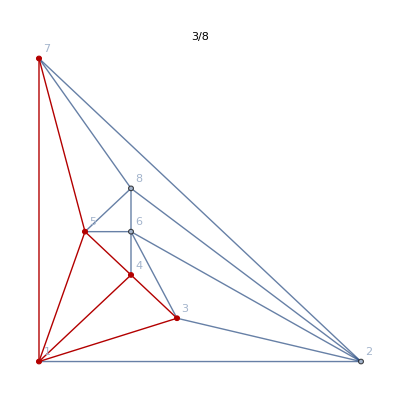

```mathematica
With[
{g=ReadGrof[15]},
Graph[EdgeAdd[EdgeDelete[g,{3<->7,3<->5}],{1<->5,1<->4}],GraphHighlight->{4,3,1,7,5,4<->3,3<->1,1<->7,7<->5,5<->4,1<->5,1<->4},VertexLabels->"Name", GraphLayout->"PlanarEmbedding", PlotLabel->"3/8"]
]
```

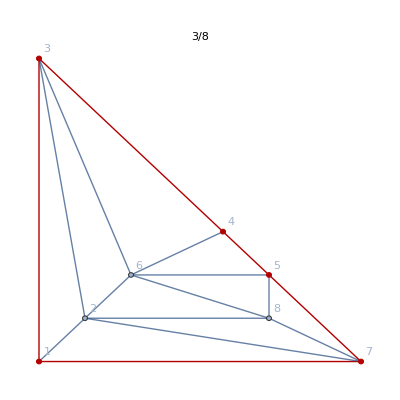

```mathematica
With[
{g=ReadGrof[15]},
Graph[EdgeDelete[g,{3<->7,3<->5}],GraphHighlight->{4,3,1,7,5,4<->3,3<->1,1<->7,7<->5,5<->4,1<->5,1<->4},VertexLabels->"Name", GraphLayout->"PlanarEmbedding", PlotLabel->"3/8"]
]
```

```mathematica
Both[g_]:={g,ChromaticPolynomial[g,4]/24}
```

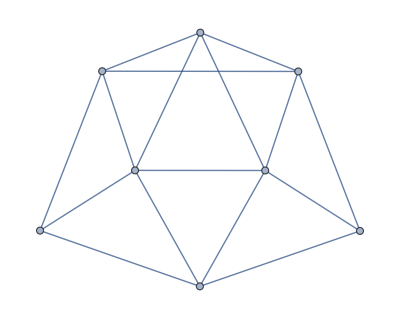
{-Graphics-,8}

```mathematica
Both[EdgeDelete[ReadGrof[15],{3<->7,3<->5}]]
```

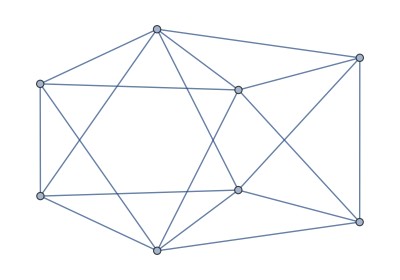
{-Graphics-,3}

```mathematica
Both[EdgeAdd[EdgeDelete[ReadGrof[15],{3<->7,3<->5}],{1<->5,1<->4}]]
```

```mathematica
ChromaticPolynomial[EdgeDelete[ReadGrof[13],{3<->7,3<->8}],4]/24
```

9

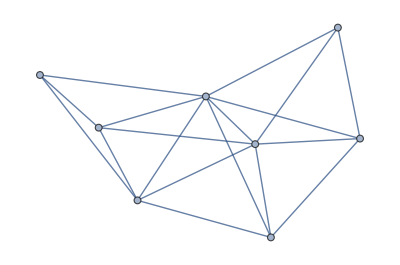

```mathematica
ReadGrof[13]
```

```mathematica
dd={7/4,({{3, 10/11, 1/4, 13/22, {{3<->6,3<->5},{9<->5,9<->2},{6<->2}}}, {9, 1/4, 13/22, 10/11, {{9<->5,9<->2},{6<->2,6<->3},{5<->3}}}, {6, 13/22, 5/11, 31/44, {{6<->2,6<->3},{5<->3,5<->9},{2<->9}}}, {5, 5/11, 13/44, 1, {{5<->3,5<->9},{2<->9,2<->6},{3<->6}}}, {2, 13/44, 10/11, 6/11, {{2<->9,2<->6},{3<->6,3<->5},{9<->5}}}}),{2966,28135,{3,{3,9,6,5,2},{2<->9,5<->9},{{2,3,9},{2,5,9},{5,6,9}}}}}
```

{7/4,{{10/11,1/4,13/22,{{3<->6,3<->5},{9<->5,9<->2},{6<->2}}},{1/4,13/22,10/11,{{9<->5,9<->2},{6<->2,6<->3},{5<->3}}},{13/22,5/11,31/44,{{6<->2,6<->3},{5<->3,5<->9},{2<->9}}},{5/11,13/44,1,{{5<->3,5<->9},{2<->9,2<->6},{3<->6}}},{13/44,10/11,6/11,{{2<->9,2<->6},{3<->6,3<->5},{9<->5}}}},{2966,28135,{3,{3,9,6,5,2},{2<->9,5<->9},{{2,3,9},{2,5,9},{5,6,9}}}}}

```mathematica
CicularEdges[{3,6,7,5,4}]
```

{3<->6,6<->7,7<->5,5<->4,3,4}

```mathematica
CicularEdges[vertices_]:=Join[Table[vertices[[i]]<->vertices[[i+1]],{i,1,Length[vertices]-1}],{vertices[[1]]<->vertices[[Length[vertices]]]}]
```

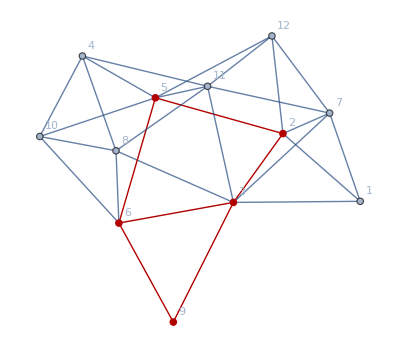

```mathematica
Graph[EdgeDelete[Graph[ReadGrof[2966],VertexLabels->"Name"],{2<->9,5<->9}],GraphHighlight->Join[{3,9,6,5,2},CicularEdges[{3,9,6,5,2}],{6<->2,6<->3}]]
```

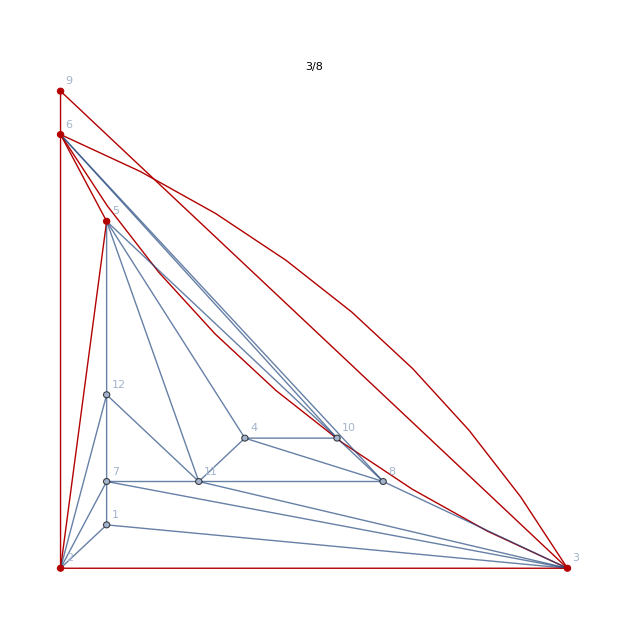

```mathematica
With[
{g=ReadGrof[2966]},
Graph[EdgeAdd[EdgeDelete[g,{2<->9,5<->9}],{6<->2,6<->3}],GraphHighlight->Join[{3,9,6,5,2},CicularEdges[{3,9,6,5,2}],{6<->2,6<->3}],VertexLabels->"Name", GraphLayout->"PlanarEmbedding", PlotLabel->"3/8"]
]
```

{5<->9,5<->12}

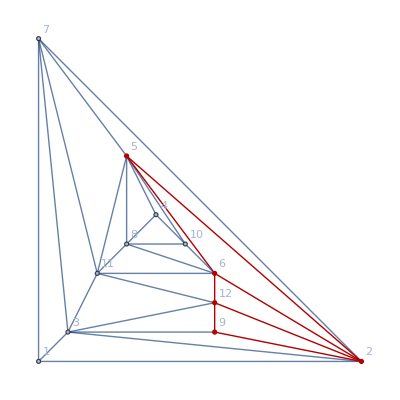

```mathematica
With[
{hin={7/4,({{2, 5/8, 5/8, 1/2, {{{2<->6,2<->12},{5<->12,5<->9},{6<->9}},{-3,-3,-4}}}, {5, 5/8, 3/8, 3/4, {{{5<->12,5<->9},{6<->9,6<->2},{12<->2}},{-3,-5,-2}}}, {6, 3/8, 1/2, 7/8, {{{6<->9,6<->2},{12<->2,12<->5},{9<->5}},{-5,-4,-1}}}, {12, 1/2, 3/8, 7/8, {{{12<->2,12<->5},{9<->5,9<->6},{2<->6}},{-4,-5,-1}}}, {9, 3/8, 5/8, 3/4, {{{9<->5,9<->6},{2<->6,2<->12},{5<->12}},{-5,-3,-2}}}}),{2965,17531,{3,{2,5,6,12,9},{5<->9,5<->12},{{2,5,9},{5,9,12},{5,6,12}}}}}},
With[
{g=ReadGrof[hin[[3,1]]], edges={2<->6,2<->12}},
With[{circle=CicularEdges[hin[[3,3,2]]]},
Print[hin[[3,3,3]]];
Graph[EdgeAdd[ EdgeDelete[g,hin[[3,3,3]]],edges],GraphHighlight->Join[hin[[3,3,2]],circle,edges],VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]
]]
]
```

{8<->10,6<->8}

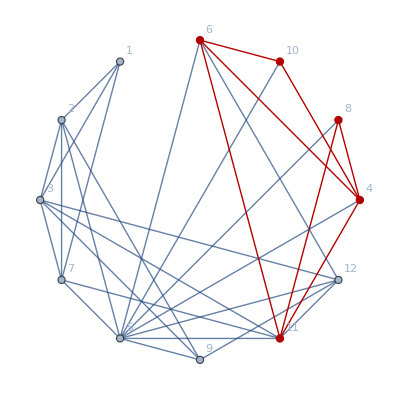

```mathematica
With[
{hin={1,({{4, 1/5, 1/5, 3/5, {{{4<->11,4<->6},{8<->6,8<->10},{11<->10}},{-20,-20,-10}}}, {8, 1/5, 1/5, 3/5, {{{8<->6,8<->10},{11<->10,11<->4},{6<->4}},{-20,-20,-10}}}, {11, 1/5, 1/5, 3/5, {{{11<->10,11<->4},{6<->4,6<->8},{10<->8}},{-20,-20,-10}}}, {6, 1/5, 1/5, 3/5, {{{6<->4,6<->8},{10<->8,10<->11},{4<->11}},{-20,-20,-10}}}, {10, 1/5, 1/5, 3/5, {{{10<->8,10<->11},{4<->11,4<->6},{8<->6}},{-20,-20,-10}}}}),{2965,10449,{3,{4,8,11,6,10},{8<->10,6<->8},{{4,8,10},{6,8,10},{6,8,11}}}}}},
With[
{g=ReadGrof[hin[[3,1]]], edges={4<->11,4<->6}},
With[{circle=CicularEdges[hin[[3,3,2]]]},
Print[hin[[3,3,3]]];
Graph[EdgeAdd[ EdgeDelete[g,hin[[3,3,3]]],edges],GraphHighlight->Join[hin[[3,3,2]],circle,edges],VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
]]
]
```

{8<->10,6<->8}

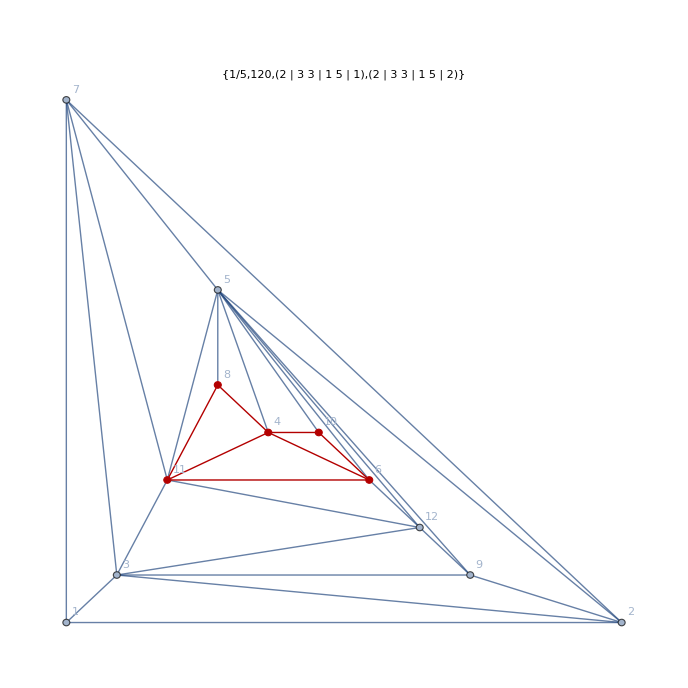

```mathematica
With[
{hin={1,({{4, 1/5, 1/5, 3/5, {{{4<->11,4<->6},{8<->6,8<->10},{11<->10}},{-20,-20,-10}}}, {8, 1/5, 1/5, 3/5, {{{8<->6,8<->10},{11<->10,11<->4},{6<->4}},{-20,-20,-10}}}, {11, 1/5, 1/5, 3/5, {{{11<->10,11<->4},{6<->4,6<->8},{10<->8}},{-20,-20,-10}}}, {6, 1/5, 1/5, 3/5, {{{6<->4,6<->8},{10<->8,10<->11},{4<->11}},{-20,-20,-10}}}, {10, 1/5, 1/5, 3/5, {{{10<->8,10<->11},{4<->11,4<->6},{8<->6}},{-20,-20,-10}}}}),{2965,10449,{3,{4,8,11,6,10},{8<->10,6<->8},{{4,8,10},{6,8,10},{6,8,11}}}}}},
With[
{g=ReadGrof[hin[[3,1]]], edges={4<->11,4<->6}},
With[{circle=CicularEdges[hin[[3,3,2]]](*CicularEdges[hin[[3,3,2]]]*)},
Print[hin[[3,3,3]]];
With[{h=EdgeAdd[ EdgeDelete[g,hin[[3,3,3]]],edges],f=EdgeDelete[g,hin[[3,3,3]]]},

Graph[h,GraphHighlight->Join[hin[[3,3,2]],circle,edges],VertexLabels->"Name", GraphLayout->"PlanarEmbedding", PlotLabel->{ChromaticPolynomial[h,4]/ChromaticPolynomial[f,4],ChromaticPolynomial[h,4]/Numerator[ChromaticPolynomial[h,4]/ChromaticPolynomial[f,4]],FactorInteger[ChromaticPolynomial[h,4]],FactorInteger[ChromaticPolynomial[f,4]]}]
]]]
]
```

{11<->12,3<->12}

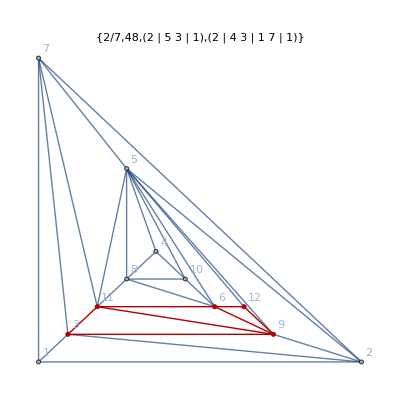

```mathematica
With[
{hin={11/7,({{6, 5/14, 5/14, 6/7, {{{6<->9,6<->3},{12<->3,12<->11},{9<->11}},{-9,-9,-2}}}, {12, 5/14, 2/7, 13/14, {{{12<->3,12<->11},{9<->11,9<->6},{3<->6}},{-9,-10,-1}}}, {9, 2/7, 6/7, 3/7, {{{9<->11,9<->6},{3<->6,3<->12},{11<->12}},{-10,-2,-8}}}, {3, 6/7, 2/7, 3/7, {{{3<->6,3<->12},{11<->12,11<->9},{6<->9}},{-2,-10,-8}}}, {11, 2/7, 5/14, 13/14, {{{11<->12,11<->9},{6<->9,6<->3},{12<->3}},{-10,-9,-1}}}}),{2965,19057,{3,{6,12,9,3,11},{11<->12,3<->12},{{6,11,12},{3,11,12},{3,9,12}}}}}},
With[
{g=ReadGrof[hin[[3,1]]], edges={9<->11,9<->6}},
With[{circle=CicularEdges[hin[[3,3,2]]](*CicularEdges[hin[[3,3,2]]]*)},
Print[hin[[3,3,3]]];
With[{h=EdgeAdd[ EdgeDelete[g,hin[[3,3,3]]],edges],f=EdgeDelete[g,hin[[3,3,3]]]},

Graph[h,GraphHighlight->Join[hin[[3,3,2]],circle,edges],VertexLabels->"Name", GraphLayout->"PlanarEmbedding", PlotLabel->{ChromaticPolynomial[h,4]/ChromaticPolynomial[f,4],ChromaticPolynomial[h,4]/Numerator[ChromaticPolynomial[h,4]/ChromaticPolynomial[f,4]],FactorInteger[ChromaticPolynomial[h,4]],FactorInteger[ChromaticPolynomial[f,4]]}]
]]]
]
```

```mathematica
MatrixForm[AdjacencyMatrix[%237].AdjacencyMatrix[%237].AdjacencyMatrix[%237].AdjacencyMatrix[%237],TableHeadings->{Range[12], Range[12]}]
```

( | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
1 | 33 | 44 | 44 | 44 | 56 | 48 | 48 | 22 | 14 | 26 | 20 | 34
2 | 44 | 82 | 70 | 73 | 97 | 80 | 93 | 51 | 37 | 56 | 47 | 74
3 | 44 | 70 | 77 | 70 | 104 | 77 | 77 | 41 | 29 | 53 | 37 | 71
4 | 44 | 73 | 70 | 82 | 99 | 91 | 82 | 46 | 36 | 63 | 46 | 75
5 | 56 | 97 | 104 | 99 | 199 | 135 | 138 | 80 | 71 | 118 | 93 | 143
6 | 48 | 80 | 77 | 91 | 135 | 116 | 105 | 62 | 50 | 88 | 68 | 101
7 | 48 | 93 | 77 | 82 | 138 | 105 | 124 | 71 | 57 | 85 | 76 | 105
8 | 22 | 51 | 41 | 46 | 80 | 62 | 71 | 45 | 35 | 55 | 48 | 64
9 | 14 | 37 | 29 | 36 | 71 | 50 | 57 | 35 | 38 | 51 | 44 | 62
10 | 26 | 56 | 53 | 63 | 118 | 88 | 85 | 55 | 51 | 86 | 68 | 92
11 | 20 | 47 | 37 | 46 | 93 | 68 | 76 | 48 | 44 | 68 | 61 | 73
12 | 34 | 74 | 71 | 75 | 143 | 101 | 105 | 64 | 62 | 92 | 73 | 117)

```mathematica
Det[AdjacencyMatrix[%237]]
```

12

{3<->7,3<->11}

{3<->7,3<->11}

{3<->7,3<->11}

«1 more identical outputs»

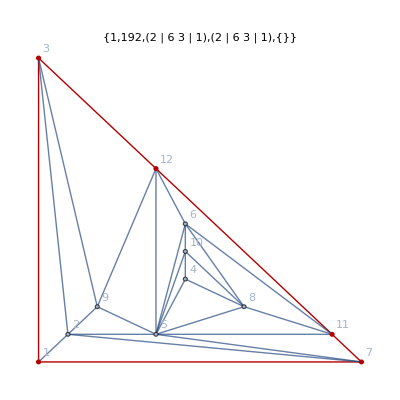
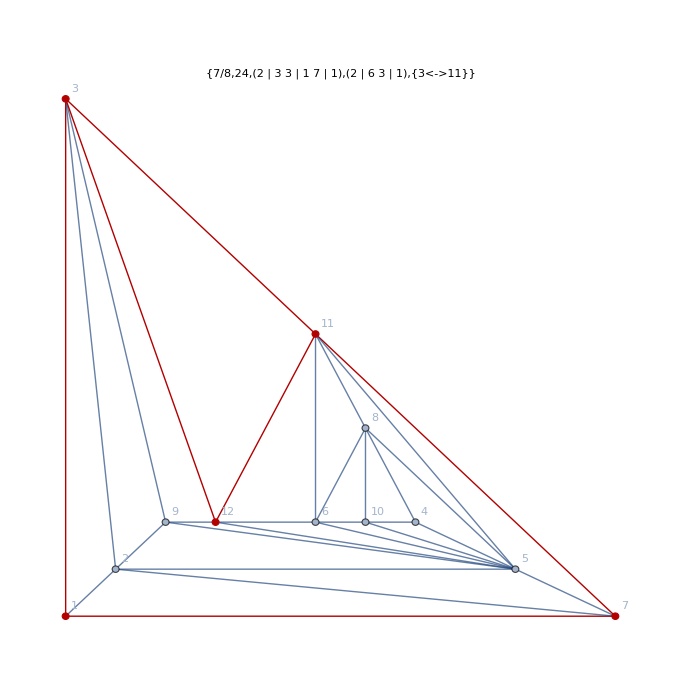
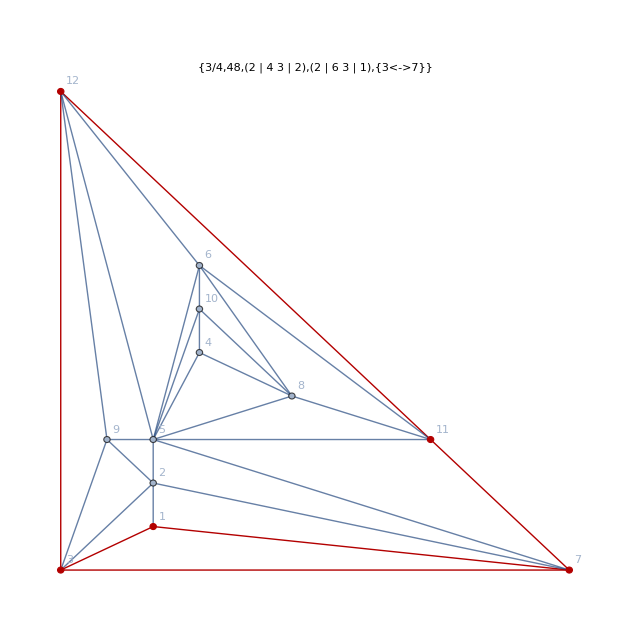
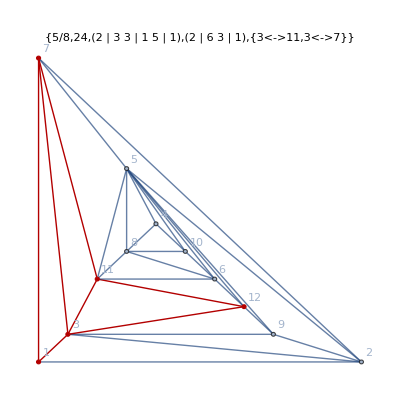

```mathematica
With[
{hin={7/4,({{1, 3/8, 5/8, 3/4, {{{1<->12,1<->11},{3<->11,3<->7},{12<->7}},{-5,-3,-2}}}, {3, 5/8, 5/8, 1/2, {{{3<->11,3<->7},{12<->7,12<->1},{11<->1}},{-3,-3,-4}}}, {12, 5/8, 3/8, 3/4, {{{12<->7,12<->1},{11<->1,11<->3},{7<->3}},{-3,-5,-2}}}, {11, 3/8, 1/2, 7/8, {{{11<->1,11<->3},{7<->3,7<->12},{1<->12}},{-5,-4,-1}}}, {7, 1/2, 3/8, 7/8, {{{7<->3,7<->12},{1<->12,1<->11},{3<->11}},{-4,-5,-1}}}}),{2965,13812,{3,{1,3,12,11,7},{3<->7,3<->11},{{1,3,7},{3,7,11},{3,11,12}}}}}},
With[
{g=ReadGrof[hin[[3,1]]], edges={3<->11,3<->7}},
Table[
With[{circle=CicularEdges[hin[[3,3,2]]](*CicularEdges[hin[[3,3,2]]]*)},
Print[hin[[3,3,3]]];
With[{h=EdgeAdd[ EdgeDelete[g,hin[[3,3,3]]],e],f=EdgeDelete[g,hin[[3,3,3]]]},

Graph[h,GraphHighlight->Join[hin[[3,3,2]],circle,e],VertexLabels->"Name", GraphLayout->"PlanarEmbedding", PlotLabel->{ChromaticPolynomial[h,4]/ChromaticPolynomial[f,4],ChromaticPolynomial[h,4]/Numerator[ChromaticPolynomial[h,4]/ChromaticPolynomial[f,4]],FactorInteger[ChromaticPolynomial[h,4]],FactorInteger[ChromaticPolynomial[f,4]],e}]
]],
{e,Subsets[edges]}]
]]
```

{7<->11,7<->12}

{7<->11,7<->12}

{7<->11,7<->12}

«1 more identical outputs»

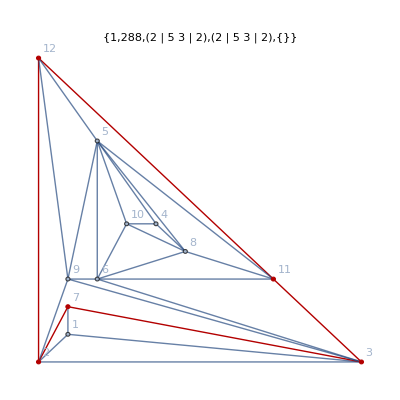
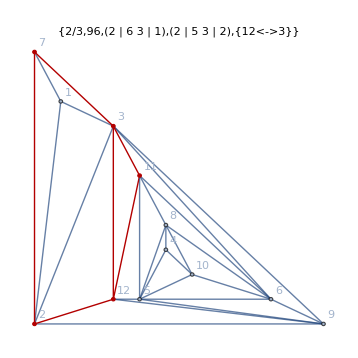
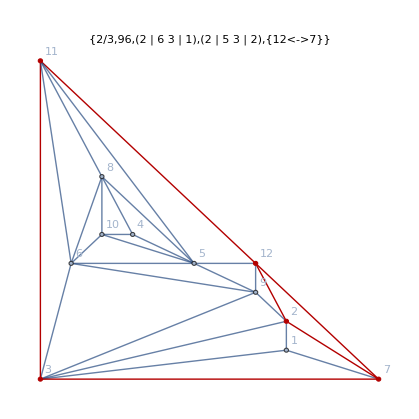
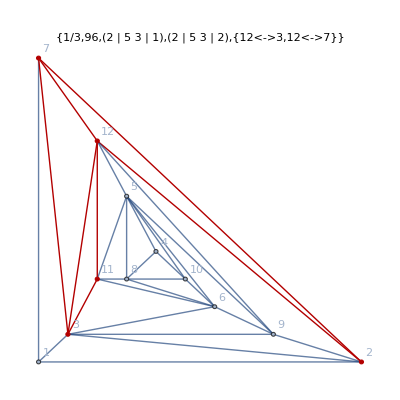

```mathematica
With[
{hin={7/4,({{3, 2/3, 1/4, 5/6, {{{3<->2,3<->12},{7<->12,7<->11},{2<->11}},{-4,-9,-2}}}, {7, 1/4, 5/6, 2/3, {{{7<->12,7<->11},{2<->11,2<->3},{12<->3}},{-9,-2,-4}}}, {2, 5/6, 1/3, 7/12, {{{2<->11,2<->3},{12<->3,12<->7},{11<->7}},{-2,-8,-5}}}, {12, 1/3, 5/12, 1, {{{12<->3,12<->7},{11<->7,11<->2},{3<->2}},{-8,-7,0}}}, {11, 5/12, 2/3, 2/3, {{{11<->7,11<->2},{3<->2,3<->12},{7<->12}},{-7,-4,-4}}}}),{2964,16299,{3,{3,7,2,12,11},{7<->11,7<->12},{{3,7,11},{7,11,12},{2,7,12}}}}}},
With[
{g=ReadGrof[hin[[3,1]]], edges={12<->3,12<->7}},
Table[
With[{circle=CicularEdges[hin[[3,3,2]]](*CicularEdges[hin[[3,3,2]]]*)},
Print[hin[[3,3,3]]];
With[{h=EdgeAdd[ EdgeDelete[g,hin[[3,3,3]]],e],f=EdgeDelete[g,hin[[3,3,3]]]},

Graph[h,GraphHighlight->Join[hin[[3,3,2]],circle,e],VertexLabels->"Name", GraphLayout->"PlanarEmbedding", PlotLabel->{ChromaticPolynomial[h,4]/ChromaticPolynomial[f,4],ChromaticPolynomial[h,4]/Numerator[ChromaticPolynomial[h,4]/ChromaticPolynomial[f,4]],FactorInteger[ChromaticPolynomial[h,4]],FactorInteger[ChromaticPolynomial[f,4]],e}]
]],
{e,Subsets[edges]}]
]]
```

{4<->5,5<->10}

{4<->5,5<->10}

{4<->5,5<->10}

«1 more identical outputs»

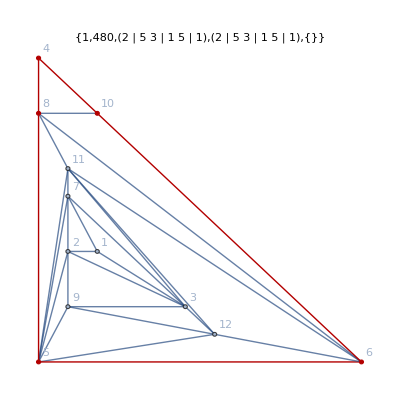
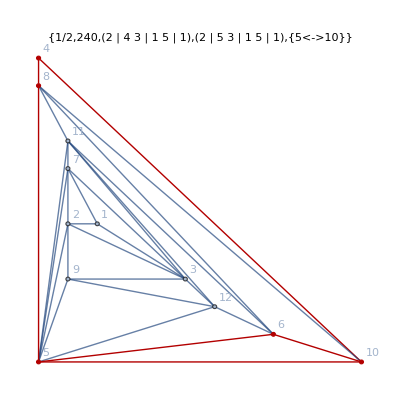
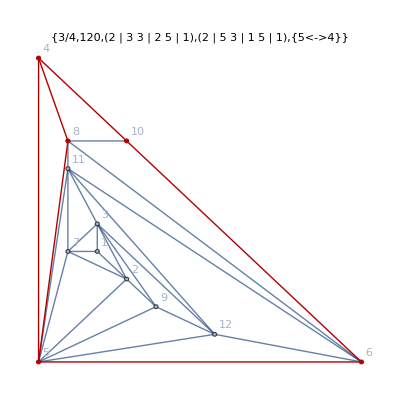
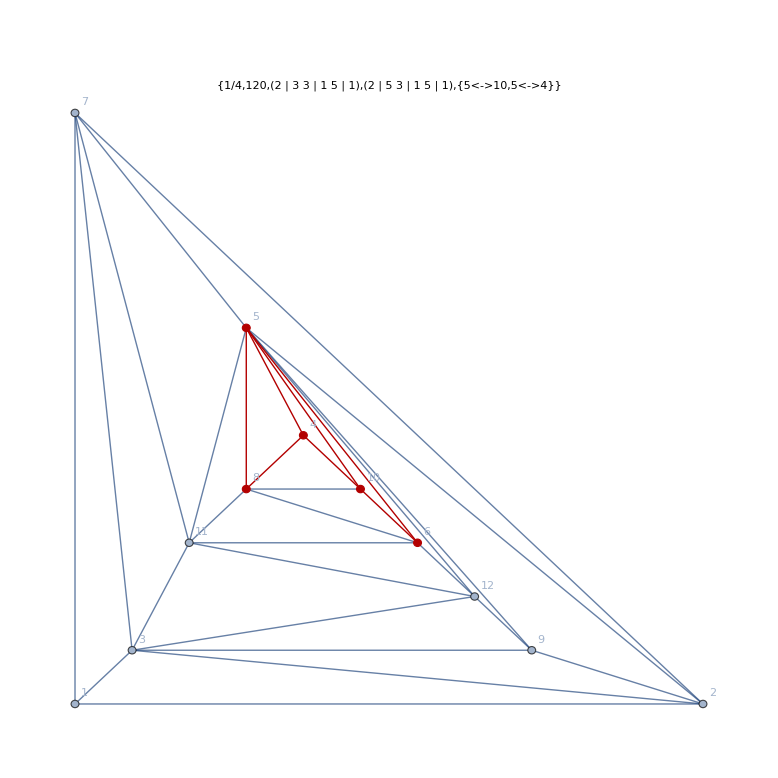

```mathematica
With[
{hin={7/4,({{8, 1, 1/4, 1/2, {{{8<->6,8<->10},{5<->10,5<->4},{6<->4}},{0,-15,-10}}}, {5, 1/4, 1/2, 1, {{{5<->10,5<->4},{6<->4,6<->8},{10<->8}},{-15,-10,0}}}, {6, 1/2, 1/2, 3/4, {{{6<->4,6<->8},{10<->8,10<->5},{4<->5}},{-10,-10,-5}}}, {10, 1/2, 1/4, 1, {{{10<->8,10<->5},{4<->5,4<->6},{8<->6}},{-10,-15,0}}}, {4, 1/4, 1, 1/2, {{{4<->5,4<->6},{8<->6,8<->10},{5<->10}},{-15,0,-10}}}}),{2965,15831,{3,{8,5,6,10,4},{4<->5,5<->10},{{4,5,8},{4,5,10},{5,6,10}}}}}},
With[
{g=ReadGrof[hin[[3,1]]], edges={5<->10,5<->4}},
Table[
With[{circle=CicularEdges[hin[[3,3,2]]](*CicularEdges[hin[[3,3,2]]]*)},
Print[hin[[3,3,3]]];
With[{h=EdgeAdd[ EdgeDelete[g,hin[[3,3,3]]],e],f=EdgeDelete[g,hin[[3,3,3]]]},

Graph[h,GraphHighlight->Join[hin[[3,3,2]],circle,e],VertexLabels->"Name", GraphLayout->"PlanarEmbedding", PlotLabel->{ChromaticPolynomial[h,4]/ChromaticPolynomial[f,4],ChromaticPolynomial[h,4]/Numerator[ChromaticPolynomial[h,4]/ChromaticPolynomial[f,4]],FactorInteger[ChromaticPolynomial[h,4]],FactorInteger[ChromaticPolynomial[f,4]],e},ImageSize->400]
]],
{e,Subsets[edges]}]
]]
```

{3<->5,5<->7}

{3<->5,5<->7}

{3<->5,5<->7}

«1 more identical outputs»

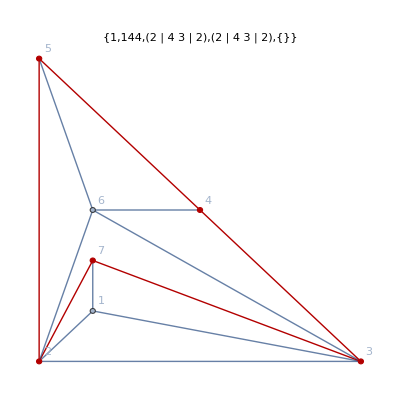
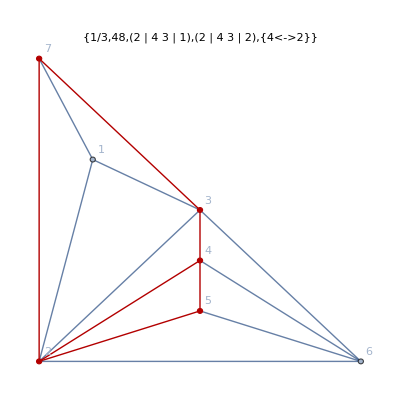
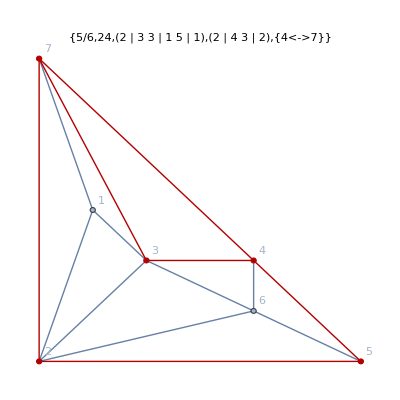
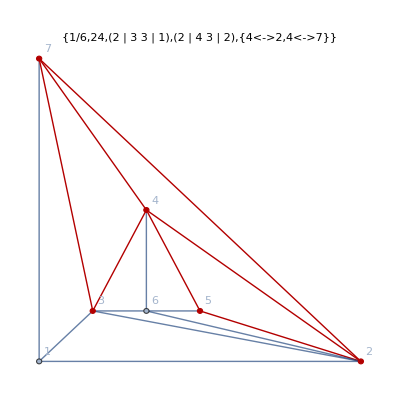

```mathematica
With[
{hin={4/3,({{4, 1/6, 1/6, 1, {{{4<->2,4<->7},{5<->7,5<->3},{2<->3}},{-5,-5,0}}}, {5, 1/6, 1/3, 5/6, {{{5<->7,5<->3},{2<->3,2<->4},{7<->4}},{-5,-4,-1}}}, {2, 1/3, 2/3, 1/3, {{{2<->3,2<->4},{7<->4,7<->5},{3<->5}},{-4,-2,-4}}}, {7, 2/3, 1/3, 1/3, {{{7<->4,7<->5},{3<->5,3<->2},{4<->2}},{-2,-4,-4}}}, {3, 1/3, 1/6, 5/6, {{{3<->5,3<->2},{4<->2,4<->7},{5<->7}},{-4,-5,-1}}}}),{5,14,{3,{4,5,2,7,3},{3<->5,5<->7},{{3,4,5},{3,5,7},{2,5,7}}}}}},
With[
{g=ReadGrof[hin[[3,1]]], edges={4<->2,4<->7}},
Table[
With[{circle=CicularEdges[hin[[3,3,2]]](*CicularEdges[hin[[3,3,2]]]*)},
Print[hin[[3,3,3]]];
With[{h=EdgeAdd[ EdgeDelete[g,hin[[3,3,3]]],e],f=EdgeDelete[g,hin[[3,3,3]]]},

Graph[h,GraphHighlight->Join[hin[[3,3,2]],circle,e],VertexLabels->"Name", GraphLayout->"PlanarEmbedding", PlotLabel->{ChromaticPolynomial[h,4]/ChromaticPolynomial[f,4],ChromaticPolynomial[h,4]/Numerator[ChromaticPolynomial[h,4]/ChromaticPolynomial[f,4]],FactorInteger[ChromaticPolynomial[h,4]],FactorInteger[ChromaticPolynomial[f,4]],e},ImageSize->400]
]],
{e,Subsets[edges]}]
]]
```

```mathematica
Criterion[4<->2,4<->7]
```

x4==1&&x2==2&&x4==3

```mathematica
ToVars2[ReadGrof[5],"x1==1&&x2==2"]
```

{{x1→1,x2→2,x3→3,x7→4,x5→1,x6→4,x4→2},{x1→1,x2→2,x3→4,x7→3,x5→1,x6→3,x4→2}}

```mathematica
EdgeList[-Graphics-]
```

{1<->2,1<->3,1<->7,2<->3,2<->5,2<->6,2<->7,3<->4,3<->6,3<->7,4<->5,4<->6,5<->6}

```mathematica
ToVars2[Graph[{1<->2,1<->3,1<->7,2<->3,2<->5,2<->6,2<->7,3<->4,3<->6,3<->7,4<->5,4<->6,5<->6}],"x4==1&&x2==2&&x4==3"]
```

{}

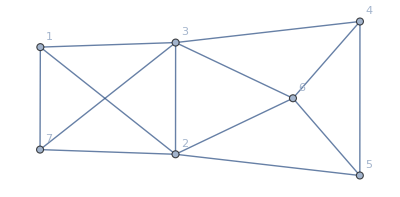

```mathematica
Graph[{1<->2,1<->3,1<->7,2<->3,2<->5,2<->6,2<->7,3<->4,3<->6,3<->7,4<->5,4<->6,5<->6},VertexLabels->"Name"]
```

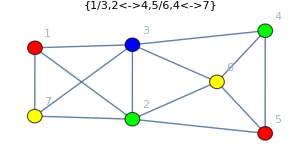
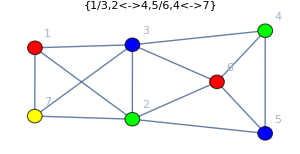
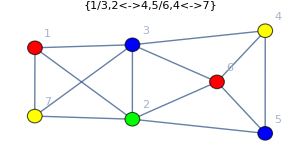
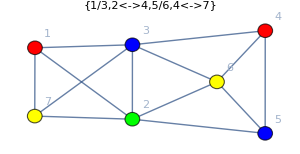
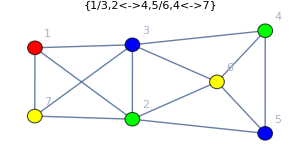
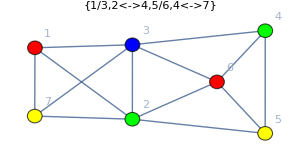
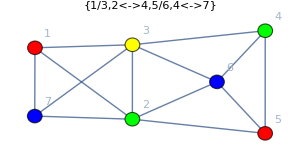
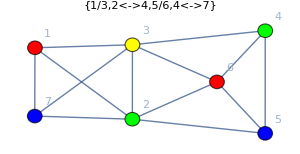

```mathematica
PaintGraph2[Graph[{1<->2,1<->3,1<->7,2<->3,2<->5,2<->6,2<->7,3<->4,3<->6,3<->7,4<->5,4<->6,5<->6},VertexLabels->"Name"],"x1==1&&x2==2",GraphLayout->"SpringElectricalEmbedding",PlotLabel->{1/3,2<->4,5/6,4<->7},ImageSize->300]
```

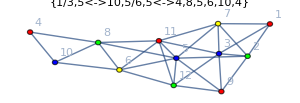
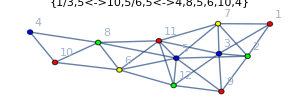
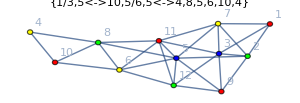
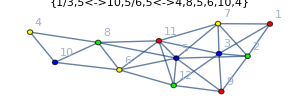
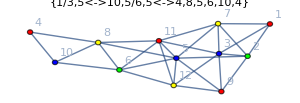
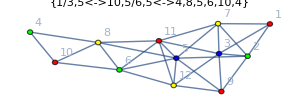
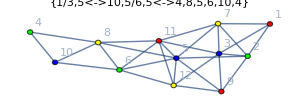
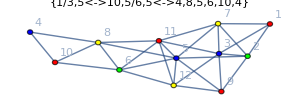

```mathematica
PaintGraph2[EdgeDelete[ReadGrof[2965],{4<->5,5<->10}],"x1==1&&x2==2",VertexLabels->"Name", GraphLayout->"SpringElectricalEmbedding",PlotLabel->{1/3,5<->10,5/6,5<->4,8,5,6,10,4}, ImageSize->300]
```